## Elasticity

```mathematica
(* Beautiful output *)
ForPrint={
Derivative[i__][f_][x__]:> Subscript[f,Row@Flatten@MapThread[Table,{{x},{i}}]],
U[x__]:>U, V[x__]:>V,U0[x__]->Subscript[U, 0],V0[x__]-> Subscript[V, 0],U1[x__]->Subscript[U, 1],V1[x__]-> Subscript[V, 1],
U2[x__]->Subscript[U, 2],V2[x__]-> Subscript[V, 2],V3[x__]->Subscript[V, 3],U4[x__]->Subscript[U, 4],V5[x__]->Subscript[V, 5],U6[x__]->Subscript[U, 6],
S[x__]->S,T[x__]->T};
ForPrint2={U0->Subscript[U, 0],V0-> Subscript[V, 0],U1->Subscript[U, 1],V1-> Subscript[V, 1],U2->Subscript[U, 2],V2-> Subscript[V, 2],V3->Subscript[V, 3],U4->Subscript[U, 4],V5->Subscript[V, 5],U6->Subscript[U, 6],
g1->Subscript[γ, 1],g2->Subscript[γ, 2],g3->Subscript[γ, 3],g4->Subscript[γ, 4]};
ForLatex={
Subscript[Subscript[f_,n_],Row[{a__}]]->Subscript[f,Flatten[{n,a}]/.List->Sequence],
Subscript[f_,Row[{a__}]]->Subscript[f,Flatten[{a}]/.List->Sequence]};
```

```mathematica
(* NOTATION:,
Displace - displacement vector
Deform - gradient of displacement vector in cylindrical coordinates
SGr - Green strain tensor
Pot - potential energy density
P   - first Piola-Kirchhoff stress tensor *)
ClearAll[U,V,W,λ,μ];
Displace={U[x,r,t],V[x,r,t],0};
Deform=RotateRight[Grad[RotateLeft[Displace,1],{r,ϕ,x},"Cylindrical"],{1,1}];
```

```mathematica
Inv1[tensor_]:=Tr[tensor];
Inv2[tensor_]:=((Tr[tensor])^2-Tr[tensor.Transpose[tensor]])/2;
Inv3[tensor_]:=Det[tensor];

StrainGreen[mode_]:=Module[{SGr},
SGr=(Transpose[Deform]+Deform)/2;
If[mode=="nonlinear2"||mode=="nonlinear3",
SGr=SGr+(Transpose[Deform].Deform)/2];
SGrTemplate={
{Subscript[SG, xx],Subscript[SG, xy],Subscript[SG, xz]},
{Subscript[SG, yx],Subscript[SG, yy],Subscript[SG, yz]},
{Subscript[SG, zx],Subscript[SG, zy],Subscript[SG, zz]}};
SGrSubst={ 
Subscript[SG, xx]->SGr⟦1,1⟧,Subscript[SG, xy]->SGr⟦1,2⟧,Subscript[SG, xz]->SGr⟦1,3⟧,
Subscript[SG, yx]->SGr⟦2,1⟧,Subscript[SG, yy]->SGr⟦2,2⟧,Subscript[SG, yz]->SGr⟦2,3⟧,
Subscript[SG, zx]->SGr⟦3,1⟧,Subscript[SG, zy]->SGr⟦3,2⟧,Subscript[SG, zz]->SGr⟦3,3⟧};
I1 = Inv1[SGrTemplate];
I2 = Inv2[SGrTemplate];
I3 = Inv3[SGrTemplate];
E1 = Inv1[SGrTemplate];
E2 = Inv1[SGrTemplate.SGrTemplate];
E3 = Inv1[SGrTemplate.SGrTemplate.SGrTemplate];
SGr];

PotEnergyTempl[mode_,modules_]:=Module[{Pot},
Pot=(λ+2 μ)/2 I1^2-2 μ I2;
If[modules=="murnaghan",
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=Pot+(l+2 m)/3 I1^3-2 m I1 I2+n I3;
If[mode=="nonlinear3",
Pot=Pot+g1 I1^4+g2 I2^2+g3 I1 I3+g4 I2^2];],
If[modules=="landau",
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=Pot+CL/3 E1^3+BL E1 E2+AL/3 E3;
If[mode=="nonlinear3",
Pot=Pot+HL E1^4+GL E2^2+FL E1^2 E2+EL E1 E3];
],Throw["Unknown modules"]];
];
Pot];

PotEnergy[mode_,modules_]:=Module[{},
PotEnergyTempl[mode,modules]/.SGrSubst];

Piola[mode_,modules_]:=Module[{P,Pot},
If[mode=="linear",P=λ Inv1[SGr]IdentityMatrix[3]+2μ SGr//Simplify];
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=PotEnergyTempl[mode,modules];
P=(IdentityMatrix[3]+Deform).{
{D[Pot, Subscript[SG, xx]],D[Pot, Subscript[SG, xy]],D[Pot, Subscript[SG, xz]]},
{D[Pot, Subscript[SG, yx]],D[Pot, Subscript[SG, yy]],D[Pot, Subscript[SG, yz]]},
{D[Pot, Subscript[SG, zx]],D[Pot, Subscript[SG, zy]],D[Pot, Subscript[SG, zz]]}}/.SGrSubst ];
P];
```

## Long waves

```mathematica
mode="nonlinear3";
modules="landau";
SGr=StrainGreen[mode];
Pot=PotEnergy[mode,modules];
P=Piola[mode,modules];
```

```mathematica
Scales={
Derivative[i_,j_,k_][f_][x_,r_,t_]->ε L Derivative[i,j,k][f][x,r,t] L^(-i-j-k) s^k,
U[x__]->ε L U[x],V[x__]->ε L V[x],Power[r,n_]->( L r)^n};
Scales2={
Derivative[i_,j_,k_][f_][x_,r_,t_]->ε L Derivative[i,j,k][f][x,r,t] L^(-i-j-k)s^k δ^-j,
U[x__]->ε L U[x],V[x__]->ε L V[x],r->δ L r};
```

### Pre-stretch solution

```mathematica
USeries[x_,r_,t_]=γ x;
VSeries[x_,r_,t_]=(V10(*+ε V11*))r;
```

#### Equations

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[Transpose@RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧)L/ε/δ/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
Series[ndEq1,{ε,0,1}]//Simplify
ndEq2//Simplify
```

0

0

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V,U4,V3,U2]
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
Series[ndP⟦2,2⟧/ε,{ε,0,1}]//Simplify
ndP⟦2,1⟧
```

O[ε]^2

0

```mathematica
V[x,r,t]
```

r (V10+V11 ε)

```mathematica
V10=-λ/(2(λ+μ))γ+FV1 ε;
```

```mathematica
FV1=-(γ^2 (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2))/(8 (λ+μ)^3);
```

### 1st Method: nonlinear dimensionless equations

```mathematica
USeries[x_,r_,t_]=U0[x,t]+U2[x,t] r^2+U4[x,t] r^4+U6[x,t] r^6;
VSeries[x_,r_,t_]=V1[x,t]r+V3[x,t] r^3+V5[x,t] r^5+V7[x,t] r^7;
```

Pre-stretch (run only if pre-stretched rod is considered):

```mathematica
ClearAll[V1,FV1];
USeries[x_,r_,t_]=γ x+U0[x,t]+U2[x,t] r^2 δ^2+U4[x,t] δ^4 r^4;
VSeries[x_,r_,t_]=((-γ λ/2 /(λ+μ)-γ^2 ε (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2)/8 /(λ+μ)^3) r
+V1[x,t]r+V3[x,t] δ^2 r^3+V5[x,t] δ^4 r^5);
```

#### Equations

```mathematica
ClearAll[U,V];
(* Note: in order to calculate the "normal" divergence, tensor has to be transposed before application of Div[],
however here we calculate divergence of a two-point tensor with respect to the reference coordinates,
which results in transposed tensor, hence there is no need of transposing here. *)
divPK=RotateRight[Div[RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧)L/ε/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
Print["Equation 1:"]
ndEq1red=Normal@Series[ndEq1/.{r->α r,ε->α^2 ε},{α,0,4}]/.{α->1}//Simplify;
Series[ndEq1red,{r,0,5},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify
Print["Equation 2:"]
ndEq2red=Normal@Series[ndEq2/r/.{r->α r,ε->α^2 ε},{α,0,4}]/.{α->1}//Simplify;
Series[ndEq2red,{r,0,5},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify
```

Equation 1:

((-4 μ U_2+s^2 ρ U_0_tt-λ U_0_xx-2 μ U_0_xx-2 λ V_1_x-2 μ V_1_x)+(-2 U_2 ((AL+4 (BL+λ+μ)) V_1+(AL+2 (BL+λ+2 μ)) U_0_x)-U_0_x ((2 AL+6 BL+2 CL+3 λ+6 μ) U_0_xx+(AL+2 (3 BL+2 CL+λ+μ)) V_1_x)-V_1 (2 (2 BL+2 CL+λ) U_0_xx+(AL+2 (4 BL+4 CL+λ+μ)) V_1_x)) ε+(-U_2 ((5 AL+4 (7 BL+4 CL+3 EL+4 FL+4 GL+λ+μ)) V_1^2+2 (2 AL+12 BL+8 CL+9 EL+8 FL) V_1 U_0_x+(5 AL+2 (7 BL+2 CL+3 EL+2 FL+4 GL+λ+2 μ)) (U_0)_x^2)-1/2 V_1^2 (2 (4 BL+6 CL+12 FL+8 GL+48 HL+λ) U_0_xx+(3 AL+8 (3 BL+3 CL+3 EL+8 FL+2 GL+24 HL)) V_1_x)-1/2 (U_0)_x^2 (3 (4 AL+12 BL+4 CL+8 EL+8 FL+8 GL+8 HL+λ+2 μ) U_0_xx+(3 AL+2 (9 BL+6 CL+9 EL+14 FL+4 GL+24 HL)) V_1_x)-V_1 U_0_x (12 (BL+CL+EL+2 FL+4 HL) U_0_xx+(2 AL+14 BL+12 CL+9 EL+32 FL+16 GL+96 HL+2 λ+2 μ) V_1_x)) ε^2+O[ε]^3)+((-16 μ U_4+s^2 ρ U_2_tt-λ U_2_xx-2 μ U_2_xx-4 λ V_3_x-4 μ V_3_x)+(-8 U_4 ((AL+4 (BL+λ+μ)) V_1+(AL+2 (BL+λ+2 μ)) U_0_x)-8 BL V_3 U_0_xx-8 CL V_3 U_0_xx-4 λ V_3 U_0_xx-2 AL U_0_xx U_2_x-6 BL U_0_xx U_2_x-2 CL U_0_xx U_2_x-3 λ U_0_xx U_2_x-6 μ U_0_xx U_2_x-4 BL V_1 U_2_xx-4 CL V_1 U_2_xx-2 λ V_1 U_2_xx-2 AL U_0_x U_2_xx-6 BL U_0_x U_2_xx-2 CL U_0_x U_2_xx-3 λ U_0_x U_2_xx-6 μ U_0_x U_2_xx-6 AL V_3 V_1_x-24 BL V_3 V_1_x-16 CL V_3 V_1_x-4 λ V_3 V_1_x-12 μ V_3 V_1_x-3 AL U_2_x V_1_x-10 BL U_2_x V_1_x-4 CL U_2_x V_1_x-2 λ U_2_x V_1_x-6 μ U_2_x V_1_x-1/2 AL V_1_x V_1_xx-BL V_1_x V_1_xx-λ V_1_x V_1_xx-2 μ V_1_x V_1_xx-U_2 (4 (3 AL+8 BL+8 λ+12 μ) V_3+6 (AL+2 (BL+λ+2 μ)) U_2_x+(AL+2 (BL+μ)) V_1_xx)-2 AL V_1 V_3_x-16 BL V_1 V_3_x-16 CL V_1 V_3_x-4 λ V_1 V_3_x-4 μ V_1 V_3_x-2 AL U_0_x V_3_x-12 BL U_0_x V_3_x-8 CL U_0_x V_3_x-4 λ U_0_x V_3_x-4 μ U_0_x V_3_x) ε+O[ε]^3) r^2+(-36 μ U_6+s^2 ρ U_4_tt-λ U_4_xx-2 μ U_4_xx-6 λ V_5_x-6 μ V_5_x) r^4+O[r]^6

Equation 2:

((-8 (λ+2 μ) V_3-2 (λ+μ) U_2_x+s^2 ρ V_1_tt-μ V_1_xx)+(-(3 AL+4 (BL+λ+3 μ)) U_2^2-16 BL V_3 U_0_x-16 CL V_3 U_0_x-8 λ V_3 U_0_x-AL U_0_x U_2_x-6 BL U_0_x U_2_x-4 CL U_0_x U_2_x-2 λ U_0_x U_2_x-2 μ U_0_x U_2_x-1/2 AL U_0_xx V_1_x-BL U_0_xx V_1_x-λ U_0_xx V_1_x-2 μ U_0_xx V_1_x-5/4 AL (V_1)_x^2-3 BL (V_1)_x^2-3 λ (V_1)_x^2-5 μ (V_1)_x^2-(AL+2 (BL+μ)) U_2 (U_0_xx+4 V_1_x)-1/2 AL U_0_x V_1_xx-BL U_0_x V_1_xx-λ U_0_x V_1_xx-2 μ U_0_x V_1_xx-1/2 V_1 (32 (AL+4 BL+2 CL+2 λ+3 μ) V_3+2 (AL+2 (4 BL+4 CL+λ+μ)) U_2_x+(AL+4 (BL+λ+μ)) V_1_xx)) ε+1/4 (-4 U_2^2 ((15 AL+4 (11 BL+4 CL+6 EL+4 FL+4 GL+λ+3 μ)) V_1+(6 AL+20 BL+8 CL+15 EL+8 FL) U_0_x)-4 U_2 (V_1 ((2 AL+6 BL+9 EL+8 FL+2 μ) U_0_xx+4 (3 AL+8 BL+9 EL+8 FL+8 GL) V_1_x)+U_0_x ((3 AL+6 BL+6 EL+4 FL+8 GL) U_0_xx+8 (AL+2 BL+3 EL+2 FL+μ) V_1_x))-V_1^2 (32 (6 AL+26 BL+14 CL+18 EL+28 FL+16 GL+48 HL+2 λ+3 μ) V_3+2 (3 AL+8 (3 BL+3 CL+3 EL+8 FL+2 GL+24 HL)) U_2_x+(5 AL+4 (7 BL+4 CL+3 EL+4 FL+4 GL+λ+μ)) V_1_xx)-V_1 (64 (3 BL+4 CL+3 EL+8 FL+24 HL) V_3 U_0_x+V_1_x (2 (2 AL+12 BL+8 CL+9 EL+8 FL) U_0_xx+(25 AL+4 (25 BL+12 CL+12 EL+12 FL+12 GL+3 λ+5 μ)) V_1_x)+2 U_0_x (2 (2 AL+14 BL+12 CL+9 EL+32 FL+16 GL+96 HL+2 λ+2 μ) U_2_x+(2 AL+12 BL+8 CL+9 EL+8 FL) V_1_xx))-U_0_x (16 (4 BL+4 CL+8 FL+8 GL+24 HL+λ) V_3 U_0_x+V_1_x (2 (5 AL+2 (7 BL+2 CL+3 EL+2 FL+4 GL+λ+2 μ)) U_0_xx+(10 AL+44 BL+24 CL+33 EL+24 FL) V_1_x)+U_0_x (2 (3 AL+2 (9 BL+6 CL+9 EL+14 FL+4 GL+24 HL)) U_2_x+(5 AL+2 (7 BL+2 CL+3 EL+2 FL+4 GL+λ+2 μ)) V_1_xx))) ε^2+O[ε]^3)+((-24 (λ+2 μ) V_5-4 (λ+μ) U_4_x+s^2 ρ V_3_tt-μ V_3_xx)+1/2 (-8 (11 AL+38 BL+16 CL+19 λ+33 μ) V_3^2-96 AL V_1 V_5-384 BL V_1 V_5-192 CL V_1 V_5-192 λ V_1 V_5-288 μ V_1 V_5-96 BL V_5 U_0_x-96 CL V_5 U_0_x-48 λ V_5 U_0_x-4 AL U_4 U_0_xx-8 BL U_4 U_0_xx-8 μ U_4 U_0_xx-2 AL (U_2)_x^2-12 BL (U_2)_x^2-8 CL (U_2)_x^2-4 λ (U_2)_x^2-4 μ (U_2)_x^2-4 AL V_1 U_4_x-32 BL V_1 U_4_x-32 CL V_1 U_4_x-8 λ V_1 U_4_x-8 μ V_1 U_4_x-4 AL U_0_x U_4_x-24 BL U_0_x U_4_x-16 CL U_0_x U_4_x-8 λ U_0_x U_4_x-8 μ U_0_x U_4_x-24 AL U_4 V_1_x-48 BL U_4 V_1_x-48 μ U_4 V_1_x-AL U_2_xx V_1_x-2 BL U_2_xx V_1_x-2 λ U_2_xx V_1_x-4 μ U_2_xx V_1_x-AL U_2_x V_1_xx-2 BL U_2_x V_1_xx-2 λ U_2_x V_1_xx-4 μ U_2_x V_1_xx-V_3 (2 (3 AL+36 BL+32 CL+14 λ+6 μ) U_2_x+(3 AL+8 BL+8 λ+12 μ) V_1_xx)-AL U_0_xx V_3_x-2 BL U_0_xx V_3_x-2 λ U_0_xx V_3_x-4 μ U_0_xx V_3_x-9 AL V_1_x V_3_x-20 BL V_1_x V_3_x-20 λ V_1_x V_3_x-36 μ V_1_x V_3_x-2 U_2 (4 (5 AL+8 BL+8 λ+20 μ) U_4+(AL+2 (BL+μ)) (U_2_xx+8 V_3_x))-AL V_1 V_3_xx-4 BL V_1 V_3_xx-4 λ V_1 V_3_xx-4 μ V_1 V_3_xx-AL U_0_x V_3_xx-2 BL U_0_x V_3_xx-2 λ U_0_x V_3_xx-4 μ U_0_x V_3_xx) ε+O[ε]^3) r^2+(-6 (λ+μ) U_6_x+s^2 ρ V_5_tt-μ V_5_xx-48 λ V7[x,t]-96 μ V7[x,t]) r^4+O[r]^6

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V,U4,V3,U2,U6,V5]
bound={r->δ};
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
Print["P_rr on the surface:"]
ndPrrRed=Normal@Series[((ndP⟦2,2⟧/.bound)/ε/.{δ->α δ,ε->α^2 ε})
-μ(3λ+2μ)/(λ+μ) S[x,t],{α,0,4}]/.{α->1}//Simplify;
Series[ndPrrRed,{δ,0,4},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify

Print["P_xr on the surface:"]
ndPxrRed=Normal@Series[((ndP⟦1,2⟧/.bound)/ε/δ/.{δ->α δ,ε->α^2 ε})
-μ(3λ+2μ)/(λ+μ) T[x,t],{α,0,4}]/.{α->1}//Simplify;
Series[ndPxrRed,{δ,0,4},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify
```

P_rr on the surface:

((-(S μ (3 λ+2 μ))/(λ+μ)+2 (λ+μ) V_1+λ U_0_x)+((AL+6 BL+4 CL+3 λ+3 μ) V_1^2+(2 BL+4 CL+λ) V_1 U_0_x+1/2 (2 BL+2 CL+λ) (U_0)_x^2) ε+((2 AL+12 BL+8 CL+8 EL+16 FL+8 GL+32 HL+λ+μ) V_1^3+3 (BL+2 CL+EL+4 FL+16 HL) V_1^2 U_0_x+1/2 (4 BL+6 CL+12 FL+8 GL+48 HL+λ) V_1 (U_0)_x^2+(BL+CL+EL+2 FL+4 HL) (U_0)_x^3) ε^2+O[ε]^3)+(((4 λ+6 μ) V_3+λ U_2_x)+((AL+2 (BL+λ+2 μ)) U_2^2+6 BL V_3 U_0_x+8 CL V_3 U_0_x+3 λ V_3 U_0_x+2 BL U_0_x U_2_x+2 CL U_0_x U_2_x+λ U_0_x U_2_x+V_1 (2 (3 AL+14 BL+8 CL+7 λ+9 μ) V_3+(2 BL+4 CL+λ) U_2_x)+(AL+2 (BL+μ)) U_2 V_1_x+1/4 AL (V_1)_x^2+1/2 BL (V_1)_x^2+1/2 λ (V_1)_x^2+μ (V_1)_x^2) ε+O[ε]^3) δ^2+(2 (3 λ+5 μ) V_5+λ U_4_x) δ^4+O[δ]^5

P_xr on the surface:

(μ (-(T (3 λ+2 μ))/(λ+μ)+2 U_2+V_1_x)+(U_2 ((AL+4 (BL+λ+μ)) V_1+(AL+2 (BL+λ+2 μ)) U_0_x)+1/2 ((AL+4 BL+2 μ) V_1+(AL+2 (BL+μ)) U_0_x) V_1_x) ε+1/4 (2 U_2 ((5 AL+4 (7 BL+4 CL+3 EL+4 FL+4 GL+λ+μ)) V_1^2+2 (2 AL+12 BL+8 CL+9 EL+8 FL) V_1 U_0_x+(5 AL+2 (7 BL+2 CL+3 EL+2 FL+4 GL+λ+2 μ)) (U_0)_x^2)+((3 AL+4 (3 BL+3 EL+4 (FL+GL))) V_1^2+2 (2 AL+6 BL+9 EL+8 FL+2 μ) V_1 U_0_x+(3 AL+6 BL+6 EL+4 FL+8 GL) (U_0)_x^2) V_1_x) ε^2+O[ε]^3)+(μ (4 U_4+V_3_x)+(2 U_4 ((AL+4 (BL+λ+μ)) V_1+(AL+2 (BL+λ+2 μ)) U_0_x)+U_2 ((3 AL+8 BL+8 λ+12 μ) V_3+(AL+2 (BL+λ+2 μ)) U_2_x)+1/2 ((3 AL+8 BL+6 μ) V_3 V_1_x+(AL+2 (BL+μ)) U_2_x V_1_x+((AL+4 BL+2 μ) V_1+(AL+2 (BL+μ)) U_0_x) V_3_x)) ε+O[ε]^3) δ^2+μ (6 U_6+V_5_x) δ^4+O[δ]^5

```mathematica
(* Reduction of other components of the stress tensor for plasticity analysis: *)
(* Removed due to outdated procedure *)
```

#### High order displacements (U2, V3, U4, V5, U6)

```mathematica
ClearAll[U4,V3,U2,U6,V5]
```

```mathematica
ClearAll[U6]
cl=CoefficientList[ndEq1red,{ε,r},{1,5}];
U6[x_,t_]=Simplify[Solve[cl⟦1,5⟧==0,U6[x,t]]⟦1,1,2⟧]
```

(s^2 ρ U4^(0,2)[x,t]-6 (λ+μ) V5^(1,0)[x,t]-(λ+2 μ) U4^(2,0)[x,t])/(36 μ)

```mathematica
(* V5 *)
```

```mathematica
ClearAll[V5,FV5,FV5Empty]
cl=CoefficientList[ndEq2red,{ε,r},{1,3}];
V5[x_,t_]=Simplify[Solve[cl⟦1,3⟧==0,V5[x,t]]⟦1,1,2⟧]+ε FV5[x,t];
cl=CoefficientList[ndEq2red,{ε,r},{2,3}];
FV5[x_,t_]=Solve[cl⟦2,3⟧==0,FV5[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
V5[x_,t_]=Normal@Series[V5[x,t],{ε,0,0}]+FV5Empty[x,t]ε
```

ε FV5Empty[x,t]+(s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t])/(24 (λ+2 μ))

```mathematica
FV5[x,t]
```

-1/(24 (λ+2 μ))(4 (5 AL+8 BL+8 λ+20 μ) U2[x,t] U4[x,t]+4 (11 AL+38 BL+16 CL+19 λ+33 μ) V3[x,t]^2+3 AL V3[x,t] U2^(1,0)[x,t]+36 BL V3[x,t] U2^(1,0)[x,t]+32 CL V3[x,t] U2^(1,0)[x,t]+14 λ V3[x,t] U2^(1,0)[x,t]+6 μ V3[x,t] U2^(1,0)[x,t]+AL (U2^(1,0)[x,t])^2+6 BL (U2^(1,0)[x,t])^2+4 CL (U2^(1,0)[x,t])^2+2 λ (U2^(1,0)[x,t])^2+2 μ (U2^(1,0)[x,t])^2+2 AL V1[x,t] U4^(1,0)[x,t]+16 BL V1[x,t] U4^(1,0)[x,t]+16 CL V1[x,t] U4^(1,0)[x,t]+4 λ V1[x,t] U4^(1,0)[x,t]+4 μ V1[x,t] U4^(1,0)[x,t]+2 AL U0^(1,0)[x,t] U4^(1,0)[x,t]+12 BL U0^(1,0)[x,t] U4^(1,0)[x,t]+8 CL U0^(1,0)[x,t] U4^(1,0)[x,t]+4 λ U0^(1,0)[x,t] U4^(1,0)[x,t]+4 μ U0^(1,0)[x,t] U4^(1,0)[x,t]+12 AL U4[x,t] V1^(1,0)[x,t]+24 BL U4[x,t] V1^(1,0)[x,t]+24 μ U4[x,t] V1^(1,0)[x,t]+8 AL U2[x,t] V3^(1,0)[x,t]+16 BL U2[x,t] V3^(1,0)[x,t]+16 μ U2[x,t] V3^(1,0)[x,t]+9/2 AL V1^(1,0)[x,t] V3^(1,0)[x,t]+10 BL V1^(1,0)[x,t] V3^(1,0)[x,t]+10 λ V1^(1,0)[x,t] V3^(1,0)[x,t]+18 μ V1^(1,0)[x,t] V3^(1,0)[x,t]+2 AL U4[x,t] U0^(2,0)[x,t]+4 BL U4[x,t] U0^(2,0)[x,t]+4 μ U4[x,t] U0^(2,0)[x,t]+1/2 AL V3^(1,0)[x,t] U0^(2,0)[x,t]+BL V3^(1,0)[x,t] U0^(2,0)[x,t]+λ V3^(1,0)[x,t] U0^(2,0)[x,t]+2 μ V3^(1,0)[x,t] U0^(2,0)[x,t]+AL U2[x,t] U2^(2,0)[x,t]+2 BL U2[x,t] U2^(2,0)[x,t]+2 μ U2[x,t] U2^(2,0)[x,t]+1/2 AL V1^(1,0)[x,t] U2^(2,0)[x,t]+BL V1^(1,0)[x,t] U2^(2,0)[x,t]+λ V1^(1,0)[x,t] U2^(2,0)[x,t]+2 μ V1^(1,0)[x,t] U2^(2,0)[x,t]+3/2 AL V3[x,t] V1^(2,0)[x,t]+4 BL V3[x,t] V1^(2,0)[x,t]+4 λ V3[x,t] V1^(2,0)[x,t]+6 μ V3[x,t] V1^(2,0)[x,t]+1/2 AL U2^(1,0)[x,t] V1^(2,0)[x,t]+BL U2^(1,0)[x,t] V1^(2,0)[x,t]+λ U2^(1,0)[x,t] V1^(2,0)[x,t]+2 μ U2^(1,0)[x,t] V1^(2,0)[x,t]+1/2 AL V1[x,t] V3^(2,0)[x,t]+2 BL V1[x,t] V3^(2,0)[x,t]+2 λ V1[x,t] V3^(2,0)[x,t]+2 μ V1[x,t] V3^(2,0)[x,t]+1/2 AL U0^(1,0)[x,t] V3^(2,0)[x,t]+BL U0^(1,0)[x,t] V3^(2,0)[x,t]+λ U0^(1,0)[x,t] V3^(2,0)[x,t]+2 μ U0^(1,0)[x,t] V3^(2,0)[x,t]+(2 AL V1[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ)+(8 BL V1[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ)+(4 CL V1[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ)+(4 λ V1[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ)+(6 μ V1[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ)+(2 BL U0^(1,0)[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ)+(2 CL U0^(1,0)[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ)+(λ U0^(1,0)[x,t] (s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]))/(λ+2 μ))

```mathematica
acFV5=Array[cFV5,19];
acFV5calc=Array[cFV5calc,19];
```

```mathematica
nlTermsFV5={ U2[x,t] U4[x,t],V3[x,t]^2, V3[x,t] Derivative[1,0][U2][x,t], (Derivative[1,0][U2][x,t])^2, V1[x,t] Derivative[1,0][U4][x,t],
Derivative[1,0][U0][x,t] Derivative[1,0][U4][x,t],U4[x,t] Derivative[1,0][V1][x,t],U2[x,t] Derivative[1,0][V3][x,t],Derivative[1,0][V1][x,t] Derivative[1,0][V3][x,t],
U4[x,t] Derivative[2,0][U0][x,t], Derivative[1,0][V3][x,t] Derivative[2,0][U0][x,t],U2[x,t] Derivative[2,0][U2][x,t],Derivative[1,0][V1][x,t] Derivative[2,0][U2][x,t],
V3[x,t] Derivative[2,0][V1][x,t], Derivative[1,0][U2][x,t] Derivative[2,0][V1][x,t],V1[x,t] Derivative[2,0][V3][x,t],Derivative[1,0][U0][x,t] Derivative[2,0][V3][x,t],
V1[x,t]Derivative[0,2][V3][x,t],Derivative[1,0][U0][x,t]Derivative[0,2][V3][x,t]};
```

```mathematica
For[i=1,i≤Length[nlTermsFV5],i++,
cFV5calc[i]=Coefficient[FV5[x,t],nlTermsFV5[[i]]]//Simplify];
```

```mathematica
acFV5calc.nlTermsFV5-FV5[x,t]//Simplify
```

0

```mathematica
FV5Temp[x_,t_]=acFV5.nlTermsFV5
```

cFV5[1] U2[x,t] U4[x,t]+cFV5[2] V3[x,t]^2+cFV5[18] V1[x,t] V3^(0,2)[x,t]+cFV5[19] V3^(0,2)[x,t] U0^(1,0)[x,t]+cFV5[3] V3[x,t] U2^(1,0)[x,t]+cFV5[4] (U2^(1,0)[x,t])^2+cFV5[5] V1[x,t] U4^(1,0)[x,t]+cFV5[6] U0^(1,0)[x,t] U4^(1,0)[x,t]+cFV5[7] U4[x,t] V1^(1,0)[x,t]+cFV5[8] U2[x,t] V3^(1,0)[x,t]+cFV5[9] V1^(1,0)[x,t] V3^(1,0)[x,t]+cFV5[10] U4[x,t] U0^(2,0)[x,t]+cFV5[11] V3^(1,0)[x,t] U0^(2,0)[x,t]+cFV5[12] U2[x,t] U2^(2,0)[x,t]+cFV5[13] V1^(1,0)[x,t] U2^(2,0)[x,t]+cFV5[14] V3[x,t] V1^(2,0)[x,t]+cFV5[15] U2^(1,0)[x,t] V1^(2,0)[x,t]+cFV5[16] V1[x,t] V3^(2,0)[x,t]+cFV5[17] U0^(1,0)[x,t] V3^(2,0)[x,t]

```mathematica
(* U4 *)
```

```mathematica
ClearAll[U4,FU4,FU4Empty]
cl=CoefficientList[ndEq1red,{ε,r},{1,3}];
U4[x_,t_]=Simplify[Solve[cl⟦1,3⟧==0,U4[x,t]]⟦1,1,2⟧]+ε FU4[x,t];
cl=CoefficientList[ndEq1red,{ε,r},{2,3}];
FU4[x_,t_]=Solve[cl⟦2,3⟧==0,FU4[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
U4[x_,t_]=Normal@Series[U4[x,t],{ε,0,0}]+FU4Empty[x,t]ε
```

ε FU4Empty[x,t]+(s^2 ρ U2^(0,2)[x,t]-4 (λ+μ) V3^(1,0)[x,t]-(λ+2 μ) U2^(2,0)[x,t])/(16 μ)

```mathematica
FU4[x,t]
```

-1/(32 μ^2)(AL s^2 ρ U2^(0,2)[x,t] U0^(1,0)[x,t]+2 BL s^2 ρ U2^(0,2)[x,t] U0^(1,0)[x,t]+2 s^2 λ ρ U2^(0,2)[x,t] U0^(1,0)[x,t]+4 s^2 μ ρ U2^(0,2)[x,t] U0^(1,0)[x,t]+12 AL μ V3[x,t] V1^(1,0)[x,t]+48 BL μ V3[x,t] V1^(1,0)[x,t]+32 CL μ V3[x,t] V1^(1,0)[x,t]+8 λ μ V3[x,t] V1^(1,0)[x,t]+24 μ^2 V3[x,t] V1^(1,0)[x,t]+6 AL μ U2^(1,0)[x,t] V1^(1,0)[x,t]+20 BL μ U2^(1,0)[x,t] V1^(1,0)[x,t]+8 CL μ U2^(1,0)[x,t] V1^(1,0)[x,t]+4 λ μ U2^(1,0)[x,t] V1^(1,0)[x,t]+12 μ^2 U2^(1,0)[x,t] V1^(1,0)[x,t]-4 AL λ U0^(1,0)[x,t] V3^(1,0)[x,t]-8 BL λ U0^(1,0)[x,t] V3^(1,0)[x,t]-8 λ^2 U0^(1,0)[x,t] V3^(1,0)[x,t]+16 BL μ U0^(1,0)[x,t] V3^(1,0)[x,t]+16 CL μ U0^(1,0)[x,t] V3^(1,0)[x,t]-16 λ μ U0^(1,0)[x,t] V3^(1,0)[x,t]-8 μ^2 U0^(1,0)[x,t] V3^(1,0)[x,t]+16 BL μ V3[x,t] U0^(2,0)[x,t]+16 CL μ V3[x,t] U0^(2,0)[x,t]+8 λ μ V3[x,t] U0^(2,0)[x,t]+4 AL μ U2^(1,0)[x,t] U0^(2,0)[x,t]+12 BL μ U2^(1,0)[x,t] U0^(2,0)[x,t]+4 CL μ U2^(1,0)[x,t] U0^(2,0)[x,t]+6 λ μ U2^(1,0)[x,t] U0^(2,0)[x,t]+12 μ^2 U2^(1,0)[x,t] U0^(2,0)[x,t]-AL λ U0^(1,0)[x,t] U2^(2,0)[x,t]-2 BL λ U0^(1,0)[x,t] U2^(2,0)[x,t]-2 λ^2 U0^(1,0)[x,t] U2^(2,0)[x,t]+2 AL μ U0^(1,0)[x,t] U2^(2,0)[x,t]+8 BL μ U0^(1,0)[x,t] U2^(2,0)[x,t]+4 CL μ U0^(1,0)[x,t] U2^(2,0)[x,t]-2 λ μ U0^(1,0)[x,t] U2^(2,0)[x,t]+4 μ^2 U0^(1,0)[x,t] U2^(2,0)[x,t]-V1[x,t] (-s^2 (AL+4 (BL+λ+μ)) ρ U2^(0,2)[x,t]+4 (AL λ+4 BL λ+4 λ^2-4 BL μ-8 CL μ+6 λ μ+2 μ^2) V3^(1,0)[x,t]+(AL (λ+2 μ)+4 (BL λ+λ^2-2 CL μ+2 λ μ+2 μ^2)) U2^(2,0)[x,t])+AL μ V1^(1,0)[x,t] V1^(2,0)[x,t]+2 BL μ V1^(1,0)[x,t] V1^(2,0)[x,t]+2 λ μ V1^(1,0)[x,t] V1^(2,0)[x,t]+4 μ^2 V1^(1,0)[x,t] V1^(2,0)[x,t]+2 μ U2[x,t] (4 (3 AL+8 BL+8 λ+12 μ) V3[x,t]+6 (AL+2 (BL+λ+2 μ)) U2^(1,0)[x,t]+(AL+2 (BL+μ)) V1^(2,0)[x,t]))

```mathematica
nlTermsFU4={ Derivative[0,2][U2][x,t] Derivative[1,0][U0][x,t], Derivative[1,0][U0][x,t] Derivative[2,0][U2][x,t],V3[x,t] Derivative[1,0][V1][x,t],Derivative[1,0][U2][x,t] Derivative[1,0][V1][x,t],
Derivative[1,0][U0][x,t] Derivative[1,0][V3][x,t],V3[x,t] Derivative[2,0][U0][x,t], Derivative[1,0][U2][x,t] Derivative[2,0][U0][x,t],V1[x,t] Derivative[0,2][U2][x,t],V1[x,t] Derivative[1,0][V3][x,t],
V1[x,t] Derivative[2,0][U2][x,t],Derivative[1,0][V1][x,t] Derivative[2,0][V1][x,t],U2[x,t]V3[x,t],U2[x,t]Derivative[1,0][U2][x,t],U2[x,t]Derivative[2,0][V1][x,t]};
Length[nlTermsFU4]
```

14

```mathematica
Clear[cFU4calc]
```

```mathematica
acFU4=Array[cFU4,Length[nlTermsFU4]];
acFU4calc=Array[cFU4calc,Length[nlTermsFU4]];
```

```mathematica
For[i=1,i≤Length[nlTermsFU4],i++,
cFU4calc[i]=Coefficient[FU4[x,t],nlTermsFU4[[i]]]//Simplify];
```

```mathematica
acFU4calc.nlTermsFU4-FU4[x,t]//Simplify
```

0

```mathematica
FU4Temp[x_,t_]=acFU4.nlTermsFU4
```

cFU4[12] U2[x,t] V3[x,t]+cFU4[8] V1[x,t] U2^(0,2)[x,t]+cFU4[1] U2^(0,2)[x,t] U0^(1,0)[x,t]+cFU4[13] U2[x,t] U2^(1,0)[x,t]+cFU4[3] V3[x,t] V1^(1,0)[x,t]+cFU4[4] U2^(1,0)[x,t] V1^(1,0)[x,t]+cFU4[9] V1[x,t] V3^(1,0)[x,t]+cFU4[5] U0^(1,0)[x,t] V3^(1,0)[x,t]+cFU4[6] V3[x,t] U0^(2,0)[x,t]+cFU4[7] U2^(1,0)[x,t] U0^(2,0)[x,t]+cFU4[10] V1[x,t] U2^(2,0)[x,t]+cFU4[2] U0^(1,0)[x,t] U2^(2,0)[x,t]+cFU4[14] U2[x,t] V1^(2,0)[x,t]+cFU4[11] V1^(1,0)[x,t] V1^(2,0)[x,t]

```mathematica
(* V3 *)
```

```mathematica
ClearAll[V3,FV3,FFV3,FV3Empty,FFV3Empty]
cl=CoefficientList[ndEq2red,{ε,r},{1,1}];
V3[x_,t_]=Simplify[Solve[cl⟦1,1⟧==0,V3[x,t]]⟦1,1,2⟧]+ε FV3[x,t]+ε^2 FFV3[x,t];
cl=CoefficientList[ndEq2red,{ε,r},{2,1}];
FV3[x_,t_]=Solve[cl⟦2,1⟧==0,FV3[x,t]]⟦1,1,2⟧//Simplify;
cl=CoefficientList[ndEq2red,{ε,r},{3,1}];
FFV3[x_,t_]=Solve[cl⟦3,1⟧==0,FFV3[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
V3[x_,t_]=Normal@Series[V3[x,t],{ε,0,0}]+FV3Empty[x,t]ε+FFV3Empty[x,t] ε^2
```

ε^2 FFV3Empty[x,t]+ε FV3Empty[x,t]+(s^2 ρ V1^(0,2)[x,t]-2 (λ+μ) U2^(1,0)[x,t]-μ V1^(2,0)[x,t])/(8 (λ+2 μ))

```mathematica
FV3[x,t]
```

-1/(32 (λ+2 μ)^2)(4 (λ+2 μ) (3 AL+4 (BL+λ+3 μ)) U2[x,t]^2+8 BL s^2 ρ V1^(0,2)[x,t] U0^(1,0)[x,t]+8 CL s^2 ρ V1^(0,2)[x,t] U0^(1,0)[x,t]+4 s^2 λ ρ V1^(0,2)[x,t] U0^(1,0)[x,t]+4 AL λ U0^(1,0)[x,t] U2^(1,0)[x,t]+8 BL λ U0^(1,0)[x,t] U2^(1,0)[x,t]+8 AL μ U0^(1,0)[x,t] U2^(1,0)[x,t]+32 BL μ U0^(1,0)[x,t] U2^(1,0)[x,t]+16 CL μ U0^(1,0)[x,t] U2^(1,0)[x,t]+16 λ μ U0^(1,0)[x,t] U2^(1,0)[x,t]+16 μ^2 U0^(1,0)[x,t] U2^(1,0)[x,t]+5 AL λ (V1^(1,0)[x,t])^2+12 BL λ (V1^(1,0)[x,t])^2+12 λ^2 (V1^(1,0)[x,t])^2+10 AL μ (V1^(1,0)[x,t])^2+24 BL μ (V1^(1,0)[x,t])^2+44 λ μ (V1^(1,0)[x,t])^2+40 μ^2 (V1^(1,0)[x,t])^2+2 AL λ V1^(1,0)[x,t] U0^(2,0)[x,t]+4 BL λ V1^(1,0)[x,t] U0^(2,0)[x,t]+4 λ^2 V1^(1,0)[x,t] U0^(2,0)[x,t]+4 AL μ V1^(1,0)[x,t] U0^(2,0)[x,t]+8 BL μ V1^(1,0)[x,t] U0^(2,0)[x,t]+16 λ μ V1^(1,0)[x,t] U0^(2,0)[x,t]+16 μ^2 V1^(1,0)[x,t] U0^(2,0)[x,t]+4 (λ+2 μ) (AL+2 (BL+μ)) U2[x,t] (4 V1^(1,0)[x,t]+U0^(2,0)[x,t])+2 AL λ U0^(1,0)[x,t] V1^(2,0)[x,t]+4 BL λ U0^(1,0)[x,t] V1^(2,0)[x,t]+4 λ^2 U0^(1,0)[x,t] V1^(2,0)[x,t]+4 AL μ U0^(1,0)[x,t] V1^(2,0)[x,t]-8 CL μ U0^(1,0)[x,t] V1^(2,0)[x,t]+12 λ μ U0^(1,0)[x,t] V1^(2,0)[x,t]+16 μ^2 U0^(1,0)[x,t] V1^(2,0)[x,t]+2 V1[x,t] (4 s^2 (AL+4 BL+2 CL+2 λ+3 μ) ρ V1^(0,2)[x,t]-2 (3 AL λ+8 BL λ+6 λ^2+2 AL μ-8 CL μ+14 λ μ+8 μ^2) U2^(1,0)[x,t]+(AL (λ-2 μ)+4 (λ^2+BL (λ-2 μ)+λ μ-μ (2 CL+μ))) V1^(2,0)[x,t]))

```mathematica
nlTermsFV3={U2[x,t]^2,Derivative[0,2][V1][x,t] Derivative[1,0][U0][x,t],Derivative[1,0][U0][x,t] Derivative[1,0][U2][x,t],(Derivative[1,0][V1][x,t])^2,Derivative[1,0][V1][x,t] Derivative[2,0][U0][x,t],
U2[x,t] (4 Derivative[1,0][V1][x,t]+Derivative[2,0][U0][x,t]),Derivative[1,0][U0][x,t] Derivative[2,0][V1][x,t],V1[x,t]Derivative[0,2][V1][x,t],V1[x,t]Derivative[1,0][U2][x,t],V1[x,t]Derivative[2,0][V1][x,t]};
Length[nlTermsFV3]
```

10

```mathematica
acFV3=Array[cFV3,Length[nlTermsFV3]];
acFV3calc=Array[cFV3calc,Length[nlTermsFV3]];
```

```mathematica
For[i=1,i≤Length[nlTermsFV3],i++,
cFV3calc[i]=Coefficient[FV3[x,t],nlTermsFV3[[i]]]//Simplify];
```

```mathematica
acFV3calc.nlTermsFV3-FV3[x,t]//Simplify
```

0

```mathematica
FV3Temp[x_,t_]=acFV3.nlTermsFV3
```

cFV3[1] U2[x,t]^2+cFV3[8] V1[x,t] V1^(0,2)[x,t]+cFV3[2] V1^(0,2)[x,t] U0^(1,0)[x,t]+cFV3[9] V1[x,t] U2^(1,0)[x,t]+cFV3[3] U0^(1,0)[x,t] U2^(1,0)[x,t]+cFV3[4] (V1^(1,0)[x,t])^2+cFV3[5] V1^(1,0)[x,t] U0^(2,0)[x,t]+cFV3[6] U2[x,t] (4 V1^(1,0)[x,t]+U0^(2,0)[x,t])+cFV3[10] V1[x,t] V1^(2,0)[x,t]+cFV3[7] U0^(1,0)[x,t] V1^(2,0)[x,t]

```mathematica
FFV3[x,t]
```

1/(32 (λ+2 μ)^3)(4 (λ+2 μ) U2[x,t]^2 ((6 AL^2+AL (32 BL+12 CL+5 λ+12 μ)+4 (8 BL^2-4 FL λ-4 GL λ+3 λ^2+4 CL μ-8 FL μ-8 GL μ+13 λ μ+12 μ^2-6 EL (λ+2 μ)+BL (4 CL+λ+8 μ))) V1[x,t]+(8 BL^2-15 EL λ-8 FL λ+4 λ^2+3 AL (2 BL+2 CL-λ-4 μ)+8 BL (CL-λ-2 μ)+8 CL μ-30 EL μ-16 FL μ+12 λ μ) U0^(1,0)[x,t])+4 (λ+2 μ) U2[x,t] (2 U0^(1,0)[x,t] (2 (4 BL^2+4 BL CL+AL (2 BL+2 CL-λ-4 μ)-2 BL (λ+2 μ)-6 EL (λ+2 μ)-4 (μ (-CL+μ)+FL (λ+2 μ))) V1^(1,0)[x,t]+(2 BL^2-3 EL λ-2 FL λ-4 GL λ+AL (BL+CL-λ-3 μ)+2 BL (CL-λ-2 μ)+2 CL μ-6 EL μ-4 FL μ-8 GL μ+λ μ) U0^(2,0)[x,t])+V1[x,t] (4 (2 AL^2+16 BL^2+8 BL CL-9 EL λ-8 FL λ-8 GL λ+12 BL μ+8 CL μ-18 EL μ-16 FL μ-16 GL μ+8 λ μ+12 μ^2+AL (12 BL+4 CL+λ+4 μ)) V1^(1,0)[x,t]+(2 AL^2+16 BL^2-9 EL λ-8 FL λ+8 CL μ-18 EL μ-16 FL μ+6 λ μ+8 μ^2+2 AL (6 BL+2 CL+λ+3 μ)+2 BL (4 CL+λ+8 μ)) U0^(2,0)[x,t]))+V1[x,t]^2 (4 s^2 (4 AL^2+64 BL^2+16 CL^2+18 CL λ-18 EL λ-28 FL λ-16 GL λ-48 HL λ+14 λ^2+20 CL μ-36 EL μ-56 FL μ-32 GL μ-96 HL μ+41 λ μ+30 μ^2+2 AL (16 BL+8 CL+5 λ+6 μ)+BL (64 CL+38 λ+44 μ)) ρ V1^(0,2)[x,t]-2 (4 AL^2 (3 λ+2 μ)+AL (80 BL λ+24 CL λ+27 λ^2+32 BL μ-16 CL μ+48 λ μ+20 μ^2)+4 (32 BL^2 λ+4 CL λ^2-12 EL λ^2-12 FL λ^2-12 GL λ^2+10 λ^3-16 CL^2 μ-6 CL λ μ-30 EL λ μ-20 FL λ μ-32 GL λ μ+48 HL λ μ+37 λ^2 μ-12 CL μ^2-12 EL μ^2+8 FL μ^2-16 GL μ^2+96 HL μ^2+45 λ μ^2+18 μ^3+2 BL (10 λ^2+8 CL (λ-2 μ)+13 λ μ+2 μ^2))) U2^(1,0)[x,t]+(4 AL^2 (λ-2 μ)+AL (19 λ^2+8 CL (λ-6 μ)+32 BL (λ-2 μ)+16 λ μ-12 μ^2)+4 (-3 EL λ^2-4 FL λ^2-4 GL λ^2+7 λ^3+16 BL^2 (λ-2 μ)-16 CL^2 μ+6 EL λ μ+12 FL λ μ+48 HL λ μ+17 λ^2 μ+24 EL μ^2+40 FL μ^2+16 GL μ^2+96 HL μ^2+3 λ μ^2-10 μ^3+BL (17 λ^2+8 CL (λ-6 μ)+10 λ μ-16 μ^2)+2 CL (2 λ^2-5 λ μ-10 μ^2))) V1^(2,0)[x,t])+V1[x,t] (8 s^2 (16 BL^2+8 CL^2+8 CL λ-3 EL λ-8 FL λ-24 HL λ+4 λ^2+2 AL (2 BL+2 CL+λ)+4 CL μ-6 EL μ-16 FL μ-48 HL μ+6 λ μ+BL (24 CL+13 λ+6 μ)) ρ V1^(0,2)[x,t] U0^(1,0)[x,t]+(λ+2 μ) V1^(1,0)[x,t] ((10 AL^2+AL (64 BL+20 CL+19 λ+20 μ)+4 (24 BL^2-12 FL λ-12 GL λ+9 λ^2-4 CL μ-24 FL μ-24 GL μ+27 λ μ+20 μ^2-12 EL (λ+2 μ)+BL (12 CL+11 λ+8 μ))) V1^(1,0)[x,t]+2 (2 AL^2+16 BL^2-(9 EL+8 FL-8 λ-12 μ) (λ+2 μ)+4 BL (2 CL+3 λ+5 μ)+2 AL (6 BL+2 CL+3 λ+5 μ)) U0^(2,0)[x,t])+2 U0^(1,0)[x,t] (2 (-8 CL λ^2+3 EL λ^2-16 GL λ^2-8 λ^3+64 BL^2 μ+32 CL^2 μ+12 CL λ μ-32 FL λ μ-64 GL λ μ-96 HL λ μ-8 λ^2 μ+8 CL μ^2-12 EL μ^2-64 FL μ^2-64 GL μ^2-192 HL μ^2+16 λ μ^2+16 μ^3+2 AL^2 (λ+2 μ)+AL (6 BL λ-2 CL λ-λ^2+28 BL μ+12 CL μ+12 λ μ+12 μ^2)+BL (-8 CL λ-14 λ^2+80 CL μ+28 λ μ+32 μ^2)) U2^(1,0)[x,t]+(8 CL λ^2-9 EL λ^2-8 FL λ^2+12 λ^3+8 BL^2 (3 λ-2 μ)-32 CL^2 μ-8 CL λ μ-24 EL λ μ+96 HL λ μ+40 λ^2 μ-12 EL μ^2+32 FL μ^2+192 HL μ^2+64 λ μ^2+48 μ^3+2 AL^2 (λ+2 μ)+8 BL (2 CL λ+3 λ^2-8 CL μ+3 λ μ+4 μ^2)+AL (6 CL λ+7 λ^2-4 CL μ+16 λ μ+20 μ^2+2 BL (7 λ+6 μ))) V1^(2,0)[x,t]))+U0^(1,0)[x,t] (2 s^2 (8 BL^2+8 CL^2-8 FL λ-8 GL λ-24 HL λ+λ^2+4 CL (λ-2 μ)+4 BL (4 CL+λ-2 μ)-16 FL μ-16 GL μ-48 HL μ-2 λ μ) ρ V1^(0,2)[x,t] U0^(1,0)[x,t]+(λ+2 μ) V1^(1,0)[x,t] ((24 BL^2-33 EL λ-24 FL λ+12 λ^2+8 BL (3 CL-λ-6 μ)+5 AL (2 BL+2 CL-λ-4 μ)-8 CL μ-66 EL μ-48 FL μ+20 λ μ) V1^(1,0)[x,t]+4 (2 BL^2+2 BL (CL-2 λ-5 μ)+AL (BL+CL-2 λ-5 μ)-(λ+2 μ) (3 EL+2 (FL+2 GL+μ))) U0^(2,0)[x,t])+U0^(1,0)[x,t] (2 (AL (4 BL+4 CL-λ-6 μ) (λ+2 μ)+2 (-9 EL λ^2-6 FL λ^2+4 GL λ^2+λ^3+8 CL^2 μ-36 EL λ μ-32 FL λ μ+8 GL λ μ-24 HL λ μ+7 λ^2 μ-36 EL μ^2-40 FL μ^2-48 HL μ^2+6 λ μ^2+4 BL^2 (λ+4 μ)-2 CL (λ^2+4 μ^2)+BL (-3 λ^2-8 λ μ-20 μ^2+4 CL (λ+6 μ)))) U2^(1,0)[x,t]+(AL (4 BL+4 CL-3 λ-10 μ) (λ+2 μ)+2 (4 BL^2 λ-3 EL λ^2-2 FL λ^2-4 GL λ^2+λ^3-8 CL^2 μ-12 EL λ μ-8 GL λ μ+24 HL λ μ+λ^2 μ-12 EL μ^2+8 FL μ^2+48 HL μ^2-2 λ μ^2-8 μ^3-BL (-4 CL λ+λ^2+8 CL μ+12 λ μ+4 μ^2)+2 CL (λ^2+2 λ μ+8 μ^2))) V1^(2,0)[x,t])))

```mathematica
nlTermsFFV3={U2[x,t]^2 V1[x,t], U2[x,t]^2 Derivative[1,0][U0][x,t],U2[x,t]Derivative[1,0][U0][x,t] Derivative[1,0][V1][x,t],U2[x,t]Derivative[1,0][U0][x,t] Derivative[2,0][U0][x,t],
U2[x,t]V1[x,t]Derivative[1,0][V1][x,t],U2[x,t]V1[x,t] Derivative[2,0][U0][x,t],V1[x,t]^2 Derivative[0,2][V1][x,t],V1[x,t]^2 Derivative[1,0][U2][x,t],V1[x,t]^2 Derivative[2,0][V1][x,t],
V1[x,t] Derivative[0,2][V1][x,t] Derivative[1,0][U0][x,t],V1[x,t] Derivative[1,0][V1][x,t]Derivative[1,0][V1][x,t],V1[x,t] Derivative[1,0][V1][x,t]Derivative[2,0][U0][x,t],
V1[x,t] Derivative[1,0][U0][x,t]Derivative[1,0][U2][x,t],V1[x,t] Derivative[1,0][U0][x,t]Derivative[2,0][V1][x,t],(Derivative[1,0][U0][x,t])^2 Derivative[0,2][V1][x,t],Derivative[1,0][U0][x,t](Derivative[1,0][V1][x,t])^2,
Derivative[1,0][U0][x,t]Derivative[1,0][V1][x,t]Derivative[2,0][U0][x,t],(Derivative[1,0][U0][x,t])^2 Derivative[1,0][U2][x,t],(Derivative[1,0][U0][x,t])^2 Derivative[2,0][V1][x,t]};
Length[nlTermsFFV3]
```

19

```mathematica
acFFV3=Array[cFFV3,Length[nlTermsFFV3]];
acFFV3calc=Array[cFFV3calc,Length[nlTermsFFV3]];
```

```mathematica
For[i=1,i≤Length[nlTermsFFV3],i++,
cFFV3calc[i]=Coefficient[FFV3[x,t],nlTermsFFV3[[i]]]//Simplify];
```

```mathematica
acFFV3calc.nlTermsFFV3-FFV3[x,t]//Simplify
```

0

```mathematica
FFV3Temp[x_,t_]=acFFV3.nlTermsFFV3
```

cFFV3[1] U2[x,t]^2 V1[x,t]+cFFV3[7] V1[x,t]^2 V1^(0,2)[x,t]+cFFV3[2] U2[x,t]^2 U0^(1,0)[x,t]+cFFV3[10] V1[x,t] V1^(0,2)[x,t] U0^(1,0)[x,t]+cFFV3[15] V1^(0,2)[x,t] (U0^(1,0)[x,t])^2+cFFV3[8] V1[x,t]^2 U2^(1,0)[x,t]+cFFV3[13] V1[x,t] U0^(1,0)[x,t] U2^(1,0)[x,t]+cFFV3[18] (U0^(1,0)[x,t])^2 U2^(1,0)[x,t]+cFFV3[5] U2[x,t] V1[x,t] V1^(1,0)[x,t]+cFFV3[3] U2[x,t] U0^(1,0)[x,t] V1^(1,0)[x,t]+cFFV3[11] V1[x,t] (V1^(1,0)[x,t])^2+cFFV3[16] U0^(1,0)[x,t] (V1^(1,0)[x,t])^2+cFFV3[6] U2[x,t] V1[x,t] U0^(2,0)[x,t]+cFFV3[4] U2[x,t] U0^(1,0)[x,t] U0^(2,0)[x,t]+cFFV3[12] V1[x,t] V1^(1,0)[x,t] U0^(2,0)[x,t]+cFFV3[17] U0^(1,0)[x,t] V1^(1,0)[x,t] U0^(2,0)[x,t]+cFFV3[9] V1[x,t]^2 V1^(2,0)[x,t]+cFFV3[14] V1[x,t] U0^(1,0)[x,t] V1^(2,0)[x,t]+cFFV3[19] (U0^(1,0)[x,t])^2 V1^(2,0)[x,t]

```mathematica
(* U2 *)
```

```mathematica
ClearAll[U2,FU2,FFU2,FU2Empty,FFU2Empty]
cl=CoefficientList[ndEq1red,{ε,r},{1,1}];
U2[x_,t_]=Simplify[Solve[cl⟦1,1⟧==0,U2[x,t]]⟦1,1,2⟧]+ε FU2[x,t]+ε^2 FFU2[x,t];
cl=CoefficientList[ndEq1red,{ε,r},{2,1}];
FU2[x_,t_]=Solve[cl⟦2,1⟧==0,FU2[x,t]]⟦1,1,2⟧//Simplify;
cl=CoefficientList[ndEq1red,{ε,r},{3,1}];
FFU2[x_,t_]=Solve[cl⟦3,1⟧==0,FFU2[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
U2[x_,t_]=Normal@Series[U2[x,t],{ε,0,0}]+FU2Empty[x,t]ε+FFU2Empty[x,t] ε^2
```

ε^2 FFU2Empty[x,t]+ε FU2Empty[x,t]+(s^2 ρ U0^(0,2)[x,t]-2 (λ+μ) V1^(1,0)[x,t]-(λ+2 μ) U0^(2,0)[x,t])/(4 μ)

```mathematica
FU2[x,t]
```

1/(8 μ^2)(V1[x,t] (-s^2 (AL+4 (BL+λ+μ)) ρ U0^(0,2)[x,t]+2 (AL λ+4 BL λ+4 λ^2-4 BL μ-8 CL μ+6 λ μ+2 μ^2) V1^(1,0)[x,t]+(AL (λ+2 μ)+4 (BL λ+λ^2-2 CL μ+2 λ μ+2 μ^2)) U0^(2,0)[x,t])+U0^(1,0)[x,t] (-s^2 (AL+2 (BL+λ+2 μ)) ρ U0^(0,2)[x,t]+2 (AL λ+2 (λ^2+BL (λ-2 μ)-2 CL μ+2 λ μ+μ^2)) V1^(1,0)[x,t]+(AL (λ-2 μ)+2 (λ^2+BL (λ-4 μ)+λ μ-2 μ (CL+μ))) U0^(2,0)[x,t]))

```mathematica
nlTermsFU2={Derivative[1,0][U0][x,t] Derivative[0,2][U0][x,t],Derivative[1,0][U0][x,t] Derivative[1,0][V1][x,t],Derivative[1,0][U0][x,t] Derivative[2,0][U0][x,t],
V1[x,t]Derivative[0,2][U0][x,t],V1[x,t]Derivative[1,0][V1][x,t],V1[x,t]Derivative[2,0][U0][x,t]};
Length[nlTermsFU2]
```

6

```mathematica
acFU2=Array[cFU2,Length[nlTermsFU2]];
acFU2calc=Array[cFU2calc,Length[nlTermsFU2]];
```

```mathematica
For[i=1,i≤Length[nlTermsFU2],i++,
cFU2calc[i]=Coefficient[FU2[x,t],nlTermsFU2[[i]]]//Simplify];
```

```mathematica
acFU2calc.nlTermsFU2-FU2[x,t]//Simplify
```

0

```mathematica
FU2Temp[x_,t_]=acFU2.nlTermsFU2
```

cFU2[4] V1[x,t] U0^(0,2)[x,t]+cFU2[1] U0^(0,2)[x,t] U0^(1,0)[x,t]+cFU2[5] V1[x,t] V1^(1,0)[x,t]+cFU2[2] U0^(1,0)[x,t] V1^(1,0)[x,t]+cFU2[6] V1[x,t] U0^(2,0)[x,t]+cFU2[3] U0^(1,0)[x,t] U0^(2,0)[x,t]

```mathematica
FFU2[x,t]
```

1/(16 μ^3)(2 V1[x,t] U0^(1,0)[x,t] (s^2 (AL^2+8 BL^2+8 λ^2-8 CL μ-9 EL μ-8 FL μ+24 λ μ+16 μ^2+6 AL (BL+λ+μ)+4 BL (4 λ+3 μ)) ρ U0^(0,2)[x,t]-2 (AL^2 λ+8 λ^3+4 BL^2 (2 λ-3 μ)-24 CL λ μ-9 EL λ μ-8 FL λ μ+26 λ^2 μ-20 CL μ^2+24 FL μ^2+16 GL μ^2+96 HL μ^2+28 λ μ^2+10 μ^3+AL (6 BL λ+6 λ^2-4 BL μ-6 CL μ+7 λ μ+2 μ^2)+2 BL (8 λ^2+λ μ-4 μ (2 CL+μ))) V1^(1,0)[x,t]-(AL^2 λ+8 λ^3+8 BL^2 (λ-2 μ)-24 CL λ μ-9 EL λ μ-8 FL λ μ+24 λ^2 μ-16 CL μ^2+6 EL μ^2+32 FL μ^2+96 HL μ^2+20 λ μ^2+8 μ^3+4 BL (4 λ^2-λ μ-4 μ (CL+μ))+AL (6 λ^2+6 BL (λ-μ)+5 λ μ-2 μ (3 CL+μ))) U0^(2,0)[x,t])+(U0^(1,0)[x,t])^2 (s^2 (AL^2+AL (4 BL+4 λ+3 μ)+2 (2 BL^2+2 λ^2-2 CL μ-3 EL μ-2 FL μ-4 GL μ+7 λ μ+6 μ^2+BL (4 λ+μ))) ρ U0^(0,2)[x,t]-2 (AL^2 λ+AL (4 λ^2+4 BL (λ-μ)-4 CL μ+3 λ μ)+2 (2 λ^3+2 BL^2 (λ-2 μ)+7 λ^2 μ-λ (6 CL+3 EL+2 FL+4 GL-7 μ) μ+2 μ^2 (-2 CL+3 EL+6 FL+12 HL+μ)+BL (4 λ^2-3 λ μ-4 μ (CL+μ)))) V1^(1,0)[x,t]+(-AL^2 (λ-2 μ)+AL (-4 λ^2-4 BL (λ-3 μ)+4 CL μ+3 λ μ-2 μ^2)-2 (2 λ^3+2 BL^2 (λ-4 μ)+5 λ^2 μ+2 (9 EL+10 FL+8 GL+12 HL-3 μ) μ^2-λ μ (6 CL+3 EL+2 FL+4 GL+μ)+BL (4 λ^2-9 λ μ+2 μ (-2 CL+μ)))) U0^(2,0)[x,t])+V1[x,t]^2 (s^2 (AL^2+AL (8 BL+8 λ+3 μ)+4 (4 BL^2+4 λ^2+7 λ μ+BL (8 λ+μ)+μ (-4 CL-3 EL-4 FL-4 GL+3 μ))) ρ U0^(0,2)[x,t]-2 (AL^2 λ+AL (8 BL λ+8 λ^2-4 BL μ-8 CL μ+5 λ μ)+4 (4 λ^3+4 BL^2 (λ-μ)+9 λ^2 μ-λ (12 CL+3 EL+4 FL+4 GL-6 μ) μ+μ^2 (-6 CL+3 EL+12 FL+48 HL+μ)+BL (8 λ^2-λ μ-μ (8 CL+3 μ)))) V1^(1,0)[x,t]-(AL^2 (λ+2 μ)+AL (8 λ^2-8 CL μ+15 λ μ+6 μ^2+8 BL (λ+μ))+4 (4 BL^2 λ+4 λ^3+11 λ^2 μ-λ (12 CL+3 EL+4 FL+4 GL-14 μ) μ+2 μ^2 (-5 CL-3 EL+2 FL+24 HL+3 μ)+BL (8 λ^2+5 λ μ-2 μ (4 CL+μ)))) U0^(2,0)[x,t]))

```mathematica
nlTermsFFU2={V1[x,t] Derivative[1,0][U0][x,t]Derivative[0,2][U0][x,t],V1[x,t] Derivative[1,0][U0][x,t]Derivative[1,0][V1][x,t],V1[x,t] Derivative[1,0][U0][x,t]Derivative[2,0][U0][x,t],
(Derivative[1,0][U0][x,t])^2 Derivative[0,2][U0][x,t],(Derivative[1,0][U0][x,t])^2 Derivative[1,0][V1][x,t],(Derivative[1,0][U0][x,t])^2 Derivative[2,0][U0][x,t],
V1[x,t]^2 Derivative[0,2][U0][x,t],V1[x,t]^2 Derivative[1,0][V1][x,t],V1[x,t]^2 Derivative[2,0][U0][x,t]};
Length[nlTermsFFU2]
```

9

```mathematica
acFFU2=Array[cFFU2,Length[nlTermsFFU2]];
acFFU2calc=Array[cFFU2calc,Length[nlTermsFFU2]];
```

```mathematica
For[i=1,i≤Length[nlTermsFFU2],i++,
cFFU2calc[i]=Coefficient[FFU2[x,t],nlTermsFFU2[[i]]]//Simplify];
```

```mathematica
acFFU2calc.nlTermsFFU2-FFU2[x,t]//Simplify
```

0

```mathematica
FFU2Temp[x_,t_]=acFFU2.nlTermsFFU2
```

cFFU2[7] V1[x,t]^2 U0^(0,2)[x,t]+cFFU2[1] V1[x,t] U0^(0,2)[x,t] U0^(1,0)[x,t]+cFFU2[4] U0^(0,2)[x,t] (U0^(1,0)[x,t])^2+cFFU2[8] V1[x,t]^2 V1^(1,0)[x,t]+cFFU2[2] V1[x,t] U0^(1,0)[x,t] V1^(1,0)[x,t]+cFFU2[5] (U0^(1,0)[x,t])^2 V1^(1,0)[x,t]+cFFU2[9] V1[x,t]^2 U0^(2,0)[x,t]+cFFU2[3] V1[x,t] U0^(1,0)[x,t] U0^(2,0)[x,t]+cFFU2[6] (U0^(1,0)[x,t])^2 U0^(2,0)[x,t]

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["state.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["state.mx"];
```

```mathematica
(* Correctness test, no need to run again *)
```

```mathematica
FV5Empty[x_,t_]=FV5[x,t];
FU4Empty[x_,t_]=FU4[x,t];
FFV3Empty[x_,t_]=FFV3[x,t];
FV3Empty[x_,t_]=FV3[x,t];
FFU2Empty[x_,t_]=FFU2[x,t];
FU2Empty[x_,t_]=FU2[x,t];
```

```mathematica
ClearAll[FFU2Empty(*,FFV3Empty,FU2Empty,FV3Empty,FU4Empty,FV5Empty*)]
```

```mathematica
ndEq1red//ByteCount
ndEq2red//ByteCount
```

16

3911936

```mathematica
ndEq1red=Normal@Series[ndEq1red/.{r->α r,ε->α^2 ε},{α,0,4}]/.{α->1};
ndEq2red=Normal@Series[ndEq2red/.{r->α r,ε->α^2 ε},{α,0,4}]/.{α->1};
```

```mathematica
ndEq1red//Simplify
ndEq2red//Simplify
```

0

1/(384 μ^3 (λ+2 μ)^2)r^4 (-18432 μ^3 (λ+2 μ)^3 V7[x,t]+2 s^6 μ^3 ρ^3 V1^(0,6)[x,t]-s^6 λ^3 ρ^3 U0^(1,6)[x,t]-6 s^6 λ^2 μ ρ^3 U0^(1,6)[x,t]-12 s^6 λ μ^2 ρ^3 U0^(1,6)[x,t]-7 s^6 μ^3 ρ^3 U0^(1,6)[x,t]+2 s^4 λ^4 ρ^2 V1^(2,4)[x,t]+16 s^4 λ^3 μ ρ^2 V1^(2,4)[x,t]+48 s^4 λ^2 μ^2 ρ^2 V1^(2,4)[x,t]+56 s^4 λ μ^3 ρ^2 V1^(2,4)[x,t]+16 s^4 μ^4 ρ^2 V1^(2,4)[x,t]+s^4 λ^4 ρ^2 U0^(3,4)[x,t]+11 s^4 λ^3 μ ρ^2 U0^(3,4)[x,t]+42 s^4 λ^2 μ^2 ρ^2 U0^(3,4)[x,t]+64 s^4 λ μ^3 ρ^2 U0^(3,4)[x,t]+32 s^4 μ^4 ρ^2 U0^(3,4)[x,t]-6 s^2 λ^4 μ ρ V1^(4,2)[x,t]-48 s^2 λ^3 μ^2 ρ V1^(4,2)[x,t]-132 s^2 λ^2 μ^3 ρ V1^(4,2)[x,t]-144 s^2 λ μ^4 ρ V1^(4,2)[x,t]-48 s^2 μ^5 ρ V1^(4,2)[x,t]-3 s^2 λ^4 μ ρ U0^(5,2)[x,t]-27 s^2 λ^3 μ^2 ρ U0^(5,2)[x,t]-84 s^2 λ^2 μ^3 ρ U0^(5,2)[x,t]-108 s^2 λ μ^4 ρ U0^(5,2)[x,t]-48 s^2 μ^5 ρ U0^(5,2)[x,t]+6 λ^4 μ^2 V1^(6,0)[x,t]+40 λ^3 μ^3 V1^(6,0)[x,t]+96 λ^2 μ^4 V1^(6,0)[x,t]+96 λ μ^5 V1^(6,0)[x,t]+32 μ^6 V1^(6,0)[x,t]+3 λ^4 μ^2 U0^(7,0)[x,t]+21 λ^3 μ^3 U0^(7,0)[x,t]+54 λ^2 μ^4 U0^(7,0)[x,t]+60 λ μ^5 U0^(7,0)[x,t]+24 μ^6 U0^(7,0)[x,t])

```mathematica
(* There is a free function V7 which can be found by equating to zero the expression written above. *)
```

#### Substitution in P-K

```mathematica
ClearAll[V1]
```

```mathematica
ndPrrRed//ByteCount
ndPxrRed//ByteCount
```

181560

486840

```mathematica
ndPrrRed=Normal@Series[ndPrrRed/.{ε->α^2 ε,δ->α δ},{α,0,4}]/.α->1;
ndPxrRed=Normal@Series[ndPxrRed/.{ε->α^2 ε,δ->α δ},{α,0,4}]/.α->1;
```

```mathematica
(*FV5Empty[x_,t_]=FV5Temp[x,t];
FU4Empty[x_,t_]=FU4Temp[x,t];
FFV3Empty[x_,t_]=FFV3Temp[x,t];
FV3Empty[x_,t_]=FV3Temp[x,t];
FFU2Empty[x_,t_]=FFU2Temp[x,t];
FU2Empty[x_,t_]=FU2Temp[x,t];*)
FV5Empty[x_,t_]=FV5[x,t];
FU4Empty[x_,t_]=FU4[x,t];
FFV3Empty[x_,t_]=FFV3[x,t];
FV3Empty[x_,t_]=FV3[x,t];
FFU2Empty[x_,t_]=FFU2[x,t];
FU2Empty[x_,t_]=FU2[x,t];
```

```mathematica
ClearAll[FU2Empty,FV3Empty(*,FFU2Empty,FFV3Empty,FU4Empty,FV5Empty*)]
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state2.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state2.mx"];
```

```mathematica
(*ClearAll[FU2Temp,FFU2Temp]*)
```

```mathematica
ndPrrFin=ndPrrRed//Simplify;
(*Series[ndPrrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify*)
```

```mathematica
ndPxrFin=ndPxrRed//Simplify;
(*Series[ndPxrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify*)
```

```mathematica
(*FFU2Temp[x_,t_]=FFU2[x,t];
FU2Temp[x_,t_]=FU2[x,t];*)
```

```mathematica
Series[ndPrrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((-(S μ (3 λ+2 μ))/(λ+μ)+2 (λ+μ) V_1+λ U_(0,x))+((AL+6 BL+4 CL+3 λ+3 μ) V_1^2+(2 BL+4 CL+λ) V_1 U_(0,x)+1/2 (2 BL+2 CL+λ) U_(0,x)^2) ε+((2 AL+12 BL+8 CL+8 EL+16 FL+8 GL+32 HL+λ+μ) V_1^3+3 (BL+2 CL+EL+4 FL+16 HL) V_1^2 U_(0,x)+1/2 (4 BL+6 CL+12 FL+8 GL+48 HL+λ) V_1 U_(0,x)^2+(BL+CL+EL+2 FL+4 HL) U_(0,x)^3) ε^2+O[ε]^3)+((2 s^2 (2 λ+3 μ) ρ V_(1,t,t)+2 λ (λ+2 μ) V_(1,x,x)+(λ+3 μ) (-s^2 ρ U_(0,x,t,t)+(λ+2 μ) U_(0,x,x,x)))/(8 (λ+2 μ))+(1/4 AL V_(1,x)^2+1/2 BL V_(1,x)^2+1/2 λ V_(1,x)^2+μ V_(1,x)^2+λ cFU2[5] V_(1,x)^2+λ cFU2[4] V_(1,x) U_(0,t,t)+λ cFU2[2] V_(1,x) U_(0,x,x)+λ cFU2[6] V_(1,x) U_(0,x,x)+λ cFU2[1] U_(0,t,t) U_(0,x,x)+λ cFU2[3] U_(0,x,x)^2+((AL+2 (BL+μ)) V_(1,x) (-2 (λ+μ) V_(1,x)+s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x)))/(4 μ)+((AL+2 (BL+λ+2 μ)) (2 (λ+μ) V_(1,x)-s^2 ρ U_(0,t,t)+(λ+2 μ) U_(0,x,x))^2)/(16 μ^2)+λ cFU2[5] V_1 V_(1,x,x)+λ cFU2[2] U_(0,x) V_(1,x,x)+λ cFU2[4] V_1 U_(0,x,t,t)+λ cFU2[1] U_(0,x) U_(0,x,t,t)+λ cFU2[6] V_1 U_(0,x,x,x)+λ cFU2[3] U_(0,x) U_(0,x,x,x)+(BL V_1 (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/(2 μ)+(CL V_1 (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/μ+(λ V_1 (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/(4 μ)+(BL U_(0,x) (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/(2 μ)+(CL U_(0,x) (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/(2 μ)+(λ U_(0,x) (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/(4 μ)+(9 V_1 (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(8 (λ+2 μ))+(3 AL V_1 (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(8 μ (λ+2 μ))+(7 BL V_1 (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(4 μ (λ+2 μ))+(CL V_1 (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(μ (λ+2 μ))+(7 λ V_1 (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(8 μ (λ+2 μ))+(3 BL U_(0,x) (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(8 μ (λ+2 μ))+(CL U_(0,x) (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(2 μ (λ+2 μ))+(3 λ U_(0,x) (2 s^2 μ ρ V_(1,t,t)-s^2 (λ+μ) ρ U_(0,x,t,t)+(λ+2 μ) (2 λ V_(1,x,x)+(λ+μ) U_(0,x,x,x))))/(16 μ (λ+2 μ))+4 λ (cFV3[4] V_(1,x)^2+cFV3[5] V_(1,x) U_(0,x,x)+(cFV3[6] (4 V_(1,x)+U_(0,x,x)) (-2 (λ+μ) V_(1,x)+s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x)))/(4 μ)+(cFV3[1] (2 (λ+μ) V_(1,x)-s^2 ρ U_(0,t,t)+(λ+2 μ) U_(0,x,x))^2)/(16 μ^2)+cFV3[8] V_1 V_(1,t,t)+cFV3[2] U_(0,x) V_(1,t,t)+cFV3[10] V_1 V_(1,x,x)+cFV3[7] U_(0,x) V_(1,x,x)+(cFV3[9] V_1 (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/(4 μ)+(cFV3[3] U_(0,x) (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x)))/(4 μ)-1/(4 (λ+2 μ))(λ+μ) (cFU2[5] V_(1,x)^2+cFU2[1] U_(0,t,t) U_(0,x,x)+cFU2[3] U_(0,x,x)^2+V_(1,x) (cFU2[4] U_(0,t,t)+(cFU2[2]+cFU2[6]) U_(0,x,x))+cFU2[5] V_1 V_(1,x,x)+cFU2[2] U_(0,x) V_(1,x,x)+cFU2[4] V_1 U_(0,x,t,t)+cFU2[1] U_(0,x) U_(0,x,t,t)+cFU2[6] V_1 U_(0,x,x,x)+cFU2[3] U_(0,x) U_(0,x,x,x)))+3/8 (16 μ cFV3[4] V_(1,x)^2+16 μ cFV3[5] V_(1,x) U_(0,x,x)+4 cFV3[6] (4 V_(1,x)+U_(0,x,x)) (-2 (λ+μ) V_(1,x)+s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x))+(cFV3[1] (2 (λ+μ) V_(1,x)-s^2 ρ U_(0,t,t)+(λ+2 μ) U_(0,x,x))^2)/μ+16 μ cFV3[8] V_1 V_(1,t,t)+16 μ cFV3[2] U_(0,x) V_(1,t,t)+16 μ cFV3[10] V_1 V_(1,x,x)+16 μ cFV3[7] U_(0,x) V_(1,x,x)+4 cFV3[9] V_1 (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x))+4 cFV3[3] U_(0,x) (-2 (λ+μ) V_(1,x,x)+s^2 ρ U_(0,x,t,t)-(λ+2 μ) U_(0,x,x,x))-1/(λ+2 μ)4 μ (λ+μ) (cFU2[5] V_(1,x)^2+cFU2[1] U_(0,t,t) U_(0,x,x)+cFU2[3] U_(0,x,x)^2+V_(1,x) (cFU2[4] U_(0,t,t)+(cFU2[2]+cFU2[6]) U_(0,x,x))+cFU2[5] V_1 V_(1,x,x)+cFU2[2] U_(0,x) V_(1,x,x)+cFU2[4] V_1 U_(0,x,t,t)+cFU2[1] U_(0,x) U_(0,x,t,t)+cFU2[6] V_1 U_(0,x,x,x)+cFU2[3] U_(0,x) U_(0,x,x,x)))) ε+O[ε]^3) δ^2-1/(192 (μ (λ+2 μ)^2))(-2 s^4 μ (3 λ+5 μ) ρ^2 V_(1,t,t,t,t)-2 s^2 (5 λ^3+24 λ^2 μ+33 λ μ^2+10 μ^3) ρ V_(1,x,x,t,t)+14 λ^3 μ V_(1,x,x,x,x)+66 λ^2 μ^2 V_(1,x,x,x,x)+96 λ μ^3 V_(1,x,x,x,x)+40 μ^4 V_(1,x,x,x,x)+5 s^4 λ^2 ρ^2 U_(0,x,t,t,t,t)+17 s^4 λ μ ρ^2 U_(0,x,t,t,t,t)+15 s^4 μ^2 ρ^2 U_(0,x,t,t,t,t)-5 s^2 λ^3 ρ U_(0,x,x,x,t,t)-34 s^2 λ^2 μ ρ U_(0,x,x,x,t,t)-73 s^2 λ μ^2 ρ U_(0,x,x,x,t,t)-50 s^2 μ^3 ρ U_(0,x,x,x,t,t)+7 λ^3 μ U_(0,x,x,x,x,x)+38 λ^2 μ^2 U_(0,x,x,x,x,x)+68 λ μ^3 U_(0,x,x,x,x,x)+40 μ^4 U_(0,x,x,x,x,x)) δ^4+O[δ]^6

```mathematica
μ (-(T (3 λ+2 μ))/(λ+μ)+2 Subscript[U, 2]+Subscript[Subscript[V, 1], x])
```

```mathematica
Series[ndPxrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

(1/2 (-(2 T μ (3 λ+2 μ))/(λ+μ)-2 λ V_(1,x)+s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x))+(-V_1 ((2 B+4 CL+λ) V_(1,x)+(2 B+2 CL+λ) U_(0,x,x))-1/2 U_(0,x) (2 (2 B+2 CL+λ) V_(1,x)+(2 A+6 B+2 CL+3 λ+6 μ) U_(0,x,x))) ε+(-V_1 U_(0,x) ((4 B+6 CL+12 F+8 G+48 H+λ) V_(1,x)+6 (B+CL+EL+2 F+4 H) U_(0,x,x))-1/2 V_1^2 (6 (B+2 CL+EL+4 F+16 H) V_(1,x)+(4 B+6 CL+12 F+8 G+48 H+λ) U_(0,x,x))-3/4 U_(0,x)^2 (4 (B+CL+EL+2 F+4 H) V_(1,x)+(4 A+12 B+4 CL+8 EL+8 F+8 G+8 H+λ+2 μ) U_(0,x,x))) ε^2+O[ε]^3)+(1/(16 μ (λ+2 μ))(-2 s^2 (λ^2+4 λ μ+2 μ^2) ρ V_(1,x,t,t)+2 μ (3 λ^2+8 λ μ+4 μ^2) V_(1,x,x,x)+s^4 λ ρ^2 U_(0,t,t,t,t)+2 s^4 μ ρ^2 U_(0,t,t,t,t)-s^2 λ^2 ρ U_(0,x,x,t,t)-7 s^2 λ μ ρ U_(0,x,x,t,t)-8 s^2 μ^2 ρ U_(0,x,x,t,t)+3 λ^2 μ U_(0,x,x,x,x)+10 λ μ^2 U_(0,x,x,x,x)+8 μ^3 U_(0,x,x,x,x))+1/(64 μ^2 (λ+2 μ)^2)(2 A s^2 λ^3 ρ U_(0,x,x) V_(1,t,t)+8 B s^2 λ^3 ρ U_(0,x,x) V_(1,t,t)+8 s^2 λ^4 ρ U_(0,x,x) V_(1,t,t)+12 A s^2 λ^2 μ ρ U_(0,x,x) V_(1,t,t)+32 B s^2 λ^2 μ ρ U_(0,x,x) V_(1,t,t)-16 CL s^2 λ^2 μ ρ U_(0,x,x) V_(1,t,t)+48 s^2 λ^3 μ ρ U_(0,x,x) V_(1,t,t)+24 A s^2 λ μ^2 ρ U_(0,x,x) V_(1,t,t)+32 B s^2 λ μ^2 ρ U_(0,x,x) V_(1,t,t)-64 CL s^2 λ μ^2 ρ U_(0,x,x) V_(1,t,t)+112 s^2 λ^2 μ^2 ρ U_(0,x,x) V_(1,t,t)+16 A s^2 μ^3 ρ U_(0,x,x) V_(1,t,t)-32 B s^2 μ^3 ρ U_(0,x,x) V_(1,t,t)-96 CL s^2 μ^3 ρ U_(0,x,x) V_(1,t,t)+112 s^2 λ μ^3 ρ U_(0,x,x) V_(1,t,t)+64 s^2 μ^4 ρ U_(0,x,x) V_(1,t,t)+8 A s^2 λ^3 ρ V_(1,t) V_(1,x,t)+32 B s^2 λ^3 ρ V_(1,t) V_(1,x,t)+32 s^2 λ^4 ρ V_(1,t) V_(1,x,t)+32 A s^2 λ^2 μ ρ V_(1,t) V_(1,x,t)+96 B s^2 λ^2 μ ρ V_(1,t) V_(1,x,t)-64 CL s^2 λ^2 μ ρ V_(1,t) V_(1,x,t)+176 s^2 λ^3 μ ρ V_(1,t) V_(1,x,t)+32 A s^2 λ μ^2 ρ V_(1,t) V_(1,x,t)-256 CL s^2 λ μ^2 ρ V_(1,t) V_(1,x,t)+336 s^2 λ^2 μ^2 ρ V_(1,t) V_(1,x,t)-128 B s^2 μ^3 ρ V_(1,t) V_(1,x,t)-256 CL s^2 μ^3 ρ V_(1,t) V_(1,x,t)+256 s^2 λ μ^3 ρ V_(1,t) V_(1,x,t)+64 s^2 μ^4 ρ V_(1,t) V_(1,x,t)+8 A s^2 λ^3 ρ U_(0,x,t) V_(1,x,t)+16 B s^2 λ^3 ρ U_(0,x,t) V_(1,x,t)+16 s^2 λ^4 ρ U_(0,x,t) V_(1,x,t)+32 A s^2 λ^2 μ ρ U_(0,x,t) V_(1,x,t)+32 B s^2 λ^2 μ ρ U_(0,x,t) V_(1,x,t)-32 CL s^2 λ^2 μ ρ U_(0,x,t) V_(1,x,t)+96 s^2 λ^3 μ ρ U_(0,x,t) V_(1,x,t)+32 A s^2 λ μ^2 ρ U_(0,x,t) V_(1,x,t)-64 B s^2 λ μ^2 ρ U_(0,x,t) V_(1,x,t)-128 CL s^2 λ μ^2 ρ U_(0,x,t) V_(1,x,t)+208 s^2 λ^2 μ^2 ρ U_(0,x,t) V_(1,x,t)-128 B s^2 μ^3 ρ U_(0,x,t) V_(1,x,t)-128 CL s^2 μ^3 ρ U_(0,x,t) V_(1,x,t)+192 s^2 λ μ^3 ρ U_(0,x,t) V_(1,x,t)+64 s^2 μ^4 ρ U_(0,x,t) V_(1,x,t)+2 A λ^4 U_(0,x,x) V_(1,x,x)-24 A λ^3 μ U_(0,x,x) V_(1,x,x)-80 B λ^3 μ U_(0,x,x) V_(1,x,x)-64 λ^4 μ U_(0,x,x) V_(1,x,x)-80 A λ^2 μ^2 U_(0,x,x) V_(1,x,x)-112 B λ^2 μ^2 U_(0,x,x) V_(1,x,x)+144 CL λ^2 μ^2 U_(0,x,x) V_(1,x,x)-336 λ^3 μ^2 U_(0,x,x) V_(1,x,x)-32 A λ μ^3 U_(0,x,x) V_(1,x,x)+320 B λ μ^3 U_(0,x,x) V_(1,x,x)+512 CL λ μ^3 U_(0,x,x) V_(1,x,x)-608 λ^2 μ^3 U_(0,x,x) V_(1,x,x)+32 A μ^4 U_(0,x,x) V_(1,x,x)+448 B μ^4 U_(0,x,x) V_(1,x,x)+448 CL μ^4 U_(0,x,x) V_(1,x,x)-448 λ μ^4 U_(0,x,x) V_(1,x,x)-128 μ^5 U_(0,x,x) V_(1,x,x)-4 A s^4 λ^2 ρ^2 V_(1,t) U_(0,t,t,t)-16 B s^4 λ^2 ρ^2 V_(1,t) U_(0,t,t,t)-16 s^4 λ^3 ρ^2 V_(1,t) U_(0,t,t,t)-16 A s^4 λ μ ρ^2 V_(1,t) U_(0,t,t,t)-64 B s^4 λ μ ρ^2 V_(1,t) U_(0,t,t,t)-80 s^4 λ^2 μ ρ^2 V_(1,t) U_(0,t,t,t)-16 A s^4 μ^2 ρ^2 V_(1,t) U_(0,t,t,t)-64 B s^4 μ^2 ρ^2 V_(1,t) U_(0,t,t,t)-128 s^4 λ μ^2 ρ^2 V_(1,t) U_(0,t,t,t)-64 s^4 μ^3 ρ^2 V_(1,t) U_(0,t,t,t)-4 A s^4 λ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-8 B s^4 λ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-8 s^4 λ^3 ρ^2 U_(0,x,t) U_(0,t,t,t)-16 A s^4 λ μ ρ^2 U_(0,x,t) U_(0,t,t,t)-32 B s^4 λ μ ρ^2 U_(0,x,t) U_(0,t,t,t)-48 s^4 λ^2 μ ρ^2 U_(0,x,t) U_(0,t,t,t)-16 A s^4 μ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-32 B s^4 μ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-96 s^4 λ μ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-64 s^4 μ^3 ρ^2 U_(0,x,t) U_(0,t,t,t)+A s^2 λ^3 ρ U_(0,x,x) U_(0,x,t,t)+4 B s^2 λ^3 ρ U_(0,x,x) U_(0,x,t,t)+4 s^2 λ^4 ρ U_(0,x,x) U_(0,x,t,t)+12 A s^2 λ^2 μ ρ U_(0,x,x) U_(0,x,t,t)+24 B s^2 λ^2 μ ρ U_(0,x,x) U_(0,x,t,t)-8 CL s^2 λ^2 μ ρ U_(0,x,x) U_(0,x,t,t)+40 s^2 λ^3 μ ρ U_(0,x,x) U_(0,x,t,t)+20 A s^2 λ μ^2 ρ U_(0,x,x) U_(0,x,t,t)+16 B s^2 λ μ^2 ρ U_(0,x,x) U_(0,x,t,t)-32 CL s^2 λ μ^2 ρ U_(0,x,x) U_(0,x,t,t)+136 s^2 λ^2 μ^2 ρ U_(0,x,x) U_(0,x,t,t)-48 B s^2 μ^3 ρ U_(0,x,x) U_(0,x,t,t)-48 CL s^2 μ^3 ρ U_(0,x,x) U_(0,x,t,t)+168 s^2 λ μ^3 ρ U_(0,x,x) U_(0,x,t,t)+64 s^2 μ^4 ρ U_(0,x,x) U_(0,x,t,t)+4 A s^2 λ^3 ρ V_(1,t) U_(0,x,x,t)+16 B s^2 λ^3 ρ V_(1,t) U_(0,x,x,t)+16 s^2 λ^4 ρ V_(1,t) U_(0,x,x,t)+24 A s^2 λ^2 μ ρ V_(1,t) U_(0,x,x,t)+64 B s^2 λ^2 μ ρ V_(1,t) U_(0,x,x,t)-32 CL s^2 λ^2 μ ρ V_(1,t) U_(0,x,x,t)+96 s^2 λ^3 μ ρ V_(1,t) U_(0,x,x,t)+48 A s^2 λ μ^2 ρ V_(1,t) U_(0,x,x,t)+64 B s^2 λ μ^2 ρ V_(1,t) U_(0,x,x,t)-128 CL s^2 λ μ^2 ρ V_(1,t) U_(0,x,x,t)+224 s^2 λ^2 μ^2 ρ V_(1,t) U_(0,x,x,t)+32 A s^2 μ^3 ρ V_(1,t) U_(0,x,x,t)-128 CL s^2 μ^3 ρ V_(1,t) U_(0,x,x,t)+256 s^2 λ μ^3 ρ V_(1,t) U_(0,x,x,t)+128 s^2 μ^4 ρ V_(1,t) U_(0,x,x,t)+4 A s^2 λ^3 ρ U_(0,x,t) U_(0,x,x,t)+8 B s^2 λ^3 ρ U_(0,x,t) U_(0,x,x,t)+8 s^2 λ^4 ρ U_(0,x,t) U_(0,x,x,t)+8 A s^2 λ^2 μ ρ U_(0,x,t) U_(0,x,x,t)-16 CL s^2 λ^2 μ ρ U_(0,x,t) U_(0,x,x,t)+40 s^2 λ^3 μ ρ U_(0,x,t) U_(0,x,x,t)-16 A s^2 λ μ^2 ρ U_(0,x,t) U_(0,x,x,t)-96 B s^2 λ μ^2 ρ U_(0,x,t) U_(0,x,x,t)-64 CL s^2 λ μ^2 ρ U_(0,x,t) U_(0,x,x,t)+48 s^2 λ^2 μ^2 ρ U_(0,x,t) U_(0,x,x,t)-32 A s^2 μ^3 ρ U_(0,x,t) U_(0,x,x,t)-128 B s^2 μ^3 ρ U_(0,x,t) U_(0,x,x,t)-64 CL s^2 μ^3 ρ U_(0,x,t) U_(0,x,x,t)-32 s^2 λ μ^3 ρ U_(0,x,t) U_(0,x,x,t)-64 s^2 μ^4 ρ U_(0,x,t) U_(0,x,x,t)+A λ^4 U_(0,x,x) U_(0,x,x,x)-14 A λ^3 μ U_(0,x,x) U_(0,x,x,x)-40 B λ^3 μ U_(0,x,x) U_(0,x,x,x)-32 λ^4 μ U_(0,x,x) U_(0,x,x,x)-12 A λ^2 μ^2 U_(0,x,x) U_(0,x,x,x)+24 B λ^2 μ^2 U_(0,x,x) U_(0,x,x,x)+72 CL λ^2 μ^2 U_(0,x,x) U_(0,x,x,x)-136 λ^3 μ^2 U_(0,x,x) U_(0,x,x,x)+104 A λ μ^3 U_(0,x,x) U_(0,x,x,x)+448 B λ μ^3 U_(0,x,x) U_(0,x,x,x)+256 CL λ μ^3 U_(0,x,x) U_(0,x,x,x)-88 λ^2 μ^3 U_(0,x,x) U_(0,x,x,x)+128 A μ^4 U_(0,x,x) U_(0,x,x,x)+480 B μ^4 U_(0,x,x) U_(0,x,x,x)+224 CL μ^4 U_(0,x,x) U_(0,x,x,x)+240 λ μ^4 U_(0,x,x) U_(0,x,x,x)+256 μ^5 U_(0,x,x) U_(0,x,x,x)-s^2 (λ+2 μ) ρ U_(0,t,t) (2 s^2 (λ+2 μ) (A+4 (B+λ+μ)) ρ V_(1,t,t)+2 (A (λ^2-8 λ μ-4 μ^2)-4 μ (6 B λ+4 λ^2+4 B μ+13 λ μ+6 μ^2)) V_(1,x,x)+A s^2 λ ρ U_(0,x,t,t)+4 B s^2 λ ρ U_(0,x,t,t)+4 s^2 λ^2 ρ U_(0,x,t,t)+8 A s^2 μ ρ U_(0,x,t,t)+16 B s^2 μ ρ U_(0,x,t,t)+20 s^2 λ μ ρ U_(0,x,t,t)+32 s^2 μ^2 ρ U_(0,x,t,t)+A λ^2 U_(0,x,x,x)-10 A λ μ U_(0,x,x,x)-24 B λ μ U_(0,x,x,x)-16 λ^2 μ U_(0,x,x,x)-16 A μ^2 U_(0,x,x,x)-32 B μ^2 U_(0,x,x,x)-68 λ μ^2 U_(0,x,x,x)-64 μ^3 U_(0,x,x,x))+2 V_(1,x) (2 s^2 (4 λ^4-8 CL λ^2 μ+22 λ^3 μ-32 CL λ μ^2+48 λ^2 μ^2-48 CL μ^3+40 λ μ^3+8 μ^4+A λ (λ^2+4 λ μ+8 μ^2)+4 B (λ^3+3 λ^2 μ+3 λ μ^2-6 μ^3)) ρ V_(1,t,t)-2 (λ+2 μ) (A λ (-λ^2+12 λ μ+12 μ^2)+2 μ (16 λ^3+53 λ^2 μ+4 μ^2 (-14 CL+5 μ)+4 λ μ (-9 CL+13 μ)+4 B (5 λ^2-8 μ^2))) V_(1,x,x)+A s^2 λ^3 ρ U_(0,x,t,t)+4 B s^2 λ^3 ρ U_(0,x,t,t)+4 s^2 λ^4 ρ U_(0,x,t,t)+14 A s^2 λ^2 μ ρ U_(0,x,t,t)+32 B s^2 λ^2 μ ρ U_(0,x,t,t)-8 CL s^2 λ^2 μ ρ U_(0,x,t,t)+44 s^2 λ^3 μ ρ U_(0,x,t,t)+36 A s^2 λ μ^2 ρ U_(0,x,t,t)+68 B s^2 λ μ^2 ρ U_(0,x,t,t)-32 CL s^2 λ μ^2 ρ U_(0,x,t,t)+164 s^2 λ^2 μ^2 ρ U_(0,x,t,t)+16 A s^2 μ^3 ρ U_(0,x,t,t)+8 B s^2 μ^3 ρ U_(0,x,t,t)-48 CL s^2 μ^3 ρ U_(0,x,t,t)+228 s^2 λ μ^3 ρ U_(0,x,t,t)+96 s^2 μ^4 ρ U_(0,x,t,t)+A λ^4 U_(0,x,x,x)-12 A λ^3 μ U_(0,x,x,x)-40 B λ^3 μ U_(0,x,x,x)-32 λ^4 μ U_(0,x,x,x)-64 A λ^2 μ^2 U_(0,x,x,x)-108 B λ^2 μ^2 U_(0,x,x,x)+72 CL λ^2 μ^2 U_(0,x,x,x)-192 λ^3 μ^2 U_(0,x,x,x)-88 A λ μ^3 U_(0,x,x,x)+256 CL λ μ^3 U_(0,x,x,x)-444 λ^2 μ^3 U_(0,x,x,x)-32 A μ^4 U_(0,x,x,x)+112 B μ^4 U_(0,x,x,x)+224 CL μ^4 U_(0,x,x,x)-472 λ μ^4 U_(0,x,x,x)-192 μ^5 U_(0,x,x,x))+4 A s^2 λ^3 ρ V_1 V_(1,x,t,t)+16 B s^2 λ^3 ρ V_1 V_(1,x,t,t)+16 s^2 λ^4 ρ V_1 V_(1,x,t,t)+16 A s^2 λ^2 μ ρ V_1 V_(1,x,t,t)+48 B s^2 λ^2 μ ρ V_1 V_(1,x,t,t)-32 CL s^2 λ^2 μ ρ V_1 V_(1,x,t,t)+88 s^2 λ^3 μ ρ V_1 V_(1,x,t,t)+32 A s^2 λ μ^2 ρ V_1 V_(1,x,t,t)+48 B s^2 λ μ^2 ρ V_1 V_(1,x,t,t)-128 CL s^2 λ μ^2 ρ V_1 V_(1,x,t,t)+192 s^2 λ^2 μ^2 ρ V_1 V_(1,x,t,t)-96 B s^2 μ^3 ρ V_1 V_(1,x,t,t)-192 CL s^2 μ^3 ρ V_1 V_(1,x,t,t)+160 s^2 λ μ^3 ρ V_1 V_(1,x,t,t)+32 s^2 μ^4 ρ V_1 V_(1,x,t,t)+4 A s^2 λ^3 ρ U_(0,x) V_(1,x,t,t)+8 B s^2 λ^3 ρ U_(0,x) V_(1,x,t,t)+8 s^2 λ^4 ρ U_(0,x) V_(1,x,t,t)+16 A s^2 λ^2 μ ρ U_(0,x) V_(1,x,t,t)+16 B s^2 λ^2 μ ρ U_(0,x) V_(1,x,t,t)-16 CL s^2 λ^2 μ ρ U_(0,x) V_(1,x,t,t)+48 s^2 λ^3 μ ρ U_(0,x) V_(1,x,t,t)+16 A s^2 λ μ^2 ρ U_(0,x) V_(1,x,t,t)-32 B s^2 λ μ^2 ρ U_(0,x) V_(1,x,t,t)-64 CL s^2 λ μ^2 ρ U_(0,x) V_(1,x,t,t)+104 s^2 λ^2 μ^2 ρ U_(0,x) V_(1,x,t,t)-96 B s^2 μ^3 ρ U_(0,x) V_(1,x,t,t)-96 CL s^2 μ^3 ρ U_(0,x) V_(1,x,t,t)+80 s^2 λ μ^3 ρ U_(0,x) V_(1,x,t,t)+32 s^2 μ^4 ρ U_(0,x) V_(1,x,t,t)-16 λ^4 μ V_1 V_(1,x,x,x)-16 A λ^2 μ^2 V_1 V_(1,x,x,x)+32 B λ^2 μ^2 V_1 V_(1,x,x,x)+96 CL λ^2 μ^2 V_1 V_(1,x,x,x)-88 λ^3 μ^2 V_1 V_(1,x,x,x)-32 A λ μ^3 V_1 V_(1,x,x,x)+192 B λ μ^3 V_1 V_(1,x,x,x)+384 CL λ μ^3 V_1 V_(1,x,x,x)-192 λ^2 μ^3 V_1 V_(1,x,x,x)+256 B μ^4 V_1 V_(1,x,x,x)+384 CL μ^4 V_1 V_(1,x,x,x)-192 λ μ^4 V_1 V_(1,x,x,x)-64 μ^5 V_1 V_(1,x,x,x)-8 λ^4 μ U_(0,x) V_(1,x,x,x)+32 A λ^2 μ^2 U_(0,x) V_(1,x,x,x)+112 B λ^2 μ^2 U_(0,x) V_(1,x,x,x)+48 CL λ^2 μ^2 U_(0,x) V_(1,x,x,x)+96 A λ μ^3 U_(0,x) V_(1,x,x,x)+384 B λ μ^3 U_(0,x) V_(1,x,x,x)+192 CL λ μ^3 U_(0,x) V_(1,x,x,x)+144 λ^2 μ^3 U_(0,x) V_(1,x,x,x)+64 A μ^4 U_(0,x) V_(1,x,x,x)+320 B μ^4 U_(0,x) V_(1,x,x,x)+192 CL μ^4 U_(0,x) V_(1,x,x,x)+288 λ μ^4 U_(0,x) V_(1,x,x,x)+128 μ^5 U_(0,x) V_(1,x,x,x)-2 A s^4 λ^2 ρ^2 V_1 U_(0,t,t,t,t)-8 B s^4 λ^2 ρ^2 V_1 U_(0,t,t,t,t)-8 s^4 λ^3 ρ^2 V_1 U_(0,t,t,t,t)-8 A s^4 λ μ ρ^2 V_1 U_(0,t,t,t,t)-32 B s^4 λ μ ρ^2 V_1 U_(0,t,t,t,t)-40 s^4 λ^2 μ ρ^2 V_1 U_(0,t,t,t,t)-8 A s^4 μ^2 ρ^2 V_1 U_(0,t,t,t,t)-32 B s^4 μ^2 ρ^2 V_1 U_(0,t,t,t,t)-64 s^4 λ μ^2 ρ^2 V_1 U_(0,t,t,t,t)-32 s^4 μ^3 ρ^2 V_1 U_(0,t,t,t,t)-2 A s^4 λ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-4 B s^4 λ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-4 s^4 λ^3 ρ^2 U_(0,x) U_(0,t,t,t,t)-8 A s^4 λ μ ρ^2 U_(0,x) U_(0,t,t,t,t)-16 B s^4 λ μ ρ^2 U_(0,x) U_(0,t,t,t,t)-24 s^4 λ^2 μ ρ^2 U_(0,x) U_(0,t,t,t,t)-8 A s^4 μ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-16 B s^4 μ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-48 s^4 λ μ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-32 s^4 μ^3 ρ^2 U_(0,x) U_(0,t,t,t,t)+2 A s^2 λ^3 ρ V_1 U_(0,x,x,t,t)+8 B s^2 λ^3 ρ V_1 U_(0,x,x,t,t)+8 s^2 λ^4 ρ V_1 U_(0,x,x,t,t)+12 A s^2 λ^2 μ ρ V_1 U_(0,x,x,t,t)+32 B s^2 λ^2 μ ρ V_1 U_(0,x,x,t,t)-16 CL s^2 λ^2 μ ρ V_1 U_(0,x,x,t,t)+56 s^2 λ^3 μ ρ V_1 U_(0,x,x,t,t)+40 A s^2 λ μ^2 ρ V_1 U_(0,x,x,t,t)+72 B s^2 λ μ^2 ρ V_1 U_(0,x,x,t,t)-64 CL s^2 λ μ^2 ρ V_1 U_(0,x,x,t,t)+168 s^2 λ^2 μ^2 ρ V_1 U_(0,x,x,t,t)+32 A s^2 μ^3 ρ V_1 U_(0,x,x,t,t)+16 B s^2 μ^3 ρ V_1 U_(0,x,x,t,t)-96 CL s^2 μ^3 ρ V_1 U_(0,x,x,t,t)+232 s^2 λ μ^3 ρ V_1 U_(0,x,x,t,t)+128 s^2 μ^4 ρ V_1 U_(0,x,x,t,t)+2 A s^2 λ^3 ρ U_(0,x) U_(0,x,x,t,t)+4 B s^2 λ^3 ρ U_(0,x) U_(0,x,x,t,t)+4 s^2 λ^4 ρ U_(0,x) U_(0,x,x,t,t)+4 A s^2 λ^2 μ ρ U_(0,x) U_(0,x,x,t,t)-8 CL s^2 λ^2 μ ρ U_(0,x) U_(0,x,x,t,t)+24 s^2 λ^3 μ ρ U_(0,x) U_(0,x,x,t,t)-16 A s^2 λ μ^2 ρ U_(0,x) U_(0,x,x,t,t)-64 B s^2 λ μ^2 ρ U_(0,x) U_(0,x,x,t,t)-32 CL s^2 λ μ^2 ρ U_(0,x) U_(0,x,x,t,t)+36 s^2 λ^2 μ^2 ρ U_(0,x) U_(0,x,x,t,t)-32 A s^2 μ^3 ρ U_(0,x) U_(0,x,x,t,t)-112 B s^2 μ^3 ρ U_(0,x) U_(0,x,x,t,t)-48 CL s^2 μ^3 ρ U_(0,x) U_(0,x,x,t,t)-32 s^2 λ μ^3 ρ U_(0,x) U_(0,x,x,t,t)-64 s^2 μ^4 ρ U_(0,x) U_(0,x,x,t,t)-8 λ^4 μ V_1 U_(0,x,x,x,x)-16 A λ^2 μ^2 V_1 U_(0,x,x,x,x)+8 B λ^2 μ^2 V_1 U_(0,x,x,x,x)+48 CL λ^2 μ^2 V_1 U_(0,x,x,x,x)-48 λ^3 μ^2 V_1 U_(0,x,x,x,x)-48 A λ μ^3 V_1 U_(0,x,x,x,x)+64 B λ μ^3 V_1 U_(0,x,x,x,x)+192 CL λ μ^3 V_1 U_(0,x,x,x,x)-136 λ^2 μ^3 V_1 U_(0,x,x,x,x)-32 A μ^4 V_1 U_(0,x,x,x,x)+96 B μ^4 V_1 U_(0,x,x,x,x)+192 CL μ^4 V_1 U_(0,x,x,x,x)-208 λ μ^4 V_1 U_(0,x,x,x,x)-128 μ^5 V_1 U_(0,x,x,x,x)-4 λ^4 μ U_(0,x) U_(0,x,x,x,x)+32 A λ^2 μ^2 U_(0,x) U_(0,x,x,x,x)+88 B λ^2 μ^2 U_(0,x) U_(0,x,x,x,x)+24 CL λ^2 μ^2 U_(0,x) U_(0,x,x,x,x)+16 λ^3 μ^2 U_(0,x) U_(0,x,x,x,x)+112 A λ μ^3 U_(0,x) U_(0,x,x,x,x)+320 B λ μ^3 U_(0,x) U_(0,x,x,x,x)+96 CL λ μ^3 U_(0,x) U_(0,x,x,x,x)+184 λ^2 μ^3 U_(0,x) U_(0,x,x,x,x)+96 A μ^4 U_(0,x) U_(0,x,x,x,x)+288 B μ^4 U_(0,x) U_(0,x,x,x,x)+96 CL μ^4 U_(0,x) U_(0,x,x,x,x)+400 λ μ^4 U_(0,x) U_(0,x,x,x,x)+256 μ^5 U_(0,x) U_(0,x,x,x,x)) ε+O[ε]^3) δ^2-1/(384 (μ^2 (λ+2 μ)^2))(2 s^4 (λ^3+6 λ^2 μ+12 λ μ^2+6 μ^3) ρ^2 V_(1,x,t,t,t,t)-4 s^2 μ (2 λ^3+12 λ^2 μ+21 λ μ^2+10 μ^3) ρ V_(1,x,x,x,t,t)+10 λ^3 μ^2 V_(1,x,x,x,x,x)+48 λ^2 μ^3 V_(1,x,x,x,x,x)+72 λ μ^4 V_(1,x,x,x,x,x)+32 μ^5 V_(1,x,x,x,x,x)-s^6 λ^2 ρ^3 U_(0,t,t,t,t,t,t)-4 s^6 λ μ ρ^3 U_(0,t,t,t,t,t,t)-4 s^6 μ^2 ρ^3 U_(0,t,t,t,t,t,t)+s^4 λ^3 ρ^2 U_(0,x,x,t,t,t,t)+10 s^4 λ^2 μ ρ^2 U_(0,x,x,t,t,t,t)+28 s^4 λ μ^2 ρ^2 U_(0,x,x,t,t,t,t)+22 s^4 μ^3 ρ^2 U_(0,x,x,t,t,t,t)-4 s^2 λ^3 μ ρ U_(0,x,x,x,x,t,t)-29 s^2 λ^2 μ^2 ρ U_(0,x,x,x,x,t,t)-62 s^2 λ μ^3 ρ U_(0,x,x,x,x,t,t)-40 s^2 μ^4 ρ U_(0,x,x,x,x,t,t)+5 λ^3 μ^2 U_(0,x,x,x,x,x,x)+26 λ^2 μ^3 U_(0,x,x,x,x,x,x)+44 λ μ^4 U_(0,x,x,x,x,x,x)+24 μ^5 U_(0,x,x,x,x,x,x)) δ^4+O[δ]^6

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state3.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state3.mx"];
```

```mathematica
(* Miscellaneous *)
```

```mathematica
Print["P_xr = "]
cl=CoefficientList[ndPxrRed,{ε,δ},{2,3}];
(*ndPxrFin=cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2+cl⟦3,1⟧ε^2+cl⟦2,3⟧ε δ^2+cl⟦1,5⟧δ^4;*)
(*Series[-ndPxrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify*)
```

```mathematica
Coefficient[Coefficient[D[ndPrrFin, x],δ,0],ε]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

U_(0,x) ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))+V_1 ((8 l+4 m+6 (λ+μ)) V_(1,x)+(4 l-2 m+n+λ) U_(0,x,x))

```mathematica
Coefficient[Coefficient[-ndPxrFin/λ/.bound,δ,0],ε]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

(2 V_1 ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))+U_(0,x) (2 (2 l+λ) V_(1,x)+(2 l+4 m+3 λ+6 μ) U_(0,x,x)))/(2 λ)

```mathematica
(Coefficient[Coefficient[D[ndPrrFin, x],δ,0],ε]
+Coefficient[Coefficient[ndPxrFin/λ/.bound,δ,0],ε])/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

1/(2 λ)(2 V_1 ((2 m-n-λ+4 m λ+6 λ^2+l (-4+8 λ)+6 λ μ) V_(1,x)+(λ (-1-2 m+n+λ)+l (-2+4 λ)) U_(0,x,x))+U_(0,x) (2 (λ (-1-2 m+n+λ)+l (-2+4 λ)) V_(1,x)-(4 m+l (2-4 λ)+3 λ-2 λ^2+6 μ) U_(0,x,x)))

#### Asymptotic elimination of V1

```mathematica
ClearAll[V1,cl,f,g,ff,fg,gg]
```

```mathematica
S[x_,t_]=0;
T[x_,t_]=0;
```

```mathematica
ClearAll[V1,cl,f,g,ff,fg,gg]
coef=Coefficient[ndPrrFin/.{ε->α^2 ε,δ->α δ},α,0];
V1[x_,t_]=(Simplify[Solve[coef==0,V1[x,t]]⟦1,1,2⟧]
+δ^2 f[x,t]+ε g[x,t]+ff[x,t] δ^4+fg[x,t]ε δ^2+gg[x,t] ε^2)
```

δ^2 f[x,t]+δ^4 ff[x,t]+δ^2 ε fg[x,t]+ε g[x,t]+ε^2 gg[x,t]+(μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])/(2 (λ+μ)^2)

```mathematica
ndMainEq=Normal[Series[ndPxrFin/.{ε->α^2 ε,δ->α δ},{α,0,4}]]/.α->1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state4.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state4.mx"];
```

```mathematica
ClearAll[gg]
coef=Coefficient[ndPrrFin δ,ε^2 δ]//Simplify;
(gg[x_,t_]=Solve[coef==0,gg[x,t]]⟦1,1,2⟧//FullSimplify)/.ForPrint/.ForPrint2
```

-1/(16 (λ+μ)^7)(S^3 μ^3 (2 AL+12 BL+8 CL+8 EL+16 FL+8 GL+32 HL+λ+μ) (3 λ+2 μ)^3-3 S^2 μ^2 (λ+μ) (3 λ+2 μ)^2 (λ (2 AL+10 BL+4 CL+6 EL+8 (FL+GL)+λ)+(-2 (BL+2 CL+EL+4 FL+16 HL)+λ) μ) U_0_x+S μ (λ+μ)^2 (3 λ+2 μ) (λ^2 (6 AL+32 BL+12 (CL+EL+2 FL)+40 GL+5 λ)+λ (4 (BL-3 EL+8 GL)+7 λ) μ+2 (4 BL+6 CL+12 FL+8 GL+48 HL+λ) μ^2) (U_0)_x^2-(λ+μ)^3 (λ^3 (2 AL+6 BL-6 EL+24 GL+3 λ)+λ^2 (-2 (7 BL+6 CL+15 EL+12 FL-16 GL)+5 λ) μ+2 λ (-8 BL-6 CL-12 (EL+FL)+8 GL+λ) μ^2-8 (BL+CL+EL+2 FL+4 HL) μ^3) (U_0)_x^3+8 (λ+μ)^4 g[x,t] (S μ (3 λ+2 μ) (AL+6 BL+4 CL+3 (λ+μ))-(λ+μ) (λ (AL+4 BL+2 λ)-2 (BL+2 CL-λ) μ) U_0_x))

```mathematica
cl=CoefficientList[ndPrrFin,{ε,δ},{3,5}];
ff[x_,t_]=Solve[cl⟦1,5⟧==0,ff[x,t]]⟦1,1,2⟧//Simplify
```

-1/(384 μ (λ+μ)^3 (λ+2 μ)^2)(48 s^2 μ (λ+μ)^2 (2 λ^2+7 λ μ+6 μ^2) ρ f^(0,2)[x,t]+s^4 μ^2 (9 λ^2+21 λ μ+10 μ^2) ρ^2 S^(0,4)[x,t]-5 s^4 λ^4 ρ^2 U0^(1,4)[x,t]-30 s^4 λ^3 μ ρ^2 U0^(1,4)[x,t]-62 s^4 λ^2 μ^2 ρ^2 U0^(1,4)[x,t]-52 s^4 λ μ^3 ρ^2 U0^(1,4)[x,t]-15 s^4 μ^4 ρ^2 U0^(1,4)[x,t]+48 λ^5 μ f^(2,0)[x,t]+288 λ^4 μ^2 f^(2,0)[x,t]+624 λ^3 μ^3 f^(2,0)[x,t]+576 λ^2 μ^4 f^(2,0)[x,t]+192 λ μ^5 f^(2,0)[x,t]+15 s^2 λ^4 μ ρ S^(2,2)[x,t]+82 s^2 λ^3 μ^2 ρ S^(2,2)[x,t]+147 s^2 λ^2 μ^3 ρ S^(2,2)[x,t]+96 s^2 λ μ^4 ρ S^(2,2)[x,t]+20 s^2 μ^5 ρ S^(2,2)[x,t]+15 s^2 λ^4 μ ρ U0^(3,2)[x,t]+89 s^2 λ^3 μ^2 ρ U0^(3,2)[x,t]+187 s^2 λ^2 μ^3 ρ U0^(3,2)[x,t]+163 s^2 λ μ^4 ρ U0^(3,2)[x,t]+50 s^2 μ^5 ρ U0^(3,2)[x,t]-21 λ^4 μ^2 S^(4,0)[x,t]-113 λ^3 μ^3 S^(4,0)[x,t]-210 λ^2 μ^4 S^(4,0)[x,t]-156 λ μ^5 S^(4,0)[x,t]-40 μ^6 S^(4,0)[x,t]-12 λ^4 μ^2 U0^(5,0)[x,t]-70 λ^3 μ^3 U0^(5,0)[x,t]-146 λ^2 μ^4 U0^(5,0)[x,t]-128 λ μ^5 U0^(5,0)[x,t]-40 μ^6 U0^(5,0)[x,t])

```mathematica
cl=CoefficientList[ndPrrFin,{ε,δ},{3,5}];
fg[x_,t_]=Solve[cl⟦2,3⟧==0,fg[x,t]]⟦1,1,2⟧//Simplify
```

-1/(128 μ^2 (λ+μ)^5 (λ+2 μ)^2)(32 s^2 λ^2 μ^2 (λ+μ)^4 ρ g^(0,2)[x,t]+112 s^2 λ μ^3 (λ+μ)^4 ρ g^(0,2)[x,t]+96 s^2 μ^4 (λ+μ)^4 ρ g^(0,2)[x,t]-s^4 (λ+μ)^4 (λ+2 μ) (4 μ (-BL+λ+μ)+AL (2 λ+μ)) ρ^2 (U0^(0,2)[x,t])^2+64 (2 BL+4 CL+λ) μ^2 (λ+μ)^4 (λ+2 μ)^2 f[x,t] U0^(1,0)[x,t]+64 AL μ^2 (λ+μ)^2 (λ+2 μ)^2 f[x,t] (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])+384 BL μ^2 (λ+μ)^2 (λ+2 μ)^2 f[x,t] (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])+256 CL μ^2 (λ+μ)^2 (λ+2 μ)^2 f[x,t] (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])+192 λ μ^2 (λ+μ)^2 (λ+2 μ)^2 f[x,t] (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])+192 μ^3 (λ+μ)^2 (λ+2 μ)^2 f[x,t] (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])-4 AL s^2 λ^2 μ (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+12 s^2 λ^3 μ (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-8 AL s^2 λ μ^2 (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+8 BL s^2 λ μ^2 (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+52 s^2 λ^2 μ^2 (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+32 BL s^2 μ^3 (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+16 CL s^2 μ^3 (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+88 s^2 λ μ^3 (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+48 s^2 μ^4 (λ+μ)^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+2 AL s^2 λ^2 μ (λ+μ)^2 ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(1,2)[x,t]+12 s^2 λ^3 μ (λ+μ)^2 ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(1,2)[x,t]-16 BL s^2 λ μ^2 (λ+μ)^2 ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(1,2)[x,t]+52 s^2 λ^2 μ^2 (λ+μ)^2 ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(1,2)[x,t]+16 CL s^2 μ^3 (λ+μ)^2 ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(1,2)[x,t]+72 s^2 λ μ^3 (λ+μ)^2 ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(1,2)[x,t]+24 s^2 μ^4 (λ+μ)^2 ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(1,2)[x,t]-8 BL s^2 λ μ^2 (λ+μ)^2 ρ U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(0,2)[x,t]-λ (λ+μ) U0^(1,2)[x,t])-4 s^2 λ^2 μ^2 (λ+μ)^2 ρ U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(0,2)[x,t]-λ (λ+μ) U0^(1,2)[x,t])+16 CL s^2 μ^3 (λ+μ)^2 ρ U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(0,2)[x,t]-λ (λ+μ) U0^(1,2)[x,t])-4 s^2 μ^2 (AL λ+λ^2+2 BL (λ-2 μ)-4 CL μ+λ μ) ρ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(0,2)[x,t]-λ (λ+μ) U0^(1,2)[x,t])+16 λ^3 μ^2 (λ+μ)^4 g^(2,0)[x,t]+64 λ^2 μ^3 (λ+μ)^4 g^(2,0)[x,t]+64 λ μ^4 (λ+μ)^4 g^(2,0)[x,t]+2 s^2 (λ+μ)^4 (λ+2 μ) (AL (2 λ^2+3 λ μ+2 μ^2)+4 μ (2 λ^2+6 λ μ+5 μ^2-2 BL (λ+μ))) ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-2 AL λ^4 (λ+μ)^4 (U0^(2,0)[x,t])^2-9 AL λ^3 μ (λ+μ)^4 (U0^(2,0)[x,t])^2+12 BL λ^3 μ (λ+μ)^4 (U0^(2,0)[x,t])^2-12 λ^4 μ (λ+μ)^4 (U0^(2,0)[x,t])^2+2 AL λ^2 μ^2 (λ+μ)^4 (U0^(2,0)[x,t])^2+104 BL λ^2 μ^2 (λ+μ)^4 (U0^(2,0)[x,t])^2+16 CL λ^2 μ^2 (λ+μ)^4 (U0^(2,0)[x,t])^2-60 λ^3 μ^2 (λ+μ)^4 (U0^(2,0)[x,t])^2+68 AL λ μ^3 (λ+μ)^4 (U0^(2,0)[x,t])^2+320 BL λ μ^3 (λ+μ)^4 (U0^(2,0)[x,t])^2+80 CL λ μ^3 (λ+μ)^4 (U0^(2,0)[x,t])^2-56 λ^2 μ^3 (λ+μ)^4 (U0^(2,0)[x,t])^2+88 AL μ^4 (λ+μ)^4 (U0^(2,0)[x,t])^2+320 BL μ^4 (λ+μ)^4 (U0^(2,0)[x,t])^2+96 CL μ^4 (λ+μ)^4 (U0^(2,0)[x,t])^2+112 λ μ^4 (λ+μ)^4 (U0^(2,0)[x,t])^2+160 μ^5 (λ+μ)^4 (U0^(2,0)[x,t])^2+4 s^2 (λ+μ)^2 (λ+2 μ) (AL λ^2+4 μ (-BL λ+(λ+μ)^2)) ρ U0^(0,2)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-4 AL λ^4 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-12 AL λ^3 μ (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])+24 BL λ^3 μ (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-24 λ^4 μ (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-8 AL λ^2 μ^2 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])+112 BL λ^2 μ^2 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])+32 CL λ^2 μ^2 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-144 λ^3 μ^2 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])+224 BL λ μ^3 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])+160 CL λ μ^3 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-320 λ^2 μ^3 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])+192 BL μ^4 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])+192 CL μ^4 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-336 λ μ^4 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-160 μ^5 (λ+μ)^2 U0^(2,0)[x,t] (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])-2 AL λ^4 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2-3 AL λ^3 μ (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+12 BL λ^3 μ (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2-12 λ^4 μ (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+2 AL λ^2 μ^2 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+32 BL λ^2 μ^2 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+16 CL λ^2 μ^2 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2-72 λ^3 μ^2 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+40 BL λ μ^3 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+80 CL λ μ^3 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2-160 λ^2 μ^3 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+48 BL μ^4 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+96 CL μ^4 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2-156 λ μ^4 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2-56 μ^5 (μ (3 λ+2 μ) S^(1,0)[x,t]-λ (λ+μ) U0^(2,0)[x,t])^2+4 AL λ^3 μ (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]-12 λ^4 μ (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+32 AL λ^2 μ^2 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+40 BL λ^2 μ^2 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+16 CL λ^2 μ^2 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]-52 λ^3 μ^2 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+96 AL λ μ^3 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+192 BL λ μ^3 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+64 CL λ μ^3 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]-24 λ^2 μ^3 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+96 AL μ^4 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+224 BL μ^4 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+64 CL μ^4 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+160 λ μ^4 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+192 μ^5 (λ+μ)^4 U0^(1,0)[x,t] U0^(3,0)[x,t]-2 AL λ^3 μ (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]-12 λ^4 μ (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]-4 AL λ^2 μ^2 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]+32 BL λ^2 μ^2 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]+16 CL λ^2 μ^2 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]-68 λ^3 μ^2 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]+112 BL λ μ^3 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]+64 CL λ μ^3 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]-136 λ^2 μ^3 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]+96 BL μ^4 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]+64 CL μ^4 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]-120 λ μ^4 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]-48 μ^5 (λ+μ)^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) U0^(3,0)[x,t]+4 AL λ^3 μ (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-12 λ^4 μ (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+8 AL λ^2 μ^2 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+16 CL λ^2 μ^2 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-72 λ^3 μ^2 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+32 BL λ μ^3 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+64 CL λ μ^3 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-176 λ^2 μ^3 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+64 BL μ^4 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+64 CL μ^4 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-208 λ μ^4 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-96 μ^5 (λ+μ)^2 U0^(1,0)[x,t] (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-2 AL λ^3 μ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-12 λ^4 μ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-4 AL λ^2 μ^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+16 BL λ^2 μ^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+16 CL λ^2 μ^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-76 λ^3 μ^2 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+48 BL λ μ^3 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+64 CL λ μ^3 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-168 λ^2 μ^3 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+32 BL μ^4 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])+64 CL μ^4 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-152 λ μ^4 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t])-48 μ^5 (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t]) (μ (3 λ+2 μ) S^(2,0)[x,t]-λ (λ+μ) U0^(3,0)[x,t]))

```mathematica
ClearAll[g,f];
cl=CoefficientList[ndPrrFin,{ε,δ}];
g[x_,t_]=Solve[cl⟦2,1⟧==0,g[x,t]]⟦1,1,2⟧//Simplify
```

-1/(8 (λ+μ)^5)(μ^2 (3 λ+2 μ)^2 (AL+6 BL+4 CL+3 λ+3 μ) S[x,t]^2-2 μ (3 λ^2+5 λ μ+2 μ^2) (AL λ+2 (2 BL λ+λ^2-BL μ-2 CL μ+λ μ)) S[x,t] U0^(1,0)[x,t]+(λ+μ)^2 (AL λ^2+3 λ^3+5 λ^2 μ+4 CL μ^2+2 λ μ^2+BL (6 λ^2+4 λ μ+4 μ^2)) (U0^(1,0)[x,t])^2)

```mathematica
cl=CoefficientList[ndPrrFin,{ε,δ}];
f[x_,t_]=Solve[cl⟦1,3⟧==0,f[x,t]]⟦1,1,2⟧//Simplify
```

-1/(16 (λ+μ)^3 (λ+2 μ))(s^2 μ (6 λ^2+13 λ μ+6 μ^2) ρ S^(0,2)[x,t]-s^2 (3 λ^3+10 λ^2 μ+10 λ μ^2+3 μ^3) ρ U0^(1,2)[x,t]+μ (λ+2 μ) (λ (3 λ+2 μ) S^(2,0)[x,t]+(4 λ^2+7 λ μ+3 μ^2) U0^(3,0)[x,t]))

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state5.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state5.mx"];
```

```mathematica
s=Sqrt[μ(3λ+2μ)/(λ+μ)/ρ];
```

```mathematica
ndMainEq=2ndMainEq(λ+μ)/(μ(3λ+2μ));
```

```mathematica
Series[ndMainEq,{δ,0,4},{ε,0,2}](*/.ForPrint/.ForPrint2/.ForLatex*)
```

```mathematica
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/2/(1+ν);
```

```mathematica
ndMainEq//ByteCount
```

986464

```mathematica
ndMainEq=ndMainEq//Simplify;
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state6.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state6.mx"];
```

```mathematica
coef12=Coefficient[ndMainEq,ε δ^2]//Simplify;
```

```mathematica
nlTerms12={S[x,t] Derivative[0,4][U0][x,t],Derivative[0,4][U0][x,t] Derivative[1,0][U0][x,t],Derivative[0,3][U0][x,t] Derivative[1,1][U0][x,t],Derivative[1,1][S][x,t] Derivative[1,1][U0][x,t],
S[x,t] Derivative[1,2][S][x,t],Derivative[1,0][U0][x,t] Derivative[1,2][S][x,t],Derivative[0,2][U0][x,t] Derivative[1,2][U0][x,t],Derivative[1,0][S][x,t] Derivative[1,2][U0][x,t],
Derivative[0,2][U0][x,t] Derivative[2,0][S][x,t],Derivative[1,0][S][x,t] Derivative[2,0][S][x,t],Derivative[1,2][U0][x,t] Derivative[2,0][U0][x,t],Derivative[2,0][S][x,t] Derivative[2,0][U0][x,t],
Derivative[0,2][S][x,t]Derivative[0,2][U0][x,t],Derivative[0,2][S][x,t]Derivative[1,0][S][x,t], Derivative[0,2][S][x,t]Derivative[2,0][U0][x,t], Derivative[1,1][U0][x,t] Derivative[2,1][U0][x,t],
Derivative[0,1][S][x,t]Derivative[0,3][U0][x,t],Derivative[0,1][S][x,t]Derivative[1,1][S][x,t],Derivative[0,1][S][x,t]Derivative[2,1][U0][x,t],S[x,t] Derivative[2,2][U0][x,t],
Derivative[1,0][U0][x,t] Derivative[2,2][U0][x,t],S[x,t] Derivative[3,0][S][x,t],Derivative[1,0][U0][x,t] Derivative[3,0][S][x,t],Derivative[0,2][U0][x,t] Derivative[3,0][U0][x,t],
Derivative[1,0][S][x,t] Derivative[3,0][U0][x,t],Derivative[2,0][U0][x,t] Derivative[3,0][U0][x,t],S[x,t] Derivative[4,0][U0][x,t],Derivative[1,0][U0][x,t] Derivative[4,0][U0][x,t]};
Length[nlTerms12]
```

28

```mathematica
acG=Array[cG,Length[nlTerms12]]
```

{cG[1],cG[2],cG[3],cG[4],cG[5],cG[6],cG[7],cG[8],cG[9],cG[10],cG[11],cG[12],cG[13],cG[14],cG[15],cG[16],cG[17],cG[18],cG[19],cG[20],cG[21],cG[22],cG[23],cG[24],cG[25],cG[26],cG[27],cG[28]}

```mathematica
For[i=1,i<=Length[nlTerms12],i++,
cG[i]=Coefficient[coef12,nlTerms12⟦i⟧]];
```

```mathematica
acG.nlTerms12-coef12//Simplify
```

0

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state7.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state7.mx"];
```

```mathematica
ClearAll[S,T];
```

```mathematica
S[x_,t_]=α Q[x,t];
```

```mathematica
nlTermsGood12={D[(Derivative[1,0][U0][x,t] Derivative[0,2][U0][x,t]), t,t],D[((Derivative[0,2][U0][x,t])^2), x],D[(Derivative[1,0][U0][x,t] Derivative[0,2][U0][x,t]), x,x],
D[((Derivative[1,0][U0][x,t])^2), x,t,t],D[(Derivative[1,0][U0][x,t]Derivative[1,2][U0][x,t]), x],D[((Derivative[1,0][U0][x,t])^2), x,x,x],D[((Derivative[2,0][U0][x,t])^2), x],
D[(S[x,t]^2), x,x,x],D[((Derivative[1,0][S][x,t])^2), x],D[(S[x,t]^2), x,t,t],D[((Derivative[0,1][S][x,t])^2), x],
D[(S[x,t]Derivative[1,0][U0][x,t]), x,x,x],D[(Derivative[1,0][S][x,t]Derivative[1,0][U0][x,t]), x,x],D[(Derivative[1,0][S][x,t]Derivative[2,0][U0][x,t]), x],
D[(S[x,t]Derivative[1,0][U0][x,t]), x,t,t],D[(S[x,t]Derivative[0,2][U0][x,t]), t,t],D[(S[x,t]Derivative[2,0][U0][x,t]), t,t],D[(S[x,t]Derivative[0,2][U0][x,t]), x,x],
D[(Derivative[1,0][S][x,t]Derivative[0,2][U0][x,t]), x],D[(Derivative[0,1][S][x,t]Derivative[1,1][U0][x,t]), x]};
```

```mathematica
acGGood=Array[cGGood,Length[nlTermsGood12]];
```

```mathematica
Length[nlTermsGood12]
```

20

```mathematica
cGGood[1]=cG[2];
cGGood[2]=(cG[7]-cG[2])/2//Simplify;
cGGood[3]=cG[24];
cGGood[4]=cG[16]/4;
cGGood[5]=(cG[21]-cGGood[3]-2cGGood[4])//Simplify;
cGGood[6]=cG[28]/2;
cGGood[7]=(cG[26]-3cG[28])/2//Simplify;
```

```mathematica
cGGood[8]=cG[22]/2;
cGGood[9]=(cG[10]-3cG[22])/2//Simplify;
cGGood[10]=cG[5]/2;
cGGood[11]=(cG[18]-2cG[5])/2//Simplify;
```

```mathematica
cGGood[12]=cG[27];
cGGood[13]=cG[23]-cGGood[12];
cGGood[14]=cG[25]-3cGGood[12]-cGGood[13];
cGGood[15]=cG[6];
cGGood[16]=cG[1];
cGGood[17]=cG[15]-cGGood[15];
cGGood[18]=cG[20]-cGGood[15]-cGGood[17];
cGGood[19]=cG[9]-cGGood[18];
cGGood[20]=cG[4]-2cGGood[15];
```

```mathematica
acGGood.nlTermsGood12-coef12//Simplify
```

0

```mathematica
coef10Int=Integrate[Coefficient[ndMainEq δ,ε δ],x]//Simplify
```

1/Ε(2 (-1+ν+2 ν^2) (-Ε ν+AL ν (-1+ν+2 ν^2)+CL (2-6 ν+8 ν^3)+BL (1-7 ν+4 ν^2+12 ν^3)) S[x,t]^2+2 (1+ν) (2 CL (-1+2 ν)^3+BL (-2+8 ν-20 ν^2+24 ν^3)+ν (-Ε+2 AL ν (-1+2 ν))) S[x,t] U0^(1,0)[x,t]+1/2 (-2 CL-3 Ε+12 CL ν-24 CL ν^2+16 CL ν^3+AL (-2+4 ν^3)+6 BL (-1+2 ν-2 ν^2+4 ν^3)) (U0^(1,0)[x,t])^2)

```mathematica
beta1=Coefficient[-coef10Int, (Derivative[1,0][U0][x,t])^2]//FullSimplify
beta2=Coefficient[-coef10Int, Derivative[1,0][U0][x,t]S[x,t]]//FullSimplify
beta3=Coefficient[-coef10Int,S[x,t]^2]//FullSimplify
```

(3 Ε-2 CL (-1+2 ν)^3-6 BL (-1+2 ν) (1+2 ν^2)+AL (2-4 ν^3))/(2 Ε)

(2 (1+ν) (-2 CL (-1+2 ν)^3+ν (Ε+2 AL (1-2 ν) ν)+BL (2-4 ν (2+ν (-5+6 ν)))))/Ε

-(2 (-1+ν+2 ν^2) (BL+2 CL-(AL+7 BL+6 CL+Ε) ν+(AL+4 BL) ν^2+2 (AL+6 BL+4 CL) ν^3))/Ε

```mathematica
coef20=Coefficient[ndMainEq,ε,2]//Simplify
```

```mathematica
nlTerms20={(Derivative[1,0][U0][x,t])^2 Derivative[1,0][S][x,t],(Derivative[1,0][U0][x,t])^2 Derivative[2,0][U0][x,t], S[x,t] Derivative[1,0][U0][x,t]Derivative[1,0][S][x,t],
S[x,t] Derivative[1,0][U0][x,t]Derivative[2,0][U0][x,t],S[x,t]^2 Derivative[1,0][S][x,t],S[x,t]^2 Derivative[2,0][U0][x,t]};
Length[nlTerms20]
```

6

```mathematica
coef20Int=Integrate[coef20,x]
```

-1/(2 Ε^2)(2 (-1+ν+2 ν^2)^2 (-32 CL^2-8 CL Ε+2 EL Ε+8 FL Ε+32 HL Ε+128 CL^2 ν+32 CL Ε ν-18 EL Ε ν-40 FL Ε ν-16 GL Ε ν-96 HL Ε ν+5 Ε^2 ν-32 CL^2 ν^2-8 CL Ε ν^2+12 EL Ε ν^2+16 FL Ε ν^2+16 GL Ε ν^2-320 CL^2 ν^3-48 CL Ε ν^3+32 EL Ε ν^3+64 FL Ε ν^3+32 GL Ε ν^3+128 HL Ε ν^3+128 CL^2 ν^4+256 CL^2 ν^5+4 AL^2 ν (-1+ν+2 ν^2)^2+24 BL^2 (-1+6 ν) (-1+ν+2 ν^2)^2+4 BL (-1+ν+2 ν^2) (Ε-9 Ε ν+16 CL (1-4 ν+ν^2+6 ν^3))+2 AL (-1+ν+2 ν^2) (-3 Ε ν+4 CL (1-5 ν+2 ν^2+8 ν^3)+BL (2-26 ν+20 ν^2+48 ν^3))) S[x,t]^3+4 (-1+ν+2 ν^2) (24 CL^2-6 FL Ε-4 GL Ε-24 HL Ε-144 CL^2 ν-12 CL Ε ν+6 EL Ε ν+30 FL Ε ν+4 GL Ε ν+120 HL Ε ν+Ε^2 ν+216 CL^2 ν^2+36 CL Ε ν^2-30 EL Ε ν^2-60 FL Ε ν^2-16 GL Ε ν^2-144 HL Ε ν^2+4 Ε^2 ν^2+192 CL^2 ν^3+12 EL Ε ν^3+24 GL Ε ν^3-96 HL Ε ν^3-576 CL^2 ν^4-48 CL Ε ν^4+48 EL Ε ν^4+96 FL Ε ν^4+48 GL Ε ν^4+192 HL Ε ν^4+384 CL^2 ν^6+6 AL^2 ν^2 (-1+ν+2 ν^2)^2+8 BL^2 (-1+ν+2 ν^2)^2 (2-9 ν+27 ν^2)+BL (-1+ν+2 ν^2) (Ε (-1+2 ν-36 ν^2)+12 CL (-3+19 ν-34 ν^2-8 ν^3+48 ν^4))+AL (-1+ν+2 ν^2) (-Ε ν (1+6 ν)+2 BL (-1+7 ν-40 ν^2+24 ν^3+72 ν^4)+CL (-2+26 ν-68 ν^2+96 ν^4))) S[x,t]^2 U0^(1,0)[x,t]+6 (1+ν) (2 EL Ε+4 FL Ε+8 HL Ε-4 EL Ε ν-20 FL Ε ν-8 GL Ε ν-64 HL Ε ν+2 AL Ε ν^2+6 EL Ε ν^2+48 FL Ε ν^2+16 GL Ε ν^2+192 HL Ε ν^2+Ε^2 ν^2+4 AL^2 ν^3-2 AL Ε ν^3-28 EL Ε ν^3-80 FL Ε ν^3-16 GL Ε ν^3-256 HL Ε ν^3-12 AL^2 ν^4-4 AL Ε ν^4+32 EL Ε ν^4+64 FL Ε ν^4+32 GL Ε ν^4+128 HL Ε ν^4+16 AL^2 ν^6+8 CL^2 (1+ν) (-1+2 ν)^5-2 CL (1+ν) (-1+2 ν)^3 (Ε+2 AL (1-4 ν) ν)+4 BL^2 (1-2 ν)^2 (-1+7 ν-10 ν^2+18 ν^3+36 ν^4)+2 BL (-1+ν+2 ν^2) (Ε (-1+2 ν-6 ν^2)+6 CL (1-2 ν)^2 (1-4 ν+8 ν^2)+2 AL ν (-1+5 ν-18 ν^2+24 ν^3))) S[x,t] (U0^(1,0)[x,t])^2+(4 AL Ε+8 EL Ε+8 FL Ε+8 GL Ε+8 HL Ε+Ε^2-16 EL Ε ν-32 FL Ε ν-64 HL Ε ν+48 FL Ε ν^2+32 GL Ε ν^2+192 HL Ε ν^2-8 AL Ε ν^3-16 EL Ε ν^3-64 FL Ε ν^3-256 HL Ε ν^3-8 AL^2 ν^4+32 EL Ε ν^4+64 FL Ε ν^4+32 GL Ε ν^4+128 HL Ε ν^4+8 AL^2 ν^5+16 AL^2 ν^6+8 CL^2 (1+ν) (-1+2 ν)^5+8 BL^2 (-1+ν+2 ν^2) (1-2 ν+6 ν^2)^2+4 CL (-1+2 ν)^3 (-Ε+4 AL ν^2 (1+ν))+4 BL (-1+2 ν) (-3 Ε (1+2 ν^2)+4 CL (1-2 ν)^2 (1-ν+4 ν^2+6 ν^3)+4 AL ν^2 (1-ν+4 ν^2+6 ν^3))) (U0^(1,0)[x,t])^3)

```mathematica
beta4=Coefficient[coef20Int, (Derivative[1,0][U0][x,t])^3]//FullSimplify
beta5=Coefficient[coef20Int, (Derivative[1,0][U0][x,t])^2 S[x,t]]//FullSimplify
beta6=Coefficient[coef20Int, Derivative[1,0][U0][x,t] S[x,t]^2]//FullSimplify
beta7=Coefficient[coef20Int, S[x,t]^3]//FullSimplify
```

-1/(2 Ε^2)(Ε (4 AL+8 (DL+FL+GL+HL)+Ε)-16 (DL+2 FL+4 HL) Ε ν+16 (3 FL+2 (GL+6 HL)) Ε ν^2-8 (AL+2 DL+8 FL+32 HL) Ε ν^3-8 (AL^2-4 (DL+2 FL+GL+4 HL) Ε) ν^4+8 AL^2 ν^5+16 AL^2 ν^6+8 CL^2 (1+ν) (-1+2 ν)^5+8 BL^2 (-1+ν+2 ν^2) (1-2 ν+6 ν^2)^2+4 CL (-1+2 ν)^3 (-Ε+4 AL ν^2 (1+ν))+4 BL (-1+2 ν) (-3 Ε (1+2 ν^2)+4 CL (1-2 ν)^2 (1+ν) (1-2 ν+6 ν^2)+4 AL ν^2 (1+ν) (1-2 ν+6 ν^2)))

1/Ε^2 3 (-2 (DL+2 FL+4 HL) Ε+2 (DL+8 FL+4 GL+28 HL) Ε ν-Ε (2 (AL+DL+14 FL+4 GL+64 HL)+Ε) ν^2+(-4 AL^2+(22 DL+32 FL+64 HL-Ε) Ε) ν^3+2 (4 AL^2+(3 AL-2 DL+8 FL-8 GL+64 HL) Ε) ν^4+4 (3 AL^2+(AL-8 (DL+2 FL+GL+4 HL)) Ε) ν^5-16 AL^2 ν^6-16 AL^2 ν^7-8 CL^2 (1+ν)^2 (-1+2 ν)^5+2 CL (1+ν)^2 (-1+2 ν)^3 (Ε+2 AL (1-4 ν) ν)-4 BL^2 (-1+6 ν) (-1+ν+2 ν^2)^2 (1-2 ν+6 ν^2)-2 BL (1+ν)^2 (-1+2 ν) (-Ε-2 AL ν+6 CL (1-2 ν)^2 (1-4 ν+8 ν^2)+2 ν (Ε-3 Ε ν+AL ν (5+6 ν (-3+4 ν)))))

-1/Ε^2 2 (-1+ν+2 ν^2) (24 CL^2-2 (3 FL+2 (GL+6 HL)) Ε+(-144 CL^2-12 CL Ε+Ε (6 DL+30 FL+4 GL+120 HL+Ε)) ν+2 (108 CL^2+18 CL Ε+Ε (-15 DL-30 FL-8 (GL+9 HL)+2 Ε)) ν^2+12 (16 CL^2+(DL+2 GL-8 HL) Ε) ν^3-48 (12 CL^2+CL Ε-(DL+2 FL+GL+4 HL) Ε) ν^4+384 CL^2 ν^6+6 AL^2 ν^2 (-1+ν+2 ν^2)^2+8 BL^2 (-1+ν+2 ν^2)^2 (2+9 ν (-1+3 ν))+BL (-1+ν+2 ν^2) (Ε (-1+2 ν-36 ν^2)+12 CL (1+ν) (-1+2 ν) (3+8 ν (-2+3 ν)))+AL (-1+ν+2 ν^2) (-2 CL+2 BL (1+ν) (-1+2 ν) (1+6 ν (-1+6 ν))+ν (-Ε (1+6 ν)+CL (26-68 ν+96 ν^3))))

-1/Ε^2(-1+ν+2 ν^2)^2 (-4 (BL+2 CL) (AL+6 BL+4 CL)+2 (-2 BL-4 CL+DL+4 FL+16 HL) Ε+(4 (AL+6 BL+4 CL) (AL+8 (BL+CL))+2 (3 AL+20 BL+16 CL-9 DL-20 FL-8 (GL+6 HL)) Ε+5 Ε^2) ν-2 (2 (2 AL+9 BL+2 CL) (AL+6 BL+4 CL)+(3 AL+14 BL+4 CL-6 DL-8 (FL+GL)) Ε) ν^2-4 (3 AL^2+4 (3 BL+2 CL) (11 BL+10 CL)+2 (9 BL+6 CL-4 (DL+2 FL+GL+4 HL)) Ε+AL (40 BL+32 CL+3 Ε)) ν^3+16 (AL+5 BL+2 CL) (AL+6 BL+4 CL) ν^4+16 (AL+6 BL+4 CL)^2 ν^5)

```mathematica
6 AL^2 ν^2 (-1+ν+2 ν^2)^2+AL (-1+ν+2 ν^2) (-2 CL+2 BL (1+ν) (-1+2 ν) (1+6 ν (-1+6 ν))+ν (-Ε (1+6 ν)+CL (26-68 ν+96 ν^3)))//FullSimplify
```

AL (-1+ν+2 ν^2) (-2 (BL+CL)+(14 BL+26 CL-Ε) ν-2 (3 AL+40 BL+34 CL+3 Ε) ν^2+6 (AL+8 BL) ν^3+12 (AL+12 BL+8 CL) ν^4)

```mathematica
8 BL^2 (-1+ν+2 ν^2)^2 (2+9 ν (-1+3 ν))+BL (-1+ν+2 ν^2) (Ε (-1+2 ν-36 ν^2)+12 CL (1+ν) (-1+2 ν) (3+8 ν (-2+3 ν)))//FullSimplify
```

BL (-1+ν+2 ν^2) (Ε (-1+2 ν-36 ν^2)+12 CL (1+ν) (-1+2 ν) (3+8 ν (-2+3 ν))+8 BL (1+ν) (-1+2 ν) (2+9 ν (-1+3 ν)))

```mathematica
coef04=Coefficient[ndMainEq,δ,4]//FullSimplify
```

1/(96 (-1+ν^2))(2 (-1+ν) (1+ν)^3 U0^(0,6)[x,t]-(1+ν) (2 (1+ν)^2 (3+ν (-17+4 ν (10+ν (-13+6 ν)))) S^(1,4)[x,t]+2 (-5-3 ν+2 ν^3 (-5+2 ν+6 ν^2)) U0^(2,4)[x,t]-2 (2 S^(3,2)[x,t]-7 U0^(4,2)[x,t]+S^(5,0)[x,t])+ν (2 (9+ν+18 ν^2+4 ν^3-24 ν^4) S^(3,2)[x,t]+(5-8 ν (-2+ν+3 ν^2)) U0^(4,2)[x,t]+2 (-5+ν-ν^2+6 ν^3) S^(5,0)[x,t]))+(6+ν (7+ν-8 ν^2-6 ν^3)) U0^(6,0)[x,t])

```mathematica
alpha4=Coefficient[coef04,Derivative[0,6][U0][x,t]]//Simplify
alpha5=Coefficient[coef04,Derivative[2,4][U0][x,t]]//Simplify
alpha6=Coefficient[coef04, Derivative[4,2][U0][x,t]]//Simplify
alpha7=Coefficient[coef04,Derivative[6,0][U0][x,t]]//Simplify
c1F2=Coefficient[coef04,Derivative[1,4][S][x,t]]//Simplify
c2F2=Coefficient[coef04,Derivative[3,2][S][x,t]]//Simplify
c3F2=Coefficient[coef04,Derivative[5,0][S][x,t]]//Simplify
```

1/48 (1+ν)^2

(5+3 ν+10 ν^3-4 ν^4-12 ν^5)/(48 (-1+ν))

(14+5 ν+16 ν^2-8 ν^3-24 ν^4)/(96-96 ν)

-(6+13 ν+14 ν^2+6 ν^3)/(96 (1+ν))

-((1+ν)^2 (3-17 ν+40 ν^2-52 ν^3+24 ν^4))/(48 (-1+ν))

-(-2+9 ν+ν^2+18 ν^3+4 ν^4-24 ν^5)/(48 (-1+ν))

1/48 (-1-6 ν-5 ν^2-6 ν^3)

```mathematica
c1F2 Derivative[1,4][S][x,t]+c2F2 Derivative[3,2][S][x,t]+c3F2 Derivative[5,0][S][x,t]//Simplify
```

(-(1+ν)^2 (3-17 ν+40 ν^2-52 ν^3+24 ν^4) S^(1,4)[x,t]+(2-9 ν-ν^2-18 ν^3-4 ν^4+24 ν^5) S^(3,2)[x,t]+(1+5 ν-ν^2+ν^3-6 ν^4) S^(5,0)[x,t])/(48 (-1+ν))

```mathematica
coef02=Coefficient[ndMainEq ε,δ^2 ε]//FullSimplify
```

1/4 ((1+ν) U0^(0,4)[x,t]+(-1+ν-2 ν^2-4 ν^3) S^(1,2)[x,t]-2 U0^(2,2)[x,t]+S^(3,0)[x,t]+U0^(4,0)[x,t]+ν (-2 (1+ν) U0^(2,2)[x,t]+(1+2 ν) S^(3,0)[x,t]+U0^(4,0)[x,t]))

```mathematica
Coefficient[ndMainEq ε δ,δ ε]//FullSimplify
```

-2 T[x,t]+U0^(0,2)[x,t]-2 ν S^(1,0)[x,t]-U0^(2,0)[x,t]

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state7.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state7.mx"];
```

#### Exact elimination of V1 (‘nonlinear2’ mode only)

```mathematica
ClearAll[U2,V3,U4]
```

```mathematica
ClearAll[λ,μ,s]
```

```mathematica
a0=2 (λ+μ);
a1=4 l+2 m+3 (λ+μ);
a2=4 l-2 m+n+λ;
a3=λ/4;
a4=2 s^2 (2 λ+3 μ) ρ/(8 (λ+2 μ));
a5=(2 l+λ)/2;
a6=-s^2 ρ(λ+3 μ)/(8 (λ+2 μ));
a7=(λ+3 μ)/8;

b1=a2/2;
b2=2a5;
b3=-(3 λ^2+8 λ μ+4 μ^2)/(8(λ+2μ));
b4=s^2 (λ^2+4 λ μ+2 μ^2) ρ/(8μ(λ+2μ));
b5=s^2 ρ/2;
b6=(λ+2 μ)/2;
b7=(2 l+4 m+3 λ+6 μ)/4;
b8=-s^4 ρ^2/(16μ);
b9=s^2 ρ(λ^2+7λ μ+8 μ^2)/(16 μ (λ+2 μ));
b10=-(3 λ^2+10λ μ+8 μ^2)/(16(λ+2μ));
```

```mathematica
(* left linear *)
L10[V_,x_,t_]:=a0 V[x,t]+δ^2(a3 D[V[x,t], x,x]+a4 D[V[x,t], t,t]);
L10arg[V_,x_,t_]:=a0 V+δ^2(a3 D[V, x,x]+a4 D[V, t,t]);
L20[V_,x_,t_]:=D[(λ V[x,t]+δ^2(b3 D[V[x,t], x,x]+b4 D[V[x,t], t,t])), x];
L20arg[V_,x_,t_]:=D[(λ V+δ^2(b3 D[V, x,x]+b4 D[V, t,t])), x];
(* left nonlinear *)
L11[V_,x_,t_]:=ε(a1 V[x,t]^2+a2 V[x,t]D[U0[x,t], x]);
L11arg[V_,x_,t_]:=ε(a1(V)^2+a2 (V) D[U0[x,t], x]);
L21[V_,x_,t_]:=ε D[(b1 V[x,t]^2+b2 V[x,t]D[U0[x,t], x]), x];
L21arg[V_,x_,t_]:=ε D[(b1 (V)^2+b2 (V)D[U0[x,t], x]), x];
(* right *)
M1[x,t]=Ε S[x,t]-λ D[U0[x,t], x]-ε a5 (D[U0[x,t], x])^2-δ^2(a6 D[U0[x,t], x,t,t]+a7 D[U0[x,t], x,x,x]);
M2[x,t]=-Ε T[x,t]+b5 D[U0[x,t], t,t]-b6 D[U0[x,t], x,x]-ε b7 D[((D[U0[x,t], x])^2), x]-δ^2(b8 D[U0[x,t], t,t,t,t]+b9 D[U0[x,t], x,x,t,t]+b10 D[U0[x,t], x,x,x,x]);
```

```mathematica
L10[V1,x,t]+L11[V1,x,t]-M1[x,t]-ndPrrFin/.r->δ//Simplify
L20[V1,x,t]+L21[V1,x,t]-M2[x,t]+ndPxrFin/.r->δ//Simplify
```

0

0

```mathematica
-Series[(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t])/(μ (3 λ+2 μ)),{δ,0,3},{ε,0,0}]//Simplify
```

(-1/(μ (3 λ+2 μ))(2 Ε (λ+μ) T[x,t]-s^2 (λ+μ) ρ U0^(0,2)[x,t]+Ε λ S^(1,0)[x,t]+3 λ μ U0^(2,0)[x,t]+2 μ^2 U0^(2,0)[x,t])+O[ε]^1)+(-((2 s^2 Ε μ (2 λ+3 μ) ρ T^(0,2)[x,t]-s^4 (λ^2+5 λ μ+5 μ^2) ρ^2 U0^(0,4)[x,t]+s^2 Ε λ^2 ρ S^(1,2)[x,t]+4 s^2 Ε λ μ ρ S^(1,2)[x,t]+2 s^2 Ε μ^2 ρ S^(1,2)[x,t]+2 Ε λ^2 μ T^(2,0)[x,t]+4 Ε λ μ^2 T^(2,0)[x,t]+6 s^2 λ^2 μ ρ U0^(2,2)[x,t]+21 s^2 λ μ^2 ρ U0^(2,2)[x,t]+14 s^2 μ^3 ρ U0^(2,2)[x,t]-3 Ε λ^2 μ S^(3,0)[x,t]-8 Ε λ μ^2 S^(3,0)[x,t]-4 Ε μ^3 S^(3,0)[x,t]-6 λ^2 μ^2 U0^(4,0)[x,t]-16 λ μ^3 U0^(4,0)[x,t]-8 μ^4 U0^(4,0)[x,t])/(8 (μ^2 (λ+2 μ) (3 λ+2 μ))))+O[ε]^1) δ^2+O[δ]^4

```mathematica
(3 λ+2 μ)(λ+2μ)//Expand
```

3 λ^2+8 λ μ+4 μ^2

Dispersion terms match Bostrom’s!

```mathematica
s=Sqrt[μ(3λ+2μ)/((λ+μ)ρ)];
```

```mathematica
ClearAll[s]
```

```mathematica
cl=CoefficientList[(L20arg[L10[V1,x,t]+L11[V1,x,t],x,t]-L10arg[L20[V1,x,t]+L21[V1,x,t],x,t]-(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t]))/(λ+μ),{ε,δ}];
Series[cl⟦1+0,1+0⟧+ε cl⟦1+1,1+0⟧+δ^2 cl⟦1+0,1+2⟧(*/(μ (3 λ+2 μ))*),{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x)+(λ (-Ε S_x+λ U_(0,x,x)))/(λ+μ)-2 Ε T[x,t])+1/(2 (λ+μ)^3)(Ε S[x,t] (Ε (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S_x-(3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U_(0,x,x))-U_(0,x) (Ε (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S_x+(3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U_(0,x,x))) ε+O[ε]^2)+1/(8 μ (λ+μ) (λ+2 μ))(-2 s^2 Ε μ (2 λ+3 μ) ρ T_(t,t)-2 Ε λ μ (λ+2 μ) T_(x,x)-s^2 Ε λ^2 ρ S_(x,t,t)-4 s^2 Ε λ μ ρ S_(x,t,t)-2 s^2 Ε μ^2 ρ S_(x,t,t)+3 Ε λ^2 μ S_(x,x,x)+8 Ε λ μ^2 S_(x,x,x)+4 Ε μ^3 S_(x,x,x)+s^4 λ^2 ρ^2 U_(0,t,t,t,t)+5 s^4 λ μ ρ^2 U_(0,t,t,t,t)+5 s^4 μ^2 ρ^2 U_(0,t,t,t,t)-6 s^2 λ^2 μ ρ U_(0,x,x,t,t)-21 s^2 λ μ^2 ρ U_(0,x,x,t,t)-14 s^2 μ^3 ρ U_(0,x,x,t,t)+6 λ^2 μ^2 U_(0,x,x,x,x)+16 λ μ^3 U_(0,x,x,x,x)+8 μ^4 U_(0,x,x,x,x)) δ^2+O[δ]^4

```mathematica
(-s^2 λ^2 ρ Subscript[S, x,t,t]-4 s^2 λ μ ρ Subscript[S, x,t,t]-2 s^2 μ^2 ρ Subscript[S, x,t,t]+3 λ^2 μ Subscript[S, x,x,x]+8 λ μ^2 Subscript[S, x,x,x]+4 μ^3 Subscript[S, x,x,x]+s^4 λ^2 ρ^2 Subscript[U, 0,t,t,t,t]+5 s^4 λ μ ρ^2 Subscript[U, 0,t,t,t,t]+5 s^4 μ^2 ρ^2 Subscript[U, 0,t,t,t,t]-6 s^2 λ^2 μ ρ Subscript[U, 0,x,x,t,t]-21 s^2 λ μ^2 ρ Subscript[U, 0,x,x,t,t]-14 s^2 μ^3 ρ Subscript[U, 0,x,x,t,t]+6 λ^2 μ^2 Subscript[U, 0,x,x,x,x]+16 λ μ^3 Subscript[U, 0,x,x,x,x]+8 μ^4 Subscript[U, 0,x,x,x,x])//FullSimplify
```

-s^2 (λ^2+4 λ μ+2 μ^2) ρ S_(x,t,t)+μ (λ+2 μ) (3 λ+2 μ) S_(x,x,x)+s^2 ρ (s^2 (λ^2+5 λ μ+5 μ^2) ρ U_(0,t,t,t,t)-μ (6 λ^2+21 λ μ+14 μ^2) U_(0,x,x,t,t))+2 μ^2 (λ+2 μ) (3 λ+2 μ) U_(0,x,x,x,x)

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
(Coefficient[(L20arg[L11[V1,x,t],x,t]-L10arg[L21[V1,x,t],x,t])δ-(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t])δ,ε δ])2(λ+μ)/(μ(3λ+2μ))//FullSimplify
```

((3 Ε+6 n ν^2-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3) U0^(1,0)[x,t] U0^(2,0)[x,t])/(-1+ν+2 ν^2)

```mathematica
V1[x_,t_]=(S[x,t]-λ D[U0[x,t], x])/(2(λ+μ));
```

```mathematica
(*-2(-1+ν+2 ν^2)/Ε^2*)1/Ε Series[cl⟦1+0,1+0⟧+ε cl⟦1+1,1+0⟧+δ^2 cl⟦1+0,1+2⟧,{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2//Simplify
```

((-2 ν S_x+U_0_tt-U_0_xx-2 T[x,t])+1/Ε(U_0_x (2 (1+ν) (2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) S_x+(4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_xx)+2 (1+ν) S[x,t] ((-1+2 ν) (n-n ν-2 Ε ν-2 n ν^2+4 l (1-3 ν+4 ν^3)+m (-2-2 ν+8 ν^2+8 ν^3)) S_x+(2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) U_0_xx)) ε+O[ε]^2)+1/(8 (-1+ν))((2+2 ν-4 ν^2-4 ν^3) S_xtt+2 (-1+ν^2) S_xxx+6 T_tt-10 ν T_tt-8 ν^2 T_tt+8 ν^3 T_tt+4 ν T_xx-4 ν^2 T_xx-5 U_0_tttt+5 ν U_0_tttt+6 ν^2 U_0_tttt-4 ν^3 U_0_tttt+7 U_0_xxtt-7 ν U_0_xxtt-2 ν^2 U_0_xxtt-2 U_0_xxxx+2 ν U_0_xxxx) δ^2+O[δ]^4

```mathematica
6 Subscript[T, tt]-10 ν Subscript[T, tt]-8 ν^2 Subscript[T, tt]+8 ν^3 Subscript[T, tt]+4 ν Subscript[T, xx]-4 ν^2 Subscript[T, xx]-5 Ε Subscript[Subscript[U, 0], tttt]+5 Ε ν Subscript[Subscript[U, 0], tttt]+6 Ε ν^2 Subscript[Subscript[U, 0], tttt]-4 Ε ν^3 Subscript[Subscript[U, 0], tttt]+7 Ε Subscript[Subscript[U, 0], xxtt]-7 Ε ν Subscript[Subscript[U, 0], xxtt]-2 Ε ν^2 Subscript[Subscript[U, 0], xxtt]-2 Ε Subscript[Subscript[U, 0], xxxx]+2 Ε ν Subscript[Subscript[U, 0], xxxx]//Simplify
```

2 (3-5 ν-4 ν^2+4 ν^3) T_tt-4 (-1+ν) ν T_xx+Ε ((-5+5 ν+6 ν^2-4 ν^3) U_0_tttt+(7-7 ν-2 ν^2) U_0_xxtt+2 (-1+ν) U_0_xxxx)

```mathematica
Manipulate[(-(7-7 ν-2 ν^2)-Sqrt[(7-7 ν-2 ν^2)^2-4(-5+5 ν+6 ν^2-4 ν^3)2 (-1+ν)])/(2(-5+5 ν+6 ν^2-4 ν^3)),{ν,0,0.5}]
```

#### Final equations (dimensional)

```mathematica
InvScales={Derivative[i_,k_][U0][x_,t_]->(Derivative[i,k][U0][x,t])/(ε L)L^(i+k) s^-k,
U0[x,t]->U0[x,t]/(ε L),δ->R/L};
```

```mathematica
Eq=D[U0[x,t], t,t]-D[U0[x,t], x,x]+(ε (4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) D[U0[x,t], x] D[U0[x,t], x,x])/Ε+1/4 δ^2 ((1+ν) D[U0[x,t], t,t,t,t]-2 (1+ν+ν^2) D[U0[x,t], t,t,x,x]+(1+ν)D[U0[x,t], x,x,x,x]);
EqReg=D[U0[x,t], t,t]-D[U0[x,t], x,x]+(ε (4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) D[U0[x,t], x] D[U0[x,t], x,x])/Ε-ν^2/2 δ^2 ( D[U0[x,t], t,t,x,x]);
```

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
ε Ε EqReg/L/ρ/.InvScales/.ForPrint//Simplify
```

U_tt-((Ε+(-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3+3 (Ε+2 n ν^2)) U_x) U_xx)/ρ-1/2 R^2 ν^2 U_xxtt

```mathematica
s^2 ε ρ Eq/L/ρ/.InvScales/.ForPrint//Simplify
```

U_tt-(s^2 (Ε+(-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3+3 (Ε+2 n ν^2)) U_x) U_xx)/Ε+(R^2 ((1+ν) U_tttt-2 s^2 (1+ν+ν^2) U_xxtt+s^4 (1+ν) U_xxxx))/(4 s^2)

### Boussinesq to Gardner reduction (free surface)

#### Boussinesq to extended KdV

```mathematica
nlTermsGood12⟦1;;7⟧
```

{U0^(0,4)[x,t] U0^(1,0)[x,t]+2 U0^(0,3)[x,t] U0^(1,1)[x,t]+U0^(0,2)[x,t] U0^(1,2)[x,t],2 U0^(0,2)[x,t] U0^(1,2)[x,t],2 U0^(1,2)[x,t] U0^(2,0)[x,t]+U0^(1,0)[x,t] U0^(2,2)[x,t]+U0^(0,2)[x,t] U0^(3,0)[x,t],2 U0^(1,2)[x,t] U0^(2,0)[x,t]+4 U0^(1,1)[x,t] U0^(2,1)[x,t]+2 U0^(1,0)[x,t] U0^(2,2)[x,t],U0^(1,2)[x,t] U0^(2,0)[x,t]+U0^(1,0)[x,t] U0^(2,2)[x,t],6 U0^(2,0)[x,t] U0^(3,0)[x,t]+2 U0^(1,0)[x,t] U0^(4,0)[x,t],2 U0^(2,0)[x,t] U0^(3,0)[x,t]}

```mathematica
tBq=(D[U0[x,t], t,t]-D[U0[x,t], x,x]+ε(β1/Ε D[(D[U0[x,t], x])^2, x]+α1 D[U0[x,t], t,t,t,t]+α2 D[U0[x,t], t,t,x,x]+α3 D[U0[x,t], x,x,x,x])
+ε^2(β4/Ε^2 D[(D[U0[x,t], x])^3, x]+α4 D[U0[x,t], t,t,t,t,t,t]+α5 D[U0[x,t], t,t,t,t,x,x]+α6 D[U0[x,t], t,t,x,x,x,x]+α7 D[U0[x,t], x,x,x,x,x,x]+
(Array[γ,7].nlTermsGood12⟦1;;7⟧)/Ε));
```

```mathematica
U0[x_,t_]=u0[x-t,ε t]+ε u1[x-t,ε t]+ε^2 u2[x-t];
```

```mathematica
tBqRed=(CoefficientList[tBq,ε,3]/(-2)//FullSimplify).{1,ε,ε^2}/ε//Simplify
```

u0^(1,1)[-t+x,t ε]-(β1 u0^(1,0)[-t+x,t ε] u0^(2,0)[-t+x,t ε])/Ε-1/2 (α1+α2+α3) u0^(4,0)[-t+x,t ε]+1/(2 Ε^2)ε (-3 β4 (u0^(1,0)[-t+x,t ε])^2 u0^(2,0)[-t+x,t ε]+Ε (-2 β1 u1^(1,0)[-t+x,t ε] u0^(2,0)[-t+x,t ε]-(3 γ[1]+2 γ[2]+3 γ[3]+6 γ[4]+γ[5]+6 γ[6]+2 γ[7]) u0^(2,0)[-t+x,t ε] u0^(3,0)[-t+x,t ε]+u0^(1,0)[-t+x,t ε] (-2 β1 u1^(2,0)[-t+x,t ε]-(γ[1]+γ[3]+2 γ[4]+γ[5]+2 γ[6]) u0^(4,0)[-t+x,t ε])+Ε (-u0^(0,2)[-t+x,t ε]+2 u1^(1,1)[-t+x,t ε]+2 (2 α1+α2) u0^(3,1)[-t+x,t ε]-(α1+α2+α3) u1^(4,0)[-t+x,t ε]-(α4+α5+α6+α7) u0^(6,0)[-t+x,t ε])))

```mathematica
(* Replace long coeffs with q *)
tBqRed=Derivative[1,1][u0][-t+x,t ε]-(β1 Derivative[1,0][u0][-t+x,t ε] Derivative[2,0][u0][-t+x,t ε])/Ε-1/2 q1 Derivative[4,0][u0][-t+x,t ε]+1/(2 Ε^2)ε (-3 β4 (Derivative[1,0][u0][-t+x,t ε])^2 Derivative[2,0][u0][-t+x,t ε]+Ε (-2 β1 Derivative[1,0][u1][-t+x,t ε] Derivative[2,0][u0][-t+x,t ε]-q2 Derivative[2,0][u0][-t+x,t ε] Derivative[3,0][u0][-t+x,t ε]+Derivative[1,0][u0][-t+x,t ε] (-2 β1 Derivative[2,0][u1][-t+x,t ε]-q3 Derivative[4,0][u0][-t+x,t ε])+Ε (-Derivative[0,2][u0][-t+x,t ε]+2 Derivative[1,1][u1][-t+x,t ε]+2 (2 α1+α2) Derivative[3,1][u0][-t+x,t ε]-q1 Derivative[4,0][u1][-t+x,t ε]-q4 Derivative[6,0][u0][-t+x,t ε])));
```

```mathematica
u0[ξ_,T1_]=u[ξ,T1]-ε u1[ξ,T1];
```

```mathematica
CoefficientList[tBqRed//Simplify,ε,2].{1,ε}//Simplify
```

-1/2 ε u^(0,2)[-t+x,t ε]+u^(1,1)[-t+x,t ε]+1/(2 Ε^2)(-3 β4 ε (u^(1,0)[-t+x,t ε])^2 u^(2,0)[-t+x,t ε]-Ε u^(1,0)[-t+x,t ε] (2 β1 u^(2,0)[-t+x,t ε]+q3 ε u^(4,0)[-t+x,t ε])+Ε (-q2 ε u^(2,0)[-t+x,t ε] u^(3,0)[-t+x,t ε]+Ε (2 (2 α1+α2) ε u^(3,1)[-t+x,t ε]-q1 u^(4,0)[-t+x,t ε]-q4 ε u^(6,0)[-t+x,t ε])))

```mathematica
ClearAll[u0]
```

```mathematica
sbstTauDer1={ε Derivative[0,2][fun_][-t+x,t ε]->ε((β1 Derivative[1,0][fun][-t+x,t ε]Derivative[1,1][fun][-t+x,t ε])/Ε+1/2 q1 Derivative[3,1][fun][-t+x,t ε])};
sbstTauDer2={ε Derivative[1,1][fun_][-t+x,t ε]->ε((β1 Derivative[1,0][fun][-t+x,t ε]Derivative[2,0][fun][-t+x,t ε])/Ε+1/2 q1 Derivative[4,0][fun][-t+x,t ε]),
ε Derivative[3,1][fun_][-t+x,t ε]->ε((β1 D[((Derivative[1,0][fun][-t+x,t ε])^2), x,x,x])/(2Ε)+1/2 q1 Derivative[6,0][fun][-t+x,t ε])};
```

```mathematica
ClearAll[u]
```

```mathematica
tBqRed=(Expand[tBqRed]/.sbstTauDer1)//Simplify;
```

```mathematica
tBqRed=(CoefficientList[Expand[tBqRed]/.sbstTauDer2,ε,2]//Simplify).{1,ε}
```

u^(1,1)[-t+x,t ε]-(β1 u^(1,0)[-t+x,t ε] u^(2,0)[-t+x,t ε])/Ε-1/2 q1 u^(4,0)[-t+x,t ε]+1/(8 Ε^2)ε (-4 (β1^2+3 β4) (u^(1,0)[-t+x,t ε])^2 u^(2,0)[-t+x,t ε]-4 (q3+(q1-2 (2 α1+α2)) β1) Ε u^(1,0)[-t+x,t ε] u^(4,0)[-t+x,t ε]+Ε (2 (-2 q2-3 (q1-4 (2 α1+α2)) β1) u^(2,0)[-t+x,t ε] u^(3,0)[-t+x,t ε]-(q1^2+4 q4-4 q1 (2 α1+α2)) Ε u^(6,0)[-t+x,t ε]))

```mathematica
(* Finally, we come to extended KdV: *)
ClearAll[u]
tBqRed=Derivative[0,1][u][ξ,τ]-(β1 u[ξ,τ] Derivative[1,0][u][ξ,τ])/Ε-1/2 q1 Derivative[3,0][u][ξ,τ]+1/(8 Ε^2)ε (-4 (β1^2+3 β4) u[ξ,τ]^2 Derivative[1,0][u][ξ,τ]-4 (q3+(q1-2 (2 α1+α2)) β1) Ε u[ξ,τ] Derivative[3,0][u][ξ,τ]+Ε (2 (-2 q2-3 (q1-4 (2 α1+α2)) β1) Derivative[1,0][u][ξ,τ] Derivative[2,0][u][ξ,τ]-(q1^2+4 q4-4 q1 (2 α1+α2)) Ε Derivative[5,0][u][ξ,τ]));
```

```mathematica
q1=α1+α2+α3;
q2=3 γ[1]+2 γ[2]+3 γ[3]+6 γ[4]+γ[5]+6 γ[6]+2 γ[7];
q3=γ[1]+γ[3]+2 γ[4]+γ[5]+2 γ[6];
q4=α4+α5+α6+α7;
```

```mathematica
ClearAll[q1,q2,q3,q4];
```

#### Near-identity transformations (extended KdV -> Gardner)

```mathematica
ClearAll[u]
```

```mathematica
u[ξ_,τ_]=v[ξ,τ]-ε(b v[ξ,τ]^2+a1 Derivative[2,0][v][ξ,τ]+a2 ξ Derivative[0,1][v][ξ,τ]
+a3 Derivative[1,0][v][ξ,τ]Integrate[v[ξ,τ],ξ])/.{(*c->0,*)b->0};
```

```mathematica
u[ξ,τ]
```

v[ξ,τ]-ε (a2 ξ v^(0,1)[ξ,τ]+a3 (∫v[ξ,τ]ⅆξ) v^(1,0)[ξ,τ]+a1 v^(2,0)[ξ,τ])

```mathematica
sbstTauDer3={ε Derivative[0,2][fun_][x_,t_]->ε((β1 D[(fun[x,t]^2), x,t])/(2Ε)+1/2 q1 Derivative[3,1][fun][x,t]),
ε Derivative[0,1][fun_][x_,t_]->ε((β1 D[(fun[x,t]^2), x])/(2Ε)+1/2 q1 Derivative[3,0][fun][x,t]),
ε Derivative[1,1][fun_][x_,t_]->ε((β1 D[(fun[x,t]^2), x,x])/(2Ε)+1/2 q1 Derivative[4,0][fun][x,t]),
ε Derivative[2,1][fun_][x_,t_]->ε((β1 D[(fun[x,t]^2), x,x,x])/(2Ε)+1/2 q1 Derivative[5,0][fun][x,t]),
ε Derivative[3,1][fun_][x_,t_]->ε((β1 D[(fun[x,t]^2), x,x,x,x])/(2Ε)+1/2 q1 Derivative[6,0][fun][x,t])};
sbstTauDer4={∫Derivative[0,1][v][ξ,τ]ⅆξ->(β1 v[ξ,τ]^2)/(2Ε)+1/2 q1 Derivative[2,0][v][ξ,τ]};
```

```mathematica
(CoefficientList[tBqRed,ε,2]//Simplify).{1,ε}
```

v^(0,1)[ξ,τ]-(β1 v[ξ,τ] v^(1,0)[ξ,τ])/Ε-1/2 q1 v^(3,0)[ξ,τ]+1/8 ε (-8 a2 ξ v^(0,2)[ξ,τ]-8 a3 (∫v^(0,1)[ξ,τ]ⅆξ) v^(1,0)[ξ,τ]-(4 (β1^2+3 β4) v[ξ,τ]^2 v^(1,0)[ξ,τ])/Ε^2-8 a3 (∫v[ξ,τ]ⅆξ) v^(1,1)[ξ,τ]-(2 (2 q2+3 (q1-4 (2 α1+α2)) β1) v^(1,0)[ξ,τ] v^(2,0)[ξ,τ])/Ε+1/Ε 8 β1 v^(1,0)[ξ,τ] (a2 ξ v^(0,1)[ξ,τ]+a3 (∫v[ξ,τ]ⅆξ) v^(1,0)[ξ,τ]+a1 v^(2,0)[ξ,τ])-8 a1 v^(2,1)[ξ,τ]-(4 (q3+(q1-2 (2 α1+α2)) β1) v[ξ,τ] v^(3,0)[ξ,τ])/Ε+1/Ε 8 β1 v[ξ,τ] (a2 v^(0,1)[ξ,τ]+a3 v[ξ,τ] v^(1,0)[ξ,τ]+a2 ξ v^(1,1)[ξ,τ]+a3 (∫v[ξ,τ]ⅆξ) v^(2,0)[ξ,τ]+a1 v^(3,0)[ξ,τ])-(q1^2+4 q4-4 q1 (2 α1+α2)) v^(5,0)[ξ,τ]+4 q1 (4 a3 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+3 a2 v^(2,1)[ξ,τ]+3 a3 v[ξ,τ] v^(3,0)[ξ,τ]+a2 ξ v^(3,1)[ξ,τ]+a3 (∫v[ξ,τ]ⅆξ) v^(4,0)[ξ,τ]+a1 v^(5,0)[ξ,τ]))

```mathematica
tBqRed=(CoefficientList[Expand[tBqRed]/.sbstTauDer3,ε,2]//Simplify).{1,ε};
```

```mathematica
tBqRed
```

v^(0,1)[ξ,τ]-(β1 v[ξ,τ] v^(1,0)[ξ,τ])/Ε-1/2 q1 v^(3,0)[ξ,τ]+1/(8 Ε^2)ε (-8 a3 Ε^2 (∫v^(0,1)[ξ,τ]ⅆξ) v^(1,0)[ξ,τ]+4 v[ξ,τ]^2 (((-1+2 a2) β1^2-3 β4+2 a3 β1 Ε) v^(1,0)[ξ,τ]+2 a2 β1^2 ξ v^(2,0)[ξ,τ])+4 v[ξ,τ] (4 a2 β1^2 ξ (v^(1,0)[ξ,τ])^2+Ε (-2 a2 β1 ξ v^(1,1)[ξ,τ]+(-q3-q1 β1+4 a2 q1 β1+4 α1 β1+2 α2 β1+3 a3 q1 Ε) v^(3,0)[ξ,τ]+2 a2 q1 β1 ξ v^(4,0)[ξ,τ]))+Ε (-8 a2 β1 ξ v^(0,1)[ξ,τ] v^(1,0)[ξ,τ]+12 a2 q1 β1 ξ (v^(2,0)[ξ,τ])^2+v^(1,0)[ξ,τ] ((-4 q2-16 a1 β1-6 q1 β1+36 a2 q1 β1+48 α1 β1+24 α2 β1+16 a3 q1 Ε) v^(2,0)[ξ,τ]+20 a2 q1 β1 ξ v^(3,0)[ξ,τ])-4 a2 q1 Ε ξ v^(3,1)[ξ,τ]-q1^2 Ε v^(5,0)[ξ,τ]+6 a2 q1^2 Ε v^(5,0)[ξ,τ]-4 q4 Ε v^(5,0)[ξ,τ]+8 q1 α1 Ε v^(5,0)[ξ,τ]+4 q1 α2 Ε v^(5,0)[ξ,τ]+2 a2 q1^2 Ε ξ v^(6,0)[ξ,τ]))

```mathematica
tBqRed=(CoefficientList[Expand[tBqRed]/.sbstTauDer3/.sbstTauDer4,ε,2]//Simplify).{1,ε};
```

```mathematica
tBqRed
```

v^(0,1)[ξ,τ]-(β1 v[ξ,τ] v^(1,0)[ξ,τ])/Ε-1/2 q1 v^(3,0)[ξ,τ]+1/(8 Ε^2)ε (4 ((-1+2 a2) β1^2-3 β4+a3 β1 Ε) v[ξ,τ]^2 v^(1,0)[ξ,τ]+4 Ε (-q3+2 (2 α1+α2) β1+q1 (-β1+4 a2 β1+3 a3 Ε)) v[ξ,τ] v^(3,0)[ξ,τ]+Ε (2 (-2 q2-8 a1 β1+3 (-q1 β1+6 a2 q1 β1+8 α1 β1+4 α2 β1+2 a3 q1 Ε)) v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+((-1+6 a2) q1^2-4 q4+4 q1 (2 α1+α2)) Ε v^(5,0)[ξ,τ]))

```mathematica
-Coefficient[tBqRed,Derivative[5,0][v][ξ,τ]ε]//Simplify
```

1/8 ((1-6 a2) q1^2+4 q4-4 q1 (2 α1+α2))

```mathematica
Solve[Coefficient[tBqRed,Derivative[5,0][v][ξ,τ]ε]==0,a2]//Simplify
```

{{a2→(q1^2+4 q4-4 q1 (2 α1+α2))/(6 q1^2)}}

```mathematica
-Coefficient[tBqRed, Derivative[1,0][v][ξ,τ] Derivative[2,0][v][ξ,τ]ε]//Simplify
```

(2 q2+8 a1 β1-3 ((-1+6 a2) q1 β1+4 (2 α1+α2) β1+2 a3 q1 Ε))/(4 Ε)

```mathematica
Solve[Coefficient[tBqRed, Derivative[1,0][v][ξ,τ] Derivative[2,0][v][ξ,τ]ε]==0,a1]//Simplify
```

{{a1→(-2 q2+3 (-1+6 a2) q1 β1+12 (2 α1+α2) β1+6 a3 q1 Ε)/(8 β1)}}

```mathematica
-Coefficient[tBqRed, v[ξ,τ] Derivative[3,0][v][ξ,τ]ε]//Simplify
```

(q3-2 (2 α1+α2) β1+q1 (β1-4 a2 β1-3 a3 Ε))/(2 Ε)

```mathematica
Solve[Coefficient[tBqRed, v[ξ,τ] Derivative[3,0][v][ξ,τ]ε]==0,a3]//Simplify
```

{{a3→(q3+(q1-4 a2 q1-2 (2 α1+α2)) β1)/(3 q1 Ε)}}

```mathematica
Solve[Coefficient[tBqRed, Derivative[1,0][v][ξ,τ] Derivative[2,0][v][ξ,τ]ε]==3Coefficient[tBqRed, v[ξ,τ] Derivative[3,0][v][ξ,τ]ε],a]//Simplify
```

{{a→(-2 q2+6 q3+3 q1 (β1-2 d β1-4 c Ε))/(8 β1)}}

```mathematica
-Coefficient[tBqRed, v[ξ,τ]^2 Derivative[1,0][v][ξ,τ]ε]/3//Simplify
```

(β1^2-2 a2 β1^2+3 β4-a3 β1 Ε)/(6 Ε^2)

```mathematica
a2=(q1^2+4 q4-4 q1 (2 α1+α2))/(6 q1^2)
a3=(q3+(q1-4 a2 q1-2 (2 α1+α2)) β1)/(3 q1 Ε)//Simplify
a1=(-2 q2+3 (-1+6 a2) q1 β1+12 (2 α1+α2) β1+6 a3 q1 Ε)/(8 β1)//Simplify
```

(q1^2+4 q4-4 q1 (2 α1+α2))/(6 q1^2)

(3 q1 q3+q1^2 β1-8 q4 β1+2 q1 (2 α1+α2) β1)/(9 q1^2 Ε)

1/12 (q1+(10 q4)/q1+(-3 q2+3 q3+4 α1 β1+2 α2 β1)/β1)

```mathematica
ClearAll[a1,a2,a3]
```

### Boussinesq to Gardner (weakly forced)

#### Boussinesq to KdV reduction

```mathematica
ClearAll[U0,u0,wS,wT,S,T];
ClearAll[A,B,F,v]
```

```mathematica
tBq=(D[U0[x,t], t,t]-D[U0[x,t], x,x]-2 T[x,t]-2 ν Derivative[1,0][S][x,t]+
ε(β1/Ε D[(D[U0[x,t], x])^2, x]+β2/Ε D[(S[x,t] D[U0[x,t], x]), x]+α1 D[U0[x,t], t,t,t,t]
+α2 D[U0[x,t], t,t,x,x]+α3 D[U0[x,t], x,x,x,x]
+λ1 Derivative[3,0][S][x,t]+λ2 Derivative[1,2][S][x,t] )
+ε^2(β4/Ε^2 D[(D[U0[x,t], x])^3, x]+α4 D[U0[x,t], t,t,t,t,t,t]+α5 D[U0[x,t], t,t,t,t,x,x]
+α6 D[U0[x,t], t,t,x,x,x,x]+α7 D[U0[x,t], x,x,x,x,x,x]+
(Array[γ,7].nlTermsGood12⟦1;;7⟧)/Ε));
```

```mathematica
U0[x_,t_]=u0[x-t,ε t]+ε u1[x-t,ε t]+ε^2 u2[x-t];
S[x_,t_]=ε wS[x-t,ε t];
T[x_,t_]=ε wT[x-t,ε t];
```

```mathematica
tBqRed=Simplify[
(CoefficientList[tBq,ε,3]/(-2)//FullSimplify).{1,ε,ε^2}/ε];
```

```mathematica
tBqRed
```

wT[-t+x,t ε]+ν wS^(1,0)[-t+x,t ε]+u0^(1,1)[-t+x,t ε]-(β1 u0^(1,0)[-t+x,t ε] u0^(2,0)[-t+x,t ε])/Ε-1/2 (α1+α2+α3) u0^(4,0)[-t+x,t ε]+1/(2 Ε^2)ε (-Ε^2 u0^(0,2)[-t+x,t ε]-3 β4 (u0^(1,0)[-t+x,t ε])^2 u0^(2,0)[-t+x,t ε]+Ε u0^(1,0)[-t+x,t ε] (-β2 wS^(1,0)[-t+x,t ε]-2 β1 u1^(2,0)[-t+x,t ε]-(γ[1]+γ[3]+2 γ[4]+γ[5]+2 γ[6]) u0^(4,0)[-t+x,t ε])+Ε (u0^(2,0)[-t+x,t ε] (-β2 wS[-t+x,t ε]-2 β1 u1^(1,0)[-t+x,t ε]-(3 γ[1]+2 γ[2]+3 γ[3]+6 γ[4]+γ[5]+6 γ[6]+2 γ[7]) u0^(3,0)[-t+x,t ε])+Ε (2 u1^(1,1)[-t+x,t ε]-(λ1+λ2) wS^(3,0)[-t+x,t ε]+2 (2 α1+α2) u0^(3,1)[-t+x,t ε]-(α1+α2+α3) u1^(4,0)[-t+x,t ε]-(α4+α5+α6+α7) u0^(6,0)[-t+x,t ε])))

```mathematica
(* Replace long coeffs with q *)
ClearAll[u0]
tBqRed=wT[-t+x,t ε]+ν Derivative[1,0][wS][-t+x,t ε]+Derivative[1,1][u0][-t+x,t ε]-(β1 Derivative[1,0][u0][-t+x,t ε] Derivative[2,0][u0][-t+x,t ε])/Ε-q1/2 Derivative[4,0][u0][-t+x,t ε]+1/(2 Ε^2)ε (-Ε^2 Derivative[0,2][u0][-t+x,t ε]-3 β4 (Derivative[1,0][u0][-t+x,t ε])^2 Derivative[2,0][u0][-t+x,t ε]+Ε Derivative[1,0][u0][-t+x,t ε] (-β2 Derivative[1,0][wS][-t+x,t ε]-2 β1 Derivative[2,0][u1][-t+x,t ε]-q3 Derivative[4,0][u0][-t+x,t ε])+Ε (Derivative[2,0][u0][-t+x,t ε] (-β2 wS[-t+x,t ε]-2 β1 Derivative[1,0][u1][-t+x,t ε]-q2 Derivative[3,0][u0][-t+x,t ε])+Ε (2 Derivative[1,1][u1][-t+x,t ε]-(λ1+λ2) Derivative[3,0][wS][-t+x,t ε]+2 (2 α1+α2) Derivative[3,1][u0][-t+x,t ε]-q1 Derivative[4,0][u1][-t+x,t ε]-q4 Derivative[6,0][u0][-t+x,t ε])));
```

```mathematica
u0[ξ_,τ_]=u[ξ,τ]-ε u1[ξ,τ];
```

```mathematica
CoefficientList[tBqRed//Simplify,ε,2].{1,ε}//Simplify
```

wT[-t+x,t ε]+ν wS^(1,0)[-t+x,t ε]+u^(1,1)[-t+x,t ε]-(β1 u^(1,0)[-t+x,t ε] u^(2,0)[-t+x,t ε])/Ε-1/2 q1 u^(4,0)[-t+x,t ε]-1/(2 Ε^2)ε (Ε^2 u^(0,2)[-t+x,t ε]+3 β4 (u^(1,0)[-t+x,t ε])^2 u^(2,0)[-t+x,t ε]+Ε u^(1,0)[-t+x,t ε] (β2 wS^(1,0)[-t+x,t ε]+q3 u^(4,0)[-t+x,t ε])+Ε (β2 wS[-t+x,t ε] u^(2,0)[-t+x,t ε]+q2 u^(2,0)[-t+x,t ε] u^(3,0)[-t+x,t ε]+Ε ((λ1+λ2) wS^(3,0)[-t+x,t ε]-2 (2 α1+α2) u^(3,1)[-t+x,t ε]+q4 u^(6,0)[-t+x,t ε])))

```mathematica
sbstTauDer1={ε Derivative[0,2][u][-t+x,t ε]->
ε((β1 Derivative[1,0][u][-t+x,t ε]Derivative[1,1][u][-t+x,t ε])/Ε+q1/2 Derivative[3,1][u][-t+x,t ε]
-Derivative[-1,1][wT][-t+x,t ε]-ν Derivative[0,1][wS][-t+x,t ε])};
sbstTauDer2={ε Derivative[n_,1][u][-t+x,t ε]->
ε((β1 D[(Derivative[1,0][u][-t+x,t ε])^2,{x,n}])/(2Ε)+q1/2 Derivative[3+n,0][u][-t+x,t ε]
-Derivative[n-1,0][wT][-t+x,t ε]-ν Derivative[n,0][wS][-t+x,t ε])};
sbstTIntDer=
{Derivative[n_,m_][wTInt][x__]->Derivative[n-1,m][wT][x]};
```

```mathematica
tBqRed=(Expand[tBqRed]/.sbstTauDer1)//Simplify;
```

```mathematica
tBqRed=(Simplify@Activate@CoefficientList[Expand[tBqRed]/.sbstTauDer2,ε,2]).{1,ε}
```

wT[-t+x,t ε]+ν wS^(1,0)[-t+x,t ε]+u^(1,1)[-t+x,t ε]-(β1 u^(1,0)[-t+x,t ε] u^(2,0)[-t+x,t ε])/Ε-1/2 q1 u^(4,0)[-t+x,t ε]-1/(8 Ε^2)ε (-4 Ε^2 wT^(-1,1)[-t+x,t ε]-4 Ε^2 ν wS^(0,1)[-t+x,t ε]-4 β1 Ε wT[-t+x,t ε] u^(1,0)[-t+x,t ε]+4 β2 Ε u^(1,0)[-t+x,t ε] wS^(1,0)[-t+x,t ε]-4 β1 Ε ν u^(1,0)[-t+x,t ε] wS^(1,0)[-t+x,t ε]+4 β2 Ε wS[-t+x,t ε] u^(2,0)[-t+x,t ε]+4 β1^2 (u^(1,0)[-t+x,t ε])^2 u^(2,0)[-t+x,t ε]+12 β4 (u^(1,0)[-t+x,t ε])^2 u^(2,0)[-t+x,t ε]-2 q1 Ε^2 wT^(2,0)[-t+x,t ε]+16 α1 Ε^2 wT^(2,0)[-t+x,t ε]+8 α2 Ε^2 wT^(2,0)[-t+x,t ε]+4 q2 Ε u^(2,0)[-t+x,t ε] u^(3,0)[-t+x,t ε]+6 q1 β1 Ε u^(2,0)[-t+x,t ε] u^(3,0)[-t+x,t ε]-48 α1 β1 Ε u^(2,0)[-t+x,t ε] u^(3,0)[-t+x,t ε]-24 α2 β1 Ε u^(2,0)[-t+x,t ε] u^(3,0)[-t+x,t ε]+4 Ε^2 λ1 wS^(3,0)[-t+x,t ε]+4 Ε^2 λ2 wS^(3,0)[-t+x,t ε]-2 q1 Ε^2 ν wS^(3,0)[-t+x,t ε]+16 α1 Ε^2 ν wS^(3,0)[-t+x,t ε]+8 α2 Ε^2 ν wS^(3,0)[-t+x,t ε]+4 q3 Ε u^(1,0)[-t+x,t ε] u^(4,0)[-t+x,t ε]+4 q1 β1 Ε u^(1,0)[-t+x,t ε] u^(4,0)[-t+x,t ε]-16 α1 β1 Ε u^(1,0)[-t+x,t ε] u^(4,0)[-t+x,t ε]-8 α2 β1 Ε u^(1,0)[-t+x,t ε] u^(4,0)[-t+x,t ε]+q1^2 Ε^2 u^(6,0)[-t+x,t ε]+4 q4 Ε^2 u^(6,0)[-t+x,t ε]-8 q1 α1 Ε^2 u^(6,0)[-t+x,t ε]-4 q1 α2 Ε^2 u^(6,0)[-t+x,t ε])

```mathematica
Coefficient[tBqRed,ε Derivative[0,1][wS][-t+x,t ε]]
Coefficient[tBqRed,ε Derivative[-1,1][wT][-t+x,t ε]]
Coefficient[tBqRed,ε Derivative[1,0][wS][-t+x,t ε]]//Simplify
Coefficient[tBqRed,ε Derivative[3,0][wS][-t+x,t ε]]//Simplify
Coefficient[tBqRed,ε Derivative[2,0][wT][-t+x,t ε]]//Simplify
```

ν/2

1/2

-((β2-β1 ν) u^(1,0)[-t+x,t ε])/(2 Ε)

1/4 (-2 λ1-2 λ2+(q1-8 α1-4 α2) ν)

1/4 (q1-4 (2 α1+α2))

```mathematica
(tBqRed/.{Derivative[n_,m_][u][ξ_,τ_]->Derivative[n-1,m][u][ξ,τ]})/.{
x-t->ξ,ε t->τ}
```

wT[ξ,τ]+u^(0,1)[ξ,τ]-(β1 u[ξ,τ] u^(1,0)[ξ,τ])/Ε+ν wS^(1,0)[ξ,τ]-1/2 q1 u^(3,0)[ξ,τ]-1/(8 Ε^2)ε (-4 β1 Ε u[ξ,τ] wT[ξ,τ]-4 Ε^2 wT^(-1,1)[ξ,τ]-4 Ε^2 ν wS^(0,1)[ξ,τ]+4 β1^2 u[ξ,τ]^2 u^(1,0)[ξ,τ]+12 β4 u[ξ,τ]^2 u^(1,0)[ξ,τ]+4 β2 Ε wS[ξ,τ] u^(1,0)[ξ,τ]+4 β2 Ε u[ξ,τ] wS^(1,0)[ξ,τ]-4 β1 Ε ν u[ξ,τ] wS^(1,0)[ξ,τ]+4 q2 Ε u^(1,0)[ξ,τ] u^(2,0)[ξ,τ]+6 q1 β1 Ε u^(1,0)[ξ,τ] u^(2,0)[ξ,τ]-48 α1 β1 Ε u^(1,0)[ξ,τ] u^(2,0)[ξ,τ]-24 α2 β1 Ε u^(1,0)[ξ,τ] u^(2,0)[ξ,τ]-2 q1 Ε^2 wT^(2,0)[ξ,τ]+16 α1 Ε^2 wT^(2,0)[ξ,τ]+8 α2 Ε^2 wT^(2,0)[ξ,τ]+4 q3 Ε u[ξ,τ] u^(3,0)[ξ,τ]+4 q1 β1 Ε u[ξ,τ] u^(3,0)[ξ,τ]-16 α1 β1 Ε u[ξ,τ] u^(3,0)[ξ,τ]-8 α2 β1 Ε u[ξ,τ] u^(3,0)[ξ,τ]+4 Ε^2 λ1 wS^(3,0)[ξ,τ]+4 Ε^2 λ2 wS^(3,0)[ξ,τ]-2 q1 Ε^2 ν wS^(3,0)[ξ,τ]+16 α1 Ε^2 ν wS^(3,0)[ξ,τ]+8 α2 Ε^2 ν wS^(3,0)[ξ,τ]+q1^2 Ε^2 u^(5,0)[ξ,τ]+4 q4 Ε^2 u^(5,0)[ξ,τ]-8 q1 α1 Ε^2 u^(5,0)[ξ,τ]-4 q1 α2 Ε^2 u^(5,0)[ξ,τ])

```mathematica
(* Finally, we come to forced extended KdV: *)
ClearAll[u]
tBqRed=wT[ξ,τ]+Derivative[0,1][u][ξ,τ]-(β1 u[ξ,τ] Derivative[1,0][u][ξ,τ])/Ε+ν Derivative[1,0][wS][ξ,τ]-1/2 q1 Derivative[3,0][u][ξ,τ]-1/(8 Ε^2)ε (-4 β1 Ε u[ξ,τ] wT[ξ,τ]-4 Ε^2 Derivative[-1,1][wT][ξ,τ]-4 Ε^2 ν Derivative[0,1][wS][ξ,τ]+4 β1^2 u[ξ,τ]^2 Derivative[1,0][u][ξ,τ]+12 β4 u[ξ,τ]^2 Derivative[1,0][u][ξ,τ]+4 β2 Ε wS[ξ,τ] Derivative[1,0][u][ξ,τ]+4 β2 Ε u[ξ,τ] Derivative[1,0][wS][ξ,τ]-4 β1 Ε ν u[ξ,τ] Derivative[1,0][wS][ξ,τ]+4 q2 Ε Derivative[1,0][u][ξ,τ] Derivative[2,0][u][ξ,τ]+6 q1 β1 Ε Derivative[1,0][u][ξ,τ] Derivative[2,0][u][ξ,τ]-48 α1 β1 Ε Derivative[1,0][u][ξ,τ] Derivative[2,0][u][ξ,τ]-24 α2 β1 Ε Derivative[1,0][u][ξ,τ] Derivative[2,0][u][ξ,τ]-2 q1 Ε^2 Derivative[2,0][wT][ξ,τ]+16 α1 Ε^2 Derivative[2,0][wT][ξ,τ]+8 α2 Ε^2 Derivative[2,0][wT][ξ,τ]+4 q3 Ε u[ξ,τ] Derivative[3,0][u][ξ,τ]+4 q1 β1 Ε u[ξ,τ] Derivative[3,0][u][ξ,τ]-16 α1 β1 Ε u[ξ,τ] Derivative[3,0][u][ξ,τ]-8 α2 β1 Ε u[ξ,τ] Derivative[3,0][u][ξ,τ]+4 Ε^2 λ1 Derivative[3,0][wS][ξ,τ]+4 Ε^2 λ2 Derivative[3,0][wS][ξ,τ]-2 q1 Ε^2 ν Derivative[3,0][wS][ξ,τ]+16 α1 Ε^2 ν Derivative[3,0][wS][ξ,τ]+8 α2 Ε^2 ν Derivative[3,0][wS][ξ,τ]+q1^2 Ε^2 Derivative[5,0][u][ξ,τ]+4 q4 Ε^2 Derivative[5,0][u][ξ,τ]-8 q1 α1 Ε^2 Derivative[5,0][u][ξ,τ]-4 q1 α2 Ε^2 Derivative[5,0][u][ξ,τ]);
```

#### Near-identity transformations (forced extended KdV -> Gardner)

```mathematica
ClearAll[u]
```

```mathematica
u[ξ_,τ_]=v[ξ,τ]-ε(b v[ξ,τ]^2+a1 Derivative[2,0][v][ξ,τ]+a2 ξ Derivative[0,1][v][ξ,τ]
+a3 Derivative[1,0][v][ξ,τ]Integrate[v[ξ,τ],ξ])/.{(*c->0,*)b->0};
```

```mathematica
u[ξ_,τ_]=v[ξ,τ]-ε(b v[ξ,τ]^2+a1 Derivative[2,0][v][ξ,τ]+a2 ξ Derivative[0,1][v][ξ,τ]
+a3 Derivative[1,0][v][ξ,τ]Derivative[-1,0][v][ξ,τ])/.{(*c->0,*)b->0};
```

```mathematica
u[ξ,τ]
```

v[ξ,τ]-ε (a2 ξ v^(0,1)[ξ,τ]+a3 v^(-1,0)[ξ,τ] v^(1,0)[ξ,τ]+a1 v^(2,0)[ξ,τ])

```mathematica
sbstTauDer3={ε Derivative[0,2][v][x_,t_]->ε((β1 D[(v[x,t]^2), x,t])/(2Ε)+q1/2 Derivative[3,1][v][x,t]
-Derivative[0,1][wT][x,t]-ν Derivative[1,1][wS][x,t]),
ε Derivative[n_,1][v][x_,t_]->ε((β1 D[v[x,t]^2,{x,1+n}])/(2Ε)+q1/2 Derivative[3+n,0][v][x,t]
-Derivative[n,0][wT][x,t]-ν Derivative[n+1,0][wS][x,t])};
sbstTauDer4={∫Derivative[0,1][v][ξ,τ]ⅆξ->(β1 v[ξ,τ]^2)/(2Ε)+q1/2 Derivative[2,0][v][ξ,τ]
-Derivative[-1,0][wT][ξ,τ]-ν wS[ξ,τ]};
```

```mathematica
(CoefficientList[tBqRed,ε,2]//Simplify).{1,ε}
```

wT[ξ,τ]+v^(0,1)[ξ,τ]-(β1 v[ξ,τ] v^(1,0)[ξ,τ])/Ε+ν wS^(1,0)[ξ,τ]-1/2 q1 v^(3,0)[ξ,τ]+1/(8 Ε^2)ε (-4 (β1^2+3 β4-2 a3 β1 Ε) v[ξ,τ]^2 v^(1,0)[ξ,τ]+4 Ε v[ξ,τ] (β1 wT[ξ,τ]+2 a2 β1 v^(0,1)[ξ,τ]-β2 wS^(1,0)[ξ,τ]+β1 ν wS^(1,0)[ξ,τ]+2 a2 β1 ξ v^(1,1)[ξ,τ]+2 a3 β1 v^(-1,0)[ξ,τ] v^(2,0)[ξ,τ]-q3 v^(3,0)[ξ,τ]+2 a1 β1 v^(3,0)[ξ,τ]-q1 β1 v^(3,0)[ξ,τ]+4 α1 β1 v^(3,0)[ξ,τ]+2 α2 β1 v^(3,0)[ξ,τ]+3 a3 q1 Ε v^(3,0)[ξ,τ])+Ε (4 Ε wT^(-1,1)[ξ,τ]+4 Ε ν wS^(0,1)[ξ,τ]-8 a2 Ε ξ v^(0,2)[ξ,τ]-4 β2 wS[ξ,τ] v^(1,0)[ξ,τ]-8 a3 Ε v^(-1,1)[ξ,τ] v^(1,0)[ξ,τ]+8 a2 β1 ξ v^(0,1)[ξ,τ] v^(1,0)[ξ,τ]+8 a3 β1 v^(-1,0)[ξ,τ] (v^(1,0)[ξ,τ])^2-8 a3 Ε v^(-1,0)[ξ,τ] v^(1,1)[ξ,τ]-4 q2 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+8 a1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]-6 q1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+48 α1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+24 α2 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+16 a3 q1 Ε v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+2 q1 Ε wT^(2,0)[ξ,τ]-16 α1 Ε wT^(2,0)[ξ,τ]-8 α2 Ε wT^(2,0)[ξ,τ]-8 a1 Ε v^(2,1)[ξ,τ]+12 a2 q1 Ε v^(2,1)[ξ,τ]-4 Ε λ1 wS^(3,0)[ξ,τ]-4 Ε λ2 wS^(3,0)[ξ,τ]+2 q1 Ε ν wS^(3,0)[ξ,τ]-16 α1 Ε ν wS^(3,0)[ξ,τ]-8 α2 Ε ν wS^(3,0)[ξ,τ]+4 a2 q1 Ε ξ v^(3,1)[ξ,τ]+4 a3 q1 Ε v^(-1,0)[ξ,τ] v^(4,0)[ξ,τ]+4 a1 q1 Ε v^(5,0)[ξ,τ]-q1^2 Ε v^(5,0)[ξ,τ]-4 q4 Ε v^(5,0)[ξ,τ]+8 q1 α1 Ε v^(5,0)[ξ,τ]+4 q1 α2 Ε v^(5,0)[ξ,τ]))

```mathematica
tBqRed
```

```mathematica
tBqRed=(CoefficientList[Expand[tBqRed]/.sbstTauDer3,ε,2]//Simplify).{1,ε};
```

```mathematica
Coefficient[tBqRed,ε Derivative[-1,0][v][ξ,τ]]//Simplify
```

1/(2 Ε)a3 (2 β1 (v^(1,0)[ξ,τ])^2-2 Ε v^(1,1)[ξ,τ]+2 β1 v[ξ,τ] v^(2,0)[ξ,τ]+q1 Ε v^(4,0)[ξ,τ])

```mathematica
tBqRed
```

wT[ξ,τ]+v^(0,1)[ξ,τ]-(β1 v[ξ,τ] v^(1,0)[ξ,τ])/Ε+ν wS^(1,0)[ξ,τ]-1/2 q1 v^(3,0)[ξ,τ]+1/(8 Ε^2)ε (4 v[ξ,τ]^2 (((-1+2 a2) β1^2-3 β4+a3 β1 Ε) v^(1,0)[ξ,τ]+2 a2 β1^2 ξ v^(2,0)[ξ,τ])+4 v[ξ,τ] ((1-2 a2) β1 Ε wT[ξ,τ]+4 a2 β1^2 ξ (v^(1,0)[ξ,τ])^2+Ε (-(β2+(-1+2 a2) β1 ν) wS^(1,0)[ξ,τ]-2 a2 β1 ξ wT^(1,0)[ξ,τ]-2 a2 β1 ξ v^(1,1)[ξ,τ]-2 a2 β1 ν ξ wS^(2,0)[ξ,τ]-q3 v^(3,0)[ξ,τ]-q1 β1 v^(3,0)[ξ,τ]+4 a2 q1 β1 v^(3,0)[ξ,τ]+4 α1 β1 v^(3,0)[ξ,τ]+2 α2 β1 v^(3,0)[ξ,τ]+3 a3 q1 Ε v^(3,0)[ξ,τ]+2 a2 q1 β1 ξ v^(4,0)[ξ,τ]))+Ε (4 Ε wT^(-1,1)[ξ,τ]+4 Ε ν wS^(0,1)[ξ,τ]+8 a2 Ε ξ wT^(0,1)[ξ,τ]-4 β2 wS[ξ,τ] v^(1,0)[ξ,τ]+8 a3 Ε ν wS[ξ,τ] v^(1,0)[ξ,τ]-8 a2 β1 ξ wT[ξ,τ] v^(1,0)[ξ,τ]+8 a3 Ε wT^(-1,0)[ξ,τ] v^(1,0)[ξ,τ]-8 a2 β1 ξ v^(0,1)[ξ,τ] v^(1,0)[ξ,τ]-8 a2 β1 ν ξ v^(1,0)[ξ,τ] wS^(1,0)[ξ,τ]+8 a3 Ε v^(-1,0)[ξ,τ] wT^(1,0)[ξ,τ]+8 a2 Ε ν ξ wS^(1,1)[ξ,τ]-4 q2 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]-16 a1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]-6 q1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+36 a2 q1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+48 α1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+24 α2 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+12 a3 q1 Ε v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+12 a2 q1 β1 ξ (v^(2,0)[ξ,τ])^2+8 a3 Ε ν v^(-1,0)[ξ,τ] wS^(2,0)[ξ,τ]+8 a1 Ε wT^(2,0)[ξ,τ]+2 q1 Ε wT^(2,0)[ξ,τ]-12 a2 q1 Ε wT^(2,0)[ξ,τ]-16 α1 Ε wT^(2,0)[ξ,τ]-8 α2 Ε wT^(2,0)[ξ,τ]+20 a2 q1 β1 ξ v^(1,0)[ξ,τ] v^(3,0)[ξ,τ]-4 Ε λ1 wS^(3,0)[ξ,τ]-4 Ε λ2 wS^(3,0)[ξ,τ]+8 a1 Ε ν wS^(3,0)[ξ,τ]+2 q1 Ε ν wS^(3,0)[ξ,τ]-12 a2 q1 Ε ν wS^(3,0)[ξ,τ]-16 α1 Ε ν wS^(3,0)[ξ,τ]-8 α2 Ε ν wS^(3,0)[ξ,τ]-4 a2 q1 Ε ξ wT^(3,0)[ξ,τ]-4 a2 q1 Ε ξ v^(3,1)[ξ,τ]-4 a2 q1 Ε ν ξ wS^(4,0)[ξ,τ]-q1^2 Ε v^(5,0)[ξ,τ]+6 a2 q1^2 Ε v^(5,0)[ξ,τ]-4 q4 Ε v^(5,0)[ξ,τ]+8 q1 α1 Ε v^(5,0)[ξ,τ]+4 q1 α2 Ε v^(5,0)[ξ,τ]+2 a2 q1^2 Ε ξ v^(6,0)[ξ,τ]))

```mathematica
tBqRed=(CoefficientList[Expand[tBqRed]/.sbstTauDer3(*/.sbstTauDer4*),ε,2]//Simplify).{1,ε};
```

```mathematica
tBqRed
```

wT[ξ,τ]+v^(0,1)[ξ,τ]-(β1 v[ξ,τ] v^(1,0)[ξ,τ])/Ε+ν wS^(1,0)[ξ,τ]-1/2 q1 v^(3,0)[ξ,τ]+1/(8 Ε^2)ε (4 ((-1+2 a2) β1^2-3 β4+a3 β1 Ε) v[ξ,τ]^2 v^(1,0)[ξ,τ]-4 Ε v[ξ,τ] ((-1+2 a2) β1 wT[ξ,τ]+(β2+(-1+2 a2) β1 ν) wS^(1,0)[ξ,τ]+(q3-2 (2 α1+α2) β1+q1 (β1-4 a2 β1-3 a3 Ε)) v^(3,0)[ξ,τ])+Ε (4 Ε wT^(-1,1)[ξ,τ]+4 Ε ν wS^(0,1)[ξ,τ]+8 a2 Ε ξ wT^(0,1)[ξ,τ]-4 β2 wS[ξ,τ] v^(1,0)[ξ,τ]+8 a3 Ε ν wS[ξ,τ] v^(1,0)[ξ,τ]+8 a3 Ε wT^(-1,0)[ξ,τ] v^(1,0)[ξ,τ]+8 a3 Ε v^(-1,0)[ξ,τ] wT^(1,0)[ξ,τ]+8 a2 Ε ν ξ wS^(1,1)[ξ,τ]-4 q2 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]-16 a1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]-6 q1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+36 a2 q1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+48 α1 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+24 α2 β1 v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+12 a3 q1 Ε v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+8 a3 Ε ν v^(-1,0)[ξ,τ] wS^(2,0)[ξ,τ]+8 a1 Ε wT^(2,0)[ξ,τ]+2 q1 Ε wT^(2,0)[ξ,τ]-12 a2 q1 Ε wT^(2,0)[ξ,τ]-16 α1 Ε wT^(2,0)[ξ,τ]-8 α2 Ε wT^(2,0)[ξ,τ]-4 Ε λ1 wS^(3,0)[ξ,τ]-4 Ε λ2 wS^(3,0)[ξ,τ]+8 a1 Ε ν wS^(3,0)[ξ,τ]+2 q1 Ε ν wS^(3,0)[ξ,τ]-12 a2 q1 Ε ν wS^(3,0)[ξ,τ]-16 α1 Ε ν wS^(3,0)[ξ,τ]-8 α2 Ε ν wS^(3,0)[ξ,τ]-q1^2 Ε v^(5,0)[ξ,τ]+6 a2 q1^2 Ε v^(5,0)[ξ,τ]-4 q4 Ε v^(5,0)[ξ,τ]+8 q1 α1 Ε v^(5,0)[ξ,τ]+4 q1 α2 Ε v^(5,0)[ξ,τ]))

```mathematica
-Coefficient[tBqRed,Derivative[5,0][v][ξ,τ]ε]//Simplify
```

1/8 ((1-6 a2) q1^2+4 q4-4 q1 (2 α1+α2))

```mathematica
Solve[Coefficient[tBqRed,Derivative[5,0][v][ξ,τ]ε]==0,a2]//Simplify
```

{{a2→(q1^2+4 q4-4 q1 (2 α1+α2))/(6 q1^2)}}

```mathematica
-Coefficient[tBqRed, Derivative[1,0][v][ξ,τ] Derivative[2,0][v][ξ,τ]ε]//Simplify
```

(2 q2+8 a1 β1-3 ((-1+6 a2) q1 β1+4 (2 α1+α2) β1+2 a3 q1 Ε))/(4 Ε)

```mathematica
Solve[Coefficient[tBqRed, Derivative[1,0][v][ξ,τ] Derivative[2,0][v][ξ,τ]ε]==0,a1]//Simplify
```

{{a1→(-2 q2+3 (-1+6 a2) q1 β1+12 (2 α1+α2) β1+6 a3 q1 Ε)/(8 β1)}}

```mathematica
-Coefficient[tBqRed, v[ξ,τ] Derivative[3,0][v][ξ,τ]ε]//Simplify
```

(q3-2 (2 α1+α2) β1+q1 (β1-4 a2 β1-3 a3 Ε))/(2 Ε)

```mathematica
Solve[Coefficient[tBqRed, v[ξ,τ] Derivative[3,0][v][ξ,τ]ε]==0,a3]//Simplify
```

{{a3→(q3+(q1-4 a2 q1-2 (2 α1+α2)) β1)/(3 q1 Ε)}}

```mathematica
Solve[Coefficient[tBqRed, Derivative[1,0][v][ξ,τ] Derivative[2,0][v][ξ,τ]ε]==3Coefficient[tBqRed, v[ξ,τ] Derivative[3,0][v][ξ,τ]ε],a]//Simplify
```

{{a→(-2 q2+6 q3+3 q1 (β1-2 d β1-4 c Ε))/(8 β1)}}

```mathematica
-Coefficient[tBqRed, v[ξ,τ]^2 Derivative[1,0][v][ξ,τ]ε]/3//Simplify
```

(β1^2-2 a2 β1^2+3 β4-a3 β1 Ε)/(6 Ε^2)

### Dispersion (’nonlinear3’ mode, outdated)

```mathematica
S[x_,t_]=0;T[x_,t_]=0;
```

```mathematica
β=4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2);
RegSubst0={
Derivative[4,0][U0][x,t]->Derivative[2,2][U0][x,t]-ε β D[(D[U0[x,t], x]D[U0[x,t], x,x]), x,x],
Derivative[0,4][U0][x,t]->Derivative[2,2][U0][x,t]+ε β D[(D[U0[x,t], x]D[U0[x,t], x,x]), t,t] };
RegSubst1={
Derivative[4,2][U0][x,t]->Derivative[6,0][U0][x,t],
Derivative[2,4][U0][x,t]->Derivative[6,0][U0][x,t],
Derivative[0,6][U0][x,t]->Derivative[6,0][U0][x,t]};
RegSubst2={
Derivative[6,0][U0][x,t]->Derivative[4,2][U0][x,t],
Derivative[2,4][U0][x,t]->Derivative[4,2][U0][x,t],
Derivative[0,6][U0][x,t]->Derivative[4,2][U0][x,t]};
RegSubst3={
Derivative[6,0][U0][x,t]->Derivative[2,4][U0][x,t],
Derivative[4,2][U0][x,t]->Derivative[2,4][U0][x,t],
Derivative[0,6][U0][x,t]->Derivative[2,4][U0][x,t]};
```

```mathematica
Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst1/.ForPrint/.ForPrint2//Simplify
```

((U_0_tt-U_0_xx)+((4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x U_0_xx ε)/Ε-1/(2 Ε^2)3 ((8 m Ε+Ε^2+8 g1 Ε (1-2 ν)^4-32 m^2 ν^2+32 m n ν^2-8 n^2 ν^2+32 g2 Ε ν^2+8 g3 Ε ν^2+32 g4 Ε ν^2-24 m Ε ν^2+12 n Ε ν^2-32 m^2 ν^3+8 n^2 ν^3-32 g2 Ε ν^3-16 g3 Ε ν^3-32 g4 Ε ν^3-16 m Ε ν^3+96 m^2 ν^4-96 m n ν^4+16 n^2 ν^4+8 g2 Ε ν^4+8 g4 Ε ν^4+160 m^2 ν^5-64 m n ν^5+64 m^2 ν^6+8 l^2 (1+ν) (-1+2 ν)^5-4 l (-1+2 ν)^3 (Ε-4 ν (1+ν) (-n+2 m (1+ν)))) (U_0)_x^2 U_0_xx) ε^2+O[ε]^3)+(-1/2 ν^2 U_0_xxtt+1/(4 Ε)(-4 l U_0_xx U_0_xtt+2 Ε U_0_xx U_0_xtt-2 l Ε U_0_xx U_0_xtt-4 m Ε U_0_xx U_0_xtt-3 Ε^2 U_0_xx U_0_xtt+12 l ν U_0_xx U_0_xtt-8 m ν U_0_xx U_0_xtt+4 n ν U_0_xx U_0_xtt+2 Ε ν U_0_xx U_0_xtt+10 l Ε ν U_0_xx U_0_xtt-4 m Ε ν U_0_xx U_0_xtt-3 Ε^2 ν U_0_xx U_0_xtt+16 l ν^2 U_0_xx U_0_xtt-16 m ν^2 U_0_xx U_0_xtt+4 n ν^2 U_0_xx U_0_xtt-4 Ε ν^2 U_0_xx U_0_xtt-12 l Ε ν^2 U_0_xx U_0_xtt+12 m Ε ν^2 U_0_xx U_0_xtt-6 n Ε ν^2 U_0_xx U_0_xtt-64 l ν^3 U_0_xx U_0_xtt+24 m ν^3 U_0_xx U_0_xtt-16 n ν^3 U_0_xx U_0_xtt-4 Ε ν^3 U_0_xx U_0_xtt-8 l Ε ν^3 U_0_xx U_0_xtt+20 m Ε ν^3 U_0_xx U_0_xtt-6 n Ε ν^3 U_0_xx U_0_xtt+64 m ν^4 U_0_xx U_0_xtt-16 n ν^4 U_0_xx U_0_xtt+16 l Ε ν^4 U_0_xx U_0_xtt+8 m Ε ν^4 U_0_xx U_0_xtt+64 l ν^5 U_0_xx U_0_xtt+32 m ν^5 U_0_xx U_0_xtt+2 (1+ν) U_0_xt (-(2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_ttt+(-3 Ε^2+4 l ν (-1+2 ν)^3+n ν (-1+3 ν-8 ν^2)+2 m (-1+ν+2 ν^2) (1+4 ν^2+2 Ε (1+ν))+Ε (-1-2 (1+3 n) ν^2+2 l (-1+2 ν)^3)) U_0_xxt)-2 (1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_tt (U_0_xtt-U_0_xxx)+4 l U_0_xx U_0_xxx+8 m U_0_xx U_0_xxx+4 Ε U_0_xx U_0_xxx+6 l Ε U_0_xx U_0_xxx+12 m Ε U_0_xx U_0_xxx+9 Ε^2 U_0_xx U_0_xxx-16 l ν U_0_xx U_0_xxx+16 m ν U_0_xx U_0_xxx+10 Ε ν U_0_xx U_0_xxx-30 l Ε ν U_0_xx U_0_xxx+12 m Ε ν U_0_xx U_0_xxx+9 Ε^2 ν U_0_xx U_0_xxx-24 m ν^2 U_0_xx U_0_xxx+12 n ν^2 U_0_xx U_0_xxx+4 Ε ν^2 U_0_xx U_0_xxx+36 l Ε ν^2 U_0_xx U_0_xxx-36 m Ε ν^2 U_0_xx U_0_xxx+18 n Ε ν^2 U_0_xx U_0_xxx+64 l ν^3 U_0_xx U_0_xxx-64 m ν^3 U_0_xx U_0_xxx+24 n ν^3 U_0_xx U_0_xxx+24 l Ε ν^3 U_0_xx U_0_xxx-60 m Ε ν^3 U_0_xx U_0_xxx+18 n Ε ν^3 U_0_xx U_0_xxx-64 l ν^4 U_0_xx U_0_xxx-32 m ν^4 U_0_xx U_0_xxx-48 l Ε ν^4 U_0_xx U_0_xxx-24 m Ε ν^4 U_0_xx U_0_xxx-2 l Ε U_0_x U_0_xxtt-4 m Ε U_0_x U_0_xxtt-3 Ε^2 U_0_x U_0_xxtt-8 l ν U_0_x U_0_xxtt+10 l Ε ν U_0_x U_0_xxtt-4 m Ε ν U_0_x U_0_xxtt-3 Ε^2 ν U_0_x U_0_xxtt+40 l ν^2 U_0_x U_0_xxtt-16 m ν^2 U_0_x U_0_xxtt+8 n ν^2 U_0_x U_0_xxtt-2 Ε ν^2 U_0_x U_0_xxtt-12 l Ε ν^2 U_0_x U_0_xxtt+12 m Ε ν^2 U_0_x U_0_xxtt-6 n Ε ν^2 U_0_x U_0_xxtt-48 l ν^3 U_0_x U_0_xxtt-8 n ν^3 U_0_x U_0_xxtt-4 Ε ν^3 U_0_x U_0_xxtt-8 l Ε ν^3 U_0_x U_0_xxtt+20 m Ε ν^3 U_0_x U_0_xxtt-6 n Ε ν^3 U_0_x U_0_xxtt-32 l ν^4 U_0_x U_0_xxtt+48 m ν^4 U_0_x U_0_xxtt-16 n ν^4 U_0_x U_0_xxtt+16 l Ε ν^4 U_0_x U_0_xxtt+8 m Ε ν^4 U_0_x U_0_xxtt+64 l ν^5 U_0_x U_0_xxtt+32 m ν^5 U_0_x U_0_xxtt+2 l Ε U_0_x U_0_xxxx+4 m Ε U_0_x U_0_xxxx+3 Ε^2 U_0_x U_0_xxxx-10 l Ε ν U_0_x U_0_xxxx+4 m Ε ν U_0_x U_0_xxxx+3 Ε^2 ν U_0_x U_0_xxxx+12 l Ε ν^2 U_0_x U_0_xxxx-12 m Ε ν^2 U_0_x U_0_xxxx+6 n Ε ν^2 U_0_x U_0_xxxx+8 l Ε ν^3 U_0_x U_0_xxxx-20 m Ε ν^3 U_0_x U_0_xxxx+6 n Ε ν^3 U_0_x U_0_xxxx-16 l Ε ν^4 U_0_x U_0_xxxx-8 m Ε ν^4 U_0_x U_0_xxxx) ε+1/(4 Ε)(4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x (-2 (1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_xt U_0_xxt+U_0_xx (-(1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_xtt+3 (-4 Ε+n ν-4 Ε ν-10 n ν^2-2 Ε ν^2-11 n ν^3+4 l (1+ν) (-1+2 ν)^3+2 m (1+ν)^2 (-3+2 ν+8 ν^2)) U_0_xxx)+U_0_x (-(1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_xxtt+(-4 Ε+n ν-4 Ε ν-10 n ν^2-2 Ε ν^2-11 n ν^3+4 l (1+ν) (-1+2 ν)^3+2 m (1+ν)^2 (-3+2 ν+8 ν^2)) U_0_xxxx)) ε^2+O[ε]^3) δ^2-((ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U_0_xxxxxx) δ^4)/(48 (-1+ν^2))+O[δ]^5

```mathematica
DispSubst={Derivative[0,2][U0][x,t]->-ω^2,Derivative[2,0][U0][x,t]->-k^2,
Derivative[2,2][U0][x,t]->ω^2 k^2,Derivative[0,4][U0][x,t]->ω^4,Derivative[4,0][U0][x,t]->k^4,
Derivative[6,0][U0][x,t]->-k^6,Derivative[0,6][U0][x,t]->-ω^6,
Derivative[4,2][U0][x,t]->-k^4 ω^2,Derivative[2,4][U0][x,t]->-k^2 ω^4};
```

```mathematica
FinEqLin1=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst1/.{δ->1,ε->0}//Simplify
Disp1=FinEqLin1/.DispSubst//Simplify
```

U0^(0,2)[x,t]-U0^(2,0)[x,t]-1/2 ν^2 U0^(2,2)[x,t]-(ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U0^(6,0)[x,t])/(48 (-1+ν^2))

(k^6 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4))/(48 (-1+ν^2))-ω^2+k^2 (1-(ν^2 ω^2)/2)

```mathematica
FinEqLin2=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst2/.{δ->1,ε->0}//Simplify
Disp2=FinEqLin2/.DispSubst//Simplify
```

U0^(0,2)[x,t]-U0^(2,0)[x,t]-1/2 ν^2 U0^(2,2)[x,t]-(ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U0^(4,2)[x,t])/(48 (-1+ν^2))

-ω^2+(k^4 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) ω^2)/(48 (-1+ν^2))+k^2 (1-(ν^2 ω^2)/2)

```mathematica
FinEqLin3=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst3/.{δ->1,ε->0}//Simplify
Disp3=FinEqLin3/.DispSubst//Simplify
```

U0^(0,2)[x,t]-U0^(2,0)[x,t]-1/2 ν^2 U0^(2,2)[x,t]-(ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U0^(2,4)[x,t])/(48 (-1+ν^2))

k^2-ω^2-1/2 k^2 ν^2 ω^2+(k^2 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) ω^4)/(48 (-1+ν^2))

```mathematica
FinEqLinAll=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.{δ->1,ε->0}//Simplify
DispAll=FinEqLinAll/.DispSubst//Simplify
```

1/(96 (-1+ν^2))(96 (-1+ν^2) U0^(0,2)[x,t]+24 (-1+ν) (1+ν)^2 U0^(0,4)[x,t]-2 U0^(0,6)[x,t]-4 ν U0^(0,6)[x,t]+4 ν^3 U0^(0,6)[x,t]+2 ν^4 U0^(0,6)[x,t]+96 U0^(2,0)[x,t]-96 ν^2 U0^(2,0)[x,t]+48 U0^(2,2)[x,t]+48 ν U0^(2,2)[x,t]-48 ν^3 U0^(2,2)[x,t]-48 ν^4 U0^(2,2)[x,t]+10 U0^(2,4)[x,t]+16 ν U0^(2,4)[x,t]+6 ν^2 U0^(2,4)[x,t]+20 ν^3 U0^(2,4)[x,t]+12 ν^4 U0^(2,4)[x,t]-32 ν^5 U0^(2,4)[x,t]-24 ν^6 U0^(2,4)[x,t]-24 U0^(4,0)[x,t]-24 ν U0^(4,0)[x,t]+24 ν^2 U0^(4,0)[x,t]+24 ν^3 U0^(4,0)[x,t]-14 U0^(4,2)[x,t]-19 ν U0^(4,2)[x,t]-21 ν^2 U0^(4,2)[x,t]-8 ν^3 U0^(4,2)[x,t]+32 ν^4 U0^(4,2)[x,t]+24 ν^5 U0^(4,2)[x,t]+6 U0^(6,0)[x,t]+7 ν U0^(6,0)[x,t]+ν^2 U0^(6,0)[x,t]-8 ν^3 U0^(6,0)[x,t]-6 ν^4 U0^(6,0)[x,t])

1/(96 (-1+ν^2))(k^6 (-6-7 ν-ν^2+8 ν^3+6 ν^4)-2 (-1+ν^2) ω^2 (48-12 (1+ν) ω^2+(1+ν)^2 ω^4)-k^4 (1+ν) (24-14 ω^2-5 ν ω^2+8 ν^3 ω^2+24 ν^4 ω^2-8 ν^2 (3+2 ω^2))+2 k^2 (1+ν) (-48+24 ω^2-5 ω^4+4 ν^4 ω^4+12 ν^5 ω^4-2 ν^3 ω^2 (12+5 ω^2)-3 ν (-16+ω^4)))

```mathematica
Disp1==0
```

(k^6 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4))/(48 (-1+ν^2))-ω^2+k^2 (1-(ν^2 ω^2)/2)==0

```mathematica
Sqrt[(Ε ω^2)/(λ+2μ) - k^2]
```

```mathematica
√(-k^2+(Ε ω^2)/(Ε/(1+ν)+(Ε ν)/((1-2 ν) (1+ν))))//Simplify
```

√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))

```mathematica
p = Sqrt[(Ε ω^2)/(λ+2μ) - k^2]//Simplify
q = Sqrt[(Ε ω^2)/μ - k^2]//Simplify
```

√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))

√(-k^2+2 (1+ν) ω^2)

```mathematica
DispExact=2 p / (q^2 + k^2) BesselJ[1, p ] BesselJ[1, q ] - (q^2 - k^2)^2 BesselJ[0, p] BesselJ[1, q] - 4 k^2 p q BesselJ[1,p] BesselJ[0, q]
```

-(-2 k^2+2 (1+ν) ω^2)^2 BesselJ[0,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))] BesselJ[1,√(-k^2+2 (1+ν) ω^2)]-4 k^2 √(-k^2+2 (1+ν) ω^2) √(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν)) BesselJ[0,√(-k^2+2 (1+ν) ω^2)] BesselJ[1,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]+(√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν)) BesselJ[1,√(-k^2+2 (1+ν) ω^2)] BesselJ[1,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))])/((1+ν) ω^2)

```mathematica
ks=ω Sqrt[Ε/μ];
kp=ω Sqrt[Ε/(λ+2μ)];
qs=Sqrt[ks^2-k^2];
qp=Sqrt[kp^2-k^2];
Disp = (((ks^2-2 kp^2)BesselJ[0,qp]+2 qp^2(D[BesselJ[1, x], x]/.x->qp))(ks^2-2 k^2)BesselJ[1,qs]+
4 k^2 qp qs BesselJ[1,qp] (D[BesselJ[1,x],x]/.x->qs))//Simplify;
```

2 k^2 √(-k^2+2 (1+ν) ω^2) √(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν)) BesselJ[1,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))] (BesselJ[0,√(-k^2+2 (1+ν) ω^2)]-BesselJ[2,√(-k^2+2 (1+ν) ω^2)])+1/(1-ν)(2 k^2-2 (1+ν) ω^2) BesselJ[1,√(-k^2+2 (1+ν) ω^2)] (-2 ν (1+ν) ω^2 BesselJ[0,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]+(-k^2 (-1+ν)+(-1+ν+2 ν^2) ω^2) (BesselJ[0,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]-BesselJ[2,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]))

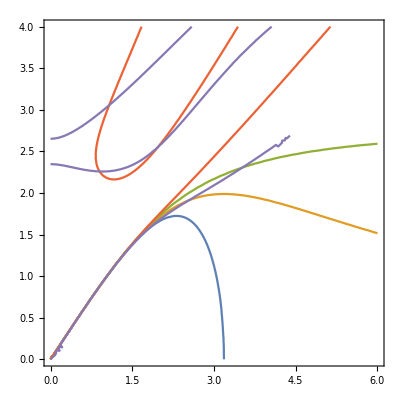

```mathematica
ContourPlot[{(Disp1/.{ν->1/3})==0,(Disp2/.{ν->1/3})==0,
(Disp3/.{ν->1/3})==0,(DispAll/.{ν->1/3})==0,
(Disp/.{ν->1/3})==0},{k,0,6},{ω,0,4}]
```

### Solitons

```mathematica
sbstTrig={Sinh[x_]^n_-> (Cosh[x]^2-1)^(n/2),Sinh[2x_]->2Sinh[x]Cosh[x],
Cosh[2x_]->2 Cosh[x]^2-1,Cosh[3 x_]-> Cosh[2x]Cosh[x]+Sinh[2x]Sinh[x],
Cosh[4 x_]->2(2 Cosh[x]^2-1)^2-1};
```

```mathematica
Cosh[3x]== Cosh[2x]Cosh[x]+Sinh[2x]Sinh[x]//Simplify
```

True

#### Boussinesq

```mathematica
EqTempl=D[u[x,t], t,t]-c^2 D[u[x,t], x,x]-β/(2ρ) D[u[x,t]^2,x,x]+(a/c^2 D[u[x,t], t,t,t,t]+b D[u[x,t], t,t,x,x]+d c^2 D[u[x,t], x,x,x,x])R^2;
```

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
```

```mathematica
EqTempl//Simplify
```

1/(2 c^2 ρ)A B^2 (3 (4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ)-2 (4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ) Cosh[2 B (-t v+x)]+(c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4) ρ Cosh[4 B (-t v+x)]) Sech[B (-t v+x)]^6

```mathematica
Solve[4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ==0&&4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ==0&&c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4==0,{v,B}]//Simplify
```

{{v→-(√(A β+3 c^2 ρ))/(√3 √ρ),B→-(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→-(√(A β+3 c^2 ρ))/(√3 √ρ),B→(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→(√(A β+3 c^2 ρ))/(√3 √ρ),B→-(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→(√(A β+3 c^2 ρ))/(√3 √ρ),B→(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))}}

```mathematica
Solve[4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ==0&&4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ==0&&c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4==0,{A,B}]//Simplify
```

{{A→(3 (-c^2+v^2) ρ)/β,B→-(c √(c^2-v^2))/(2 √(R^2 (c^4 d+b c^2 v^2+a v^4)))},{A→(3 (-c^2+v^2) ρ)/β,B→(c √(c^2-v^2))/(2 √(R^2 (c^4 d+b c^2 v^2+a v^4)))}}

```mathematica
Solve[c^4 d+b c^2 v2+a v2^2==0,v2]
```

{{v2→(-b c^2-√(b^2 c^4-4 a c^4 d))/(2 a)},{v2→(-b c^2+√(b^2 c^4-4 a c^4 d))/(2 a)}}

```mathematica
EqTemplDimless=D[u[x,t], t,t]-D[u[x,t], x,x]-ε β/(2Ε) D[u[x,t]^2,x,x]+δ^2(a D[u[x,t], t,t,t,t]+b D[u[x,t], t,t,x,x]+d D[u[x,t], x,x,x,x]);
```

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
```

```mathematica
EqTemplDimless//Simplify
```

1/(2 Ε)A B^2 (3 (4 A β ε+(1+44 B^2 d δ^2+44 a B^2 v^4 δ^2+v^2 (-1+44 b B^2 δ^2)) Ε)-2 (4 A β ε+(-1+v^2+52 B^2 d δ^2+52 b B^2 v^2 δ^2+52 a B^2 v^4 δ^2) Ε) Cosh[2 B (-t v+x)]+(-1+4 B^2 d δ^2+4 a B^2 v^4 δ^2+v^2 (1+4 b B^2 δ^2)) Ε Cosh[4 B (-t v+x)]) Sech[B (-t v+x)]^6

```mathematica
Solve[4 A β ε+(1+44 B^2 d δ^2+44 a B^2 v^4 δ^2+v^2 (-1+44 b B^2 δ^2)) Ε==0&&4 A β ε+(-1+v^2+52 B^2 d δ^2+52 b B^2 v^2 δ^2+52 a B^2 v^4 δ^2) Ε==0&&-1+4 B^2 d δ^2+4 a B^2 v^4 δ^2+v^2 (1+4 b B^2 δ^2)==0,{v,B}]//Simplify
```

{{v→-(√(A β ε+3 Ε))/(√3 √Ε),B→-((√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε)))))},{v→-(√(A β ε+3 Ε))/(√3 √Ε),B→(√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε))))},{v→(√(A β ε+3 Ε))/(√3 √Ε),B→-((√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε)))))},{v→(√(A β ε+3 Ε))/(√3 √Ε),B→(√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε))))}}

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
D[u[x,t],t]//Simplify
D[u[x,t],t,t]//Simplify
D[u[x,t],t,t,t]//Simplify
```

2 A B v Sech[B (-t v+x)]^2 Tanh[B (-t v+x)]

2 A B^2 v^2 (-2+Cosh[2 B (-t v+x)]) Sech[B (-t v+x)]^4

4 A B^3 v^3 (-5+Cosh[2 B (-t v+x)]) Sech[B (-t v+x)]^4 Tanh[B (-t v+x)]

```mathematica
EqTempl=D[u[x,t], t,t]-c^2 D[u[x,t], x,x]-β1/(2ρ) D[u[x,t]^2,x,x]-+(a/c^2 D[u[x,t], t,t,t,t]+b D[u[x,t], t,t,x,x]+d c^2 D[u[x,t], x,x,x,x])R^2;
```

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
(* PMMA *)
ρ=1180; Ε=4.9*10^9; ν=0.34;
l =-10.93*10^9; m= -7.73*10^9; n=-1.41*10^9;
```

```mathematica
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2
c=Sqrt[Ε/ρ];
```

-2.76429×10^10

```mathematica
R=0.01;
```

```mathematica
B[A_,a_,b_,d_]=Sqrt[(3A β c^2 ρ)/(-4 R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ)))];
V=Sqrt[(A β+3 c^2 ρ)/(3ρ)];
```

```mathematica
u1[A_] =  A (Cosh [B[A,(1+ν)/4,(-1-ν-ν^2)/2,(1+ν)/4] x])^-2;
u12[A_]=A (Cosh [B[A, (5-5ν-6 ν^2+4 ν^3)/(8(1-ν)),(-7+7ν+2 ν^2)/(8(1-ν)),1/4]x])^-2;
```

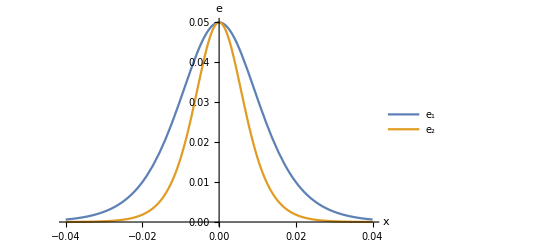

```mathematica
Amp=-0.05;
fig=Plot[{-u1[Amp], -u12[Amp]}, {x, -0.04, 0.04}, AxesLabel->{x,e}, PlotLegends->{"e_1","e_2"}(*TicksStyle->Medium*)]
```

```mathematica
Manipulate[Plot[{u1[A], u12[A]}, {x, -0.04, 0.04}, AxesLabel->{x,e},PlotRange->{0,.5}, PlotLegends->{"e_1","e_2"}],{A,0.1,0.5}]
```

```mathematica
(* Upper velocity limit *)
α11=(1+ν)/4;α21=(-1-ν-ν^2)/2;α31=α11;
α12=(5-5ν-6 ν^2+4 ν^3)/(8(1-ν));α22=-(7-7ν-2 ν^2)/(8(1-ν));α32=1/4;
c=Sqrt[Ε/ρ];
v[a_,b_,d_]=Sqrt[(-b +√(b^2-4 a d))/(2 a)c^2];
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
```

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
v[α11,α21,α31]^2/c^2-1
v[α12,α22,α32]^2/c^2-1
```

0.510509

0.184995

```mathematica
(3 (-c^2+v[α11,α21,α31]^2) ρ)/β//FullSimplify
(3 (-c^2+v[α12,α22,α32]^2) ρ)/β//FullSimplify
```

-0.204994

-0.0742847

#### Extended Boussinesq

```mathematica
EqTempl=(D[u[x,t], t,t]-c^2 D[u[x,t], x,x]-Subscript[β, 1] D[u[x,t]^2,x,x]-Subscript[β, 2] D[u[x,t]^3,x,x]+(Subscript[α, 1] D[u[x,t], t,t,t,t]+Subscript[α, 2] D[u[x,t], t,t,x,x]+Subscript[α, 3] D[u[x,t], x,x,x,x])
+Subscript[α, 1] D[u[x,t], t,t,t,t,t,t]+Subscript[γ, 2] D[u[x,t], t,t,t,t,x,x]+Subscript[γ, 3] D[u[x,t], t,t,x,x,x,x]+Subscript[γ, 4] D[u[x,t], x,x,x,x,x,x]);
```

```mathematica
u[x_,t_]=A Cosh[B(x-v t)]^-4;
```

```mathematica
EqTempl//Simplify
```

1/2 A B^2 Sech[B (-t v+x)]^10 (5 c^2-5 v^2+80 A β+5 c^2 Cosh[2 B (-t v+x)]-5 v^2 Cosh[2 B (-t v+x)]-64 A β Cosh[2 B (-t v+x)]-c^2 Cosh[4 B (-t v+x)]+v^2 Cosh[4 B (-t v+x)]-c^2 Cosh[6 B (-t v+x)]+v^2 Cosh[6 B (-t v+x)]+4 B^2 v^4 (55-13220 B^2 v^2+10 (1+1468 B^2 v^2) Cosh[2 B (-t v+x)]-(41+2276 B^2 v^2) Cosh[4 B (-t v+x)]+4 Cosh[6 B (-t v+x)]+64 B^2 v^2 Cosh[6 B (-t v+x)]) α_1+16 B^2 v^2 Cosh[B (-t v+x)]^2 (52-49 Cosh[2 B (-t v+x)]+4 Cosh[4 B (-t v+x)]) α_2+220 B^2 α_3+40 B^2 Cosh[2 B (-t v+x)] α_3-164 B^2 Cosh[4 B (-t v+x)] α_3+16 B^2 Cosh[6 B (-t v+x)] α_3-52880 B^4 v^4 γ_2+58720 B^4 v^4 Cosh[2 B (-t v+x)] γ_2-9104 B^4 v^4 Cosh[4 B (-t v+x)] γ_2+256 B^4 v^4 Cosh[6 B (-t v+x)] γ_2-52880 B^4 v^2 γ_3+58720 B^4 v^2 Cosh[2 B (-t v+x)] γ_3-9104 B^4 v^2 Cosh[4 B (-t v+x)] γ_3+256 B^4 v^2 Cosh[6 B (-t v+x)] γ_3-52880 B^4 γ_4+58720 B^4 Cosh[2 B (-t v+x)] γ_4-9104 B^4 Cosh[4 B (-t v+x)] γ_4+256 B^4 Cosh[6 B (-t v+x)] γ_4)

```mathematica
Eq2=5 c^2-5 v^2+80 A β+5 c^2 Cosh[2 B (-t v+x)]-5 v^2 Cosh[2 B (-t v+x)]-64 A β Cosh[2 B (-t v+x)]-c^2 Cosh[4 B (-t v+x)]+v^2 Cosh[4 B (-t v+x)]-c^2 Cosh[6 B (-t v+x)]+v^2 Cosh[6 B (-t v+x)]+4 B^2 v^4 (55-13220 B^2 v^2+10 (1+1468 B^2 v^2) Cosh[2 B (-t v+x)]-(41+2276 B^2 v^2) Cosh[4 B (-t v+x)]+4 Cosh[6 B (-t v+x)]+64 B^2 v^2 Cosh[6 B (-t v+x)]) Subscript[α, 1]+16 B^2 v^2 Cosh[B (-t v+x)]^2 (52-49 Cosh[2 B (-t v+x)]+4 Cosh[4 B (-t v+x)]) Subscript[α, 2]+220 B^2 Subscript[α, 3]+40 B^2 Cosh[2 B (-t v+x)] Subscript[α, 3]-164 B^2 Cosh[4 B (-t v+x)] Subscript[α, 3]+16 B^2 Cosh[6 B (-t v+x)] Subscript[α, 3]-52880 B^4 v^4 Subscript[γ, 2]+58720 B^4 v^4 Cosh[2 B (-t v+x)] Subscript[γ, 2]-9104 B^4 v^4 Cosh[4 B (-t v+x)] Subscript[γ, 2]+256 B^4 v^4 Cosh[6 B (-t v+x)] Subscript[γ, 2]-52880 B^4 v^2 Subscript[γ, 3]+58720 B^4 v^2 Cosh[2 B (-t v+x)] Subscript[γ, 3]-9104 B^4 v^2 Cosh[4 B (-t v+x)] Subscript[γ, 3]+256 B^4 v^2 Cosh[6 B (-t v+x)] Subscript[γ, 3]-52880 B^4 Subscript[γ, 4]+58720 B^4 Cosh[2 B (-t v+x)] Subscript[γ, 4]-9104 B^4 Cosh[4 B (-t v+x)] Subscript[γ, 4]+256 B^4 Cosh[6 B (-t v+x)] Subscript[γ, 4]//Simplify;
```

```mathematica
Coefficient[Eq2,Cosh[2 B (-t v+x)]]//Simplify
```

5 c^2-5 v^2-64 A β+40 (B^2 v^4+1468 B^4 v^6) α_1-784 B^2 v^2 Cosh[B (-t v+x)]^2 α_2+40 B^2 α_3+58720 B^4 v^4 γ_2+58720 B^4 v^2 γ_3+58720 B^4 γ_4

```mathematica
Coefficient[Eq2,Cosh[4 B (-t v+x)]]//Simplify
```

-c^2+v^2-4 B^2 v^4 (41+2276 B^2 v^2) α_1+64 B^2 v^2 Cosh[B (-t v+x)]^2 α_2-164 B^2 α_3-9104 B^4 v^4 γ_2-9104 B^4 v^2 γ_3-9104 B^4 γ_4

```mathematica
Coefficient[Eq2,Cosh[6B (-t v+x)]]//Simplify
```

-c^2+v^2+16 (B^2 v^4+16 B^4 v^6) α_1+16 B^2 α_3+256 B^4 v^4 γ_2+256 B^4 v^2 γ_3+256 B^4 γ_4

```mathematica
EqTempl=(D[u[x,t], t,t]-c^2 D[u[x,t], x,x]-Subscript[β, 1] D[u[x,t]^2,x,x]-Subscript[β, 2] D[u[x,t]^3,x,x]+(Subscript[α, 1] D[u[x,t], t,t,t,t]+Subscript[α, 2] D[u[x,t], t,t,x,x]+Subscript[α, 3] D[u[x,t], x,x,x,x])
+Subscript[α, 1] D[u[x,t], t,t,t,t,t,t]+Subscript[γ, 2] D[u[x,t], t,t,t,t,x,x]+Subscript[γ, 3] D[u[x,t], t,t,x,x,x,x]+Subscript[γ, 4] D[u[x,t], x,x,x,x,x,x]);
```

```mathematica
ClearAll[u,L2,A]
```

```mathematica
EqTempl=((k-1)u[x]+a2 u[x]^2+a3 u[x]^3+a4(k^2 α1+k α2+α3) u''[x]
+a4(k^2 γ1/2+k(γ2+γ3/2+γ4)+γ6+γ7)u'[x]^2+a4(k^2 γ1+k(γ3+2γ4+γ5)+γ6) u[x]u''[x]
+a4^2(k^3 α4+k^2 α5+k α6+α7)u''''[x])
```

(-1+k) u[x]+a2 u[x]^2+a3 u[x]^3+a4 ((k^2 γ1)/2+k (γ2+γ3/2+γ4)+γ6+γ7) u'[x]^2+a4 (k^2 α1+k α2+α3) u''[x]+a4 (k^2 γ1+k (γ3+2 γ4+γ5)+γ6) u[x] u''[x]+a4^2 (k^3 α4+k^2 α5+k α6+α7) u^(4)[x]

```mathematica
u[x_]=A/Cosh[x/L]
```

A Sech[x/L]

```mathematica
Cosh[x]^2-1==Sinh[x]^2//Simplify
1-1/Cosh[x]^2==Tanh[x]^2//Simplify
Sinh[2 x]==2Sinh[x]Cosh[x]//Simplify
Cosh[2x]==2 Cosh[x]^2-1//Simplify
```

True

True

True

«1 more identical outputs»

```mathematica
eq=Cosh[x/L]^5 EqTempl/A//Simplify;
```

```mathematica
sbst={Sinh[x/L]^2-> Cosh[x/L]^2-1,Sinh[(2 x)/L]^2->4(Cosh[x/L]^2-1)Cosh[x/L]^2,
Sinh[(2 x)/L]^4->16(Cosh[x/L]^2-1)^2 Cosh[x/L]^4,Cosh[(2x)/L]->2 Cosh[x/L]^2-1,
Sinh[(2 x)/L]->2Sinh[x/L]Cosh[x/L],Sinh[x/L]^4->( Cosh[x/L]^2-1)^2,Cosh[(4 x)/L]->2(2 Cosh[x/L]^2-1)^2-1};
```

```mathematica
cf=CoefficientList[(L^4 eq/.sbst)(*/.{L^2->L2,L^4->L2^2}*),Cosh[x/L]]//Simplify
```

{24 a4^2 (k^3 α4+k^2 α5+k α6+α7),-1/2 A a4 L^2 (5 k^2 γ1+k (2 γ2+5 γ3+10 γ4+4 γ5)+2 (3 γ6+γ7)),A^2 a3 L^4-2 a4 L^2 (k^2 α1+k α2+α3)-20 a4^2 (k^3 α4+k^2 α5+k α6+α7),A a2 L^4+1/2 A a4 L^2 (3 k^2 γ1+k (2 γ2+3 γ3+6 γ4+2 γ5)+2 (2 γ6+γ7)),(-1+k) L^4+a4 L^2 (k^2 α1+k α2+α3)+a4^2 (k^3 α4+k^2 α5+k α6+α7)}

```mathematica
ClearAll[L2]
```

```mathematica
Solve[cf[[5]]==0,L2]//Simplify
```

{{L2→-(2 (a4 k^2 α1+a4 k α2+a4 α3+√(a4^2 ((k^2 α1+k α2+α3)^2-4 (-1+k) (k^3 α4+k^2 α5+k α6+α7)))))/(-1+k)},{L2→-(2 (a4 k^2 α1+a4 k α2+a4 α3-√(a4^2 ((k^2 α1+k α2+α3)^2-4 (-1+k) (k^3 α4+k^2 α5+k α6+α7)))))/(-1+k)}}

```mathematica
L2=-(2 (a4 k^2 α1+a4 k α2+a4 α3-√(a4^2 ((k^2 α1+k α2+α3)^2-4 (-1+k) (k^3 α4+k^2 α5+k α6+α7)))))/(-1+k);
```

```mathematica
A=Solve[{cf[[3]]==0},{A}][[1,1,2]]//Simplify;
```

```mathematica
Solve[(cf[[1]]//Simplify)==0,k]
```

$Aborted

```mathematica
cf[[1]]//Simplify
```

#### Gardner (KdV with quadratic and cubic nonlinearities)

```mathematica
tBqRed
```

v^(0,1)[ξ,τ]-(β1 v[ξ,τ] v^(1,0)[ξ,τ])/Ε-1/2 q1 v^(3,0)[ξ,τ]+1/(8 Ε^2)ε (4 ((-1+2 a2) β1^2-3 β4+a3 β1 Ε) v[ξ,τ]^2 v^(1,0)[ξ,τ]+4 Ε (-q3+2 (2 α1+α2) β1+q1 (-β1+4 a2 β1+3 a3 Ε)) v[ξ,τ] v^(3,0)[ξ,τ]+Ε (2 (-2 q2-8 a1 β1+3 (-q1 β1+6 a2 q1 β1+8 α1 β1+4 α2 β1+2 a3 q1 Ε)) v^(1,0)[ξ,τ] v^(2,0)[ξ,τ]+((-1+6 a2) q1^2-4 q4+4 q1 (2 α1+α2)) Ε v^(5,0)[ξ,τ]))

```mathematica
ClearAll[u]
```

```mathematica
tEq=1/c Derivative[0,1][u][ξ,τ]-(β1 u[ξ,τ] Derivative[1,0][u][ξ,τ])/Ε-(R^2 q1)/2 Derivative[3,0][u][ξ,τ]-(3β4)/(2 Ε^2) u[ξ,τ]^2 Derivative[1,0][u][ξ,τ];
```

```mathematica
u[ξ_,τ_]=A/(1+B Cosh[F(ξ-v τ)]);
```

```mathematica
eq=(tEq(4 c Ε^2 (1+B Cosh[F (ξ-v τ)])^4)/(-A B F Sinh[F (ξ-v τ)] ))//Simplify
```

-2 (3 A^2 c β4+2 A c β1 Ε+c F^2 q1 R^2 Ε^2-11/2 B^2 c F^2 q1 R^2 Ε^2+2 v Ε^2+B^2 v Ε^2+2 B Ε (A c β1+2 (-c F^2 q1 R^2+v) Ε) Cosh[F (ξ-v τ)]+1/2 B^2 (c F^2 q1 R^2+2 v) Ε^2 Cosh[2 F (ξ-v τ)])

```mathematica
cl=CoefficientList[eq/.sbstTrig,Cosh[F (ξ-v τ)]]
```

{-6 A^2 c β4-4 A c β1 Ε-2 c F^2 q1 R^2 Ε^2+11 B^2 c F^2 q1 R^2 Ε^2-4 v Ε^2-2 B^2 v Ε^2+B^2 (c F^2 q1 R^2+2 v) Ε^2,-4 B Ε (A c β1+2 (-c F^2 q1 R^2+v) Ε),-2 B^2 (c F^2 q1 R^2+2 v) Ε^2}

```mathematica
v=Solve[cl[[3]]==0,v][[1,1,2]]
```

-1/2 c F^2 q1 R^2

```mathematica
Solve[cl[[2]]==0,F]
```

{{F→-(√A √β1)/(√3 √q1 R √Ε)},{F→(√A √β1)/(√3 √q1 R √Ε)}}

```mathematica
F=(√A √β1)/(√3 √q1 R √Ε);
```

```mathematica
v
```

-(A c β1)/(6 Ε)

```mathematica
Solve[cl[[1]]==0,B]
```

{{B→-(√(3 A β4+2 β1 Ε))/(√2 √β1 √Ε)},{B→(√(3 A β4+2 β1 Ε))/(√2 √β1 √Ε)}}

```mathematica
((√(-3 A β4+2 β1 Ε))/(√2 √β1 √Ε))^2
```

(-3 A β4+2 β1 Ε)/(2 β1 Ε)

```mathematica
uGardnerDim[ξ_,τ_]=A/(1+((3 A β4+2 β1 Ε)/(2 β1 Ε))^(1/2) Cosh[((A β1)/(3 R^2 q1 Ε))^(1/2)(ξ+(A c β1)/(6 Ε) τ)]);
```

```mathematica
uGardnerNondim[ξ_,τ_]=A/(1+((3 A ε β4+2 β1 Ε)/(2 β1 Ε))^(1/2) Cosh[((A β1)/(3q1 Ε))^(1/2)(ξ+(A β1)/(6 Ε) τ)])(*/.{β1->ε β1,β4->ε β4,q1->ε q1}*);
```

```mathematica
u[x_,t_]=uGardnerDim[x,t];
tEq//Simplify
ClearAll[u]
```

0

```mathematica
tEqNondim=Derivative[0,1][u][ξ,τ]-(β1 u[ξ,τ] Derivative[1,0][u][ξ,τ])/Ε-q1/2 Derivative[3,0][u][ξ,τ]-ε(3β4)/(2 Ε^2) u[ξ,τ]^2 Derivative[1,0][u][ξ,τ];
u[x_,t_]=uGardnerNondim[x,t];
tEqNondim//Simplify
ClearAll[u,tEqNondim]
```

0

#### Extended KdV (based on Gardner eq’n)

```mathematica
tBqRed
```

```mathematica
tEq=1/c Derivative[0,1][u][ξ,τ]-(β1 u[ξ,τ] Derivative[1,0][u][ξ,τ])/Ε-R^2 1/2 q1 Derivative[3,0][u][ξ,τ]+ 1/2((-(β4+β1(2a2 β1+a3)))/Ε^2 u[ξ,τ]^2 Derivative[1,0][u][ξ,τ]-(q3 R^2)/Ε u[ξ,τ] Derivative[3,0][u][ξ,τ]- (q2 R^2)/Ε Derivative[1,0][u][ξ,τ] Derivative[2,0][u][ξ,τ]-q4 R^4 Derivative[5,0][u][ξ,τ]);
```

```mathematica
ClearAll[u]
```

```mathematica
tEqNondim=(Derivative[0,1][u][ξ,τ]-(β1 u[ξ,τ] Derivative[1,0][u][ξ,τ])/Ε-1/2 q1 Derivative[3,0][u][ξ,τ]
+ ε/2((-(β4+β1(2a2 β1+a3 Ε)))/Ε^2 u[ξ,τ]^2 Derivative[1,0][u][ξ,τ]-(q3+β1(q1-2(2α1+α2)))/Ε u[ξ,τ] Derivative[3,0][u][ξ,τ]
-(q2+3β1/2(q1-4(2α1+α2)))/Ε Derivative[1,0][u][ξ,τ] Derivative[2,0][u][ξ,τ]
-(q4-q1(2α1+α2)+q1^2/4) Derivative[5,0][u][ξ,τ]));
```

```mathematica
u[x_,t_]=uG[x,t]-ε(a1 D[uG[x,t], x,x]+a2 x D[uG[x,t], t]+a3 Derivative[1,0][uG][x,t]Derivative[-1,0][uG][x,t]);
```

```mathematica
sbstTauDer3={ε Derivative[0,2][fun_][x_,t_]->ε((β1 D[(fun[x,t]^2), x,t])/(2Ε)+1/2 q1 Derivative[3,1][fun][x,t]),
ε Derivative[n_,1][fun_][x_,t_]->ε((β1 D[(fun[x,t]^2), {x,n+1}])/(2Ε)+q1/2 Derivative[n+3,0][fun][x,t])};
```

```mathematica
tEqNondim//ByteCount
```

1818760

```mathematica
tEqNondim=Expand[tEqNondim]/.sbstTauDer3;
```

```mathematica
cl=CoefficientList[(Expand[tEqNondim]/.sbstTauDer3),ε,2];
```

1
 |  |  |  |

```mathematica
Length[cl]
```

5

```mathematica
cl[[1]]//Simplify
```

uG^(0,1)[ξ,τ]-(β1 uG[ξ,τ] uG^(1,0)[ξ,τ])/Ε-1/2 q1 uG^(3,0)[ξ,τ]

```mathematica
(Coefficient[cl[[2]]//Expand,ξ])//Simplify
```

0

```mathematica
cl[[2]]//Simplify
```

-(β4 uG[ξ,τ]^2 uG^(1,0)[ξ,τ])/(2 Ε^2)

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["nl3_state8.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["nl3_state8.mx"];
```

```mathematica
tEqNondim//Simplify
```

```mathematica
ClearAll[A,F,B,v,u]
```

```mathematica
u[ξ_,τ_]= A/(1+B1 Cosh[F(ξ-v τ)]+B2 Cosh[F(ξ-v τ)]^2);
```

```mathematica
eq=tEq/A/(16 c Ε^2 (1+B1 Cosh[F (ξ-v τ)]+B2 Cosh[F (ξ-v τ)]^2)^6) //Simplify
```

(2 A^2 c F β4 (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^2 Sinh[F (ξ-v τ)]+2 A c F β1 Ε (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^3 Sinh[F (ξ-v τ)]+F v Ε^2 (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^4 Sinh[F (ξ-v τ)]-A c F^3 q2 R^2 Ε (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)]) (-6 B1^2-6 B2^2-B1 (4+15 B2) Cosh[F (ξ-v τ)]+2 (B1^2-2 B2 (2+B2)) Cosh[2 F (ξ-v τ)]+3 B1 B2 Cosh[3 F (ξ-v τ)]+2 B2^2 Cosh[4 F (ξ-v τ)]) Sinh[F (ξ-v τ)]+8 A c q3 R^2 Ε (1+B1 Cosh[F (ξ-v τ)]+B2 Cosh[F (ξ-v τ)]^2) (1/4 F^3 (B1+8 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^2 Sinh[F (ξ-v τ)]-3 F^3 (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)]) (B1 Cosh[F (ξ-v τ)]+2 B2 Cosh[2 F (ξ-v τ)]) Sinh[F (ξ-v τ)]+6 (B1 F Sinh[F (ξ-v τ)]+B2 F Sinh[2 F (ξ-v τ)])^3)+8 c q1 R^2 Ε^2 (1+B1 Cosh[F (ξ-v τ)]+B2 Cosh[F (ξ-v τ)]^2)^2 (1/4 F^3 (B1+8 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^2 Sinh[F (ξ-v τ)]-3 F^3 (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)]) (B1 Cosh[F (ξ-v τ)]+2 B2 Cosh[2 F (ξ-v τ)]) Sinh[F (ξ-v τ)]+6 (B1 F Sinh[F (ξ-v τ)]+B2 F Sinh[2 F (ξ-v τ)])^3)+8 c q4 R^4 Ε^2 (1/16 F^5 (B1+32 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^4 Sinh[F (ξ-v τ)]-5/2 F^5 (B1+8 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^3 (B1 Cosh[F (ξ-v τ)]+2 B2 Cosh[2 F (ξ-v τ)]) Sinh[F (ξ-v τ)]+45/2 F^5 (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^2 (B1 Cosh[F (ξ-v τ)]+2 B2 Cosh[2 F (ξ-v τ)])^2 Sinh[F (ξ-v τ)]-5/4 F^5 (B1+2 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^3 (B1 Cosh[F (ξ-v τ)]+8 B2 Cosh[2 F (ξ-v τ)]) Sinh[F (ξ-v τ)]+15 F^5 (B1+2 B2 Cosh[F (ξ-v τ)])^2 (B1+8 B2 Cosh[F (ξ-v τ)]) (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)])^2 Sinh[F (ξ-v τ)]^3-120 F^5 (B1+2 B2 Cosh[F (ξ-v τ)])^3 (2+B2+2 B1 Cosh[F (ξ-v τ)]+B2 Cosh[2 F (ξ-v τ)]) (B1 Cosh[F (ξ-v τ)]+2 B2 Cosh[2 F (ξ-v τ)]) Sinh[F (ξ-v τ)]^3+120 (B1 F Sinh[F (ξ-v τ)]+B2 F Sinh[2 F (ξ-v τ)])^5))/(256 c^2 Ε^4 (1+B1 Cosh[F (ξ-v τ)]+B2 Cosh[F (ξ-v τ)]^2)^12)

```mathematica
cl=CoefficientList[((eq/.sbstTrig)/.sbstTrig)/.sbstTrig,Cosh[F (ξ-v τ)]]//Simplify
```

CoefficientList::poly: (2 A^2 c F β4 (B1+2 B2 Cosh[F Plus[«2»]]) (2+B2+2 B1 Cosh[Times[«2»]]+B2 (-1+Times[«2»]))^2 Sinh[F (ξ-v τ)]+2 A «6» Sinh[F (ξ-v τ)]+«4»+8 c «4» («1»)+8 c q4 R^4 Ε^2 («9»+«1»))/(256 c^2 Ε^4 (1+B1 Cosh[F (ξ+Times[«3»])]+B2 Cosh[F Plus[«2»]]^2)^12) is not a polynomial.

$Aborted

```mathematica
For[i=1,i≤Length[cl],i++,Print@Simplify@cl[[i]]];
```

4 B^2 F^2 (A^2 c β4+A c (6 B^2 F^2 (q2-2 q3) R^2+F^2 q3 R^2+2 β1) Ε+(c F^2 R^2 (q1-12 B^2 q1+(1-120 B^2+360 B^4) F^2 q4 R^2)+2 v) Ε^2)

4 B^3 F^2 Ε (A c (F^2 (2 q2-7 q3) R^2+4 β1)+(-(5+24 B^2) c F^2 q1 R^2+(-41+360 B^2) c F^4 q4 R^4+8 v) Ε)

-4 B^4 F^2 Ε (A (4 c F^2 (q2-q3) R^2-2 c β1)+3 ((3+4 B^2) c F^2 q1 R^2+(-57+80 B^2) c F^4 q4 R^4-4 v) Ε)

4 B^5 F^2 (c F^2 q1 R^2-131 c F^4 q4 R^4+8 v) Ε^2

8 B^6 F^2 (2 c F^2 R^2 (q1+4 F^2 q4 R^2)+v) Ε^2

```mathematica
v=Solve[cl[[5]]==0,v][[1,1,2]]//Simplify
```

-2 c F^2 R^2 (q1+4 F^2 q4 R^2)

```mathematica
Solve[cl[[3]]==0,F]//Simplify
```

{{F→0},{F→-(√(-(A q2 R^2-A q3 R^2+3 q1 R^2 Ε+√(R^4 (120 A q4 β1 Ε+(A (q2-q3)+3 q1 Ε)^2)))/(q4 R^4 Ε)))/(2 √30)},{F→(√(-(A q2 R^2-A q3 R^2+3 q1 R^2 Ε+√(R^4 (120 A q4 β1 Ε+(A (q2-q3)+3 q1 Ε)^2)))/(q4 R^4 Ε)))/(2 √30)},{F→-(√((-A q2 R^2+A q3 R^2-3 q1 R^2 Ε+√(R^4 (120 A q4 β1 Ε+(A (q2-q3)+3 q1 Ε)^2)))/(q4 R^4 Ε)))/(2 √30)},{F→(√((-A q2 R^2+A q3 R^2-3 q1 R^2 Ε+√(R^4 (120 A q4 β1 Ε+(A (q2-q3)+3 q1 Ε)^2)))/(q4 R^4 Ε)))/(2 √30)}}

```mathematica
F=(√((-A q2 R^2+A q3 R^2-3 q1 R^2 Ε+√(R^4 (120 A q4 β1 Ε+(A (q2-q3)+3 q1 Ε)^2)))/(q4 R^4 Ε)))/(2 √30);
```

```mathematica
Solve[cl[[1]]==0,A]//Simplify
```

{{A→0},{A→-((3 (-2 q3^2 β1 Ε+20 q4 β1 β4 Ε+q2 (q3 β1+q1 β4) Ε+√((q3 β1-q1 β4)^2 (q2^2-4 q2 q3+4 q3^2-40 q4 β4) Ε^2)))/(2 β4 (q2 q3-q3^2+10 q4 β4)))},{A→(3 (2 q3^2 β1 Ε-20 q4 β1 β4 Ε-q2 (q3 β1+q1 β4) Ε+√((q3 β1-q1 β4)^2 (q2^2-4 q2 q3+4 q3^2-40 q4 β4) Ε^2)))/(2 β4 (q2 q3-q3^2+10 q4 β4))}}

### 2nd Method: multiscale expansion

```mathematica
USeries[x_,r_,t_]=U0[x,r,t](*+U1[x,r,t]δ*)+U2[x,r,t] δ^2(*+U3[x,r,t] δ^3*)+U4[x,r,t] δ^4;
VSeries[x_,r_,t_]=V0[x,r,t]+V1[x,r,t]δ(*+V2[x,r,t] δ^2*)+V3[x,r,t] δ^3(*+V4[x,r,t] δ^4*)+V5[x,r,t] δ^5;
```

```mathematica
V0[x_,r_,t_]=CV0[x,t]r+ε FV0[x,r,t];
```

```mathematica
U0[x_,r_,t_]=U0[x,t]+ε FU0[x,r,t];
```

```mathematica
CV0[x_,t_]=0;
FV0[x_,r_,t_]=0;
FU0[x_,r_,t_]=0;
```

```mathematica
V1[x_,r_,t_]=CV1[x,t]r+ε FV1[x,r,t];
(* CV1[x_,t_]=(μ(3λ+2μ)S[x,t]-λ(λ+μ)∂_x U0[x,t])/(2(λ+μ)^2) *)
(*FV1[x_,r_,t_]=CFV1[x,t]r;*)
(*CFV1[x_,t_]=1/(8 (λ+μ)^5)(-μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2+2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t]∂_x U0[x,t]-(λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (∂_x U0[x,t])^2);*)
```

```mathematica
ClearAll[CFV1, FV1, V1];
```

```mathematica
ClearAll[U2];
```

```mathematica
U2[x_,r_,t_]=r^2/4(1/μ s^2 ρ D[U0[x,t], t,t]-2 D[U0[x,t], x,x]-(3 λ+2 μ)/(λ+μ)D[S[x,t], x])+ε FU2[x,r,t];
(*FU2[x_,r_,t_]=1/(16 μ^2 (λ+μ)^2)(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(1,0)[x,t]+n r^2 λ^2 S^(1,0)[x,t] U0^(1,0)[x,t]-8 m r^2 λ μ S^(1,0)[x,t] U0^(1,0)[x,t]+4 n r^2 λ μ S^(1,0)[x,t] U0^(1,0)[x,t]+2 r^2 λ^2 μ S^(1,0)[x,t] U0^(1,0)[x,t]-4 m r^2 μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+2 n r^2 μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+6 r^2 λ μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+4 r^2 μ^3 S^(1,0)[x,t] U0^(1,0)[x,t]-3 n r^2 λ^2 μ U0^(1,0)[x,t] U0^(2,0)[x,t]-12 m r^2 λ μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-2 n r^2 λ μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-12 r^2 λ^2 μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-8 m r^2 μ^3 U0^(1,0)[x,t] U0^(2,0)[x,t]-20 r^2 λ μ^3 U0^(1,0)[x,t] U0^(2,0)[x,t]-8 r^2 μ^4 U0^(1,0)[x,t] U0^(2,0)[x,t]+r^2 S[x,t] (-(4 m-n) s^2 (λ+μ) ρ U0^(0,2)[x,t]+(4 m-n) (λ+2 μ) S^(1,0)[x,t]+μ (n λ-2 (λ^2-2 m μ+λ μ)) U0^(2,0)[x,t]));*)
```

```mathematica
n r^2 λ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]-8 m r^2 λ μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+4 n r^2 λ μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+2 r^2 λ^2 μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]-4 m r^2 μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+2 n r^2 μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+6 r^2 λ μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+4 r^2 μ^3 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]//Simplify
```

r^2 (n (λ^2+4 λ μ+2 μ^2)+2 μ (λ^2+3 λ μ+2 μ^2-2 m (2 λ+μ))) S^(1,0)[x,t] U0^(1,0)[x,t]

```mathematica
c1[x_,t_]=1/(16 (λ+μ)^2 (λ+2 μ))(-2 s^2 λ ρ Derivative[0,2][S][x,t]-3 s^2 μ ρ Derivative[0,2][S][x,t]+3 s^2 λ^2 ρ Derivative[1,2][U0][x,t]+7 s^2 λ μ ρ Derivative[1,2][U0][x,t]+3 s^2 μ^2 ρ Derivative[1,2][U0][x,t]-λ^2 Derivative[2,0][S][x,t]-2 λ μ Derivative[2,0][S][x,t]-4 λ^2 μ Derivative[3,0][U0][x,t]-11 λ μ^2 Derivative[3,0][U0][x,t]-6 μ^3 Derivative[3,0][U0][x,t]);
V3[x_,r_,t_]=1/(16 μ (λ^2+3 λ μ+2 μ^2))(s^2 μ ρ Derivative[0,2][S][x,t]-s^2 λ^2 ρ Derivative[1,2][U0][x,t]-3 s^2 λ μ ρ Derivative[1,2][U0][x,t]-s^2 μ^2 ρ Derivative[1,2][U0][x,t]+λ^2 Derivative[2,0][S][x,t]+2 λ μ Derivative[2,0][S][x,t]+2 λ^2 μ Derivative[3,0][U0][x,t]+5 λ μ^2 Derivative[3,0][U0][x,t]+2 μ^3 Derivative[3,0][U0][x,t])r^3+c1[x,t]r+ε FV3[x,r,t];
```

```mathematica
U4[x_,r_,t_]=1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]-r^2 s^2 (-2 μ (2 λ+3 μ)+r^2 (λ^2+4 λ μ+3 μ^2)) ρ Derivative[1,2][S][x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+(λ+2 μ) (2 r^2 (λ+r^2 λ+r^2 μ) Derivative[3,0][S][x,t]+r^2 μ ((8+3 r^2) λ+3 (2+r^2) μ) Derivative[4,0][U0][x,t])))+ε FU4[x,r,t];
```

```mathematica
ClearAll[V1,U2,V3,U4,c1];
```

```mathematica
1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+μ (λ+2 μ) (r^2 ((8+3 r^2) λ+3 (2+r^2) μ) Derivative[4,0][U0][x,t])))/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

```mathematica
FU2[x,r,t]/.ForPrint/.ForPrint2
```

1/(16 μ^2 (λ+μ)^2)(n r^2 λ^2 S_x U_0_x-8 m r^2 λ μ S_x U_0_x+4 n r^2 λ μ S_x U_0_x+2 r^2 λ^2 μ S_x U_0_x-4 m r^2 μ^2 S_x U_0_x+2 n r^2 μ^2 S_x U_0_x+6 r^2 λ μ^2 S_x U_0_x+4 r^2 μ^3 S_x U_0_x-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U_0_x U_0_tt-3 n r^2 λ^2 μ U_0_x U_0_xx-12 m r^2 λ μ^2 U_0_x U_0_xx-2 n r^2 λ μ^2 U_0_x U_0_xx-12 r^2 λ^2 μ^2 U_0_x U_0_xx-8 m r^2 μ^3 U_0_x U_0_xx-20 r^2 λ μ^3 U_0_x U_0_xx-8 r^2 μ^4 U_0_x U_0_xx+r^2 S[x,t] ((4 m-n) (λ+2 μ) S_x+(-4 m+n) s^2 (λ+μ) ρ U_0_tt+μ (n λ-2 (λ^2-2 m μ+λ μ)) U_0_xx))

```mathematica
V3[x,r,t]/.ForPrint/.ForPrint2/.ForLatex//FullSimplify
```

ε FV3[x,r,t]+1/(16 μ (λ+μ)^2 (λ+2 μ))r (s^2 μ ((-2+r^2) λ+(-3+r^2) μ) ρ S_(t,t)+λ (λ+2 μ) (-μ+r^2 (λ+μ)) S_(x,x)-s^2 (r^2 (λ+μ) (λ^2+3 λ μ+μ^2)-μ (3 λ^2+7 λ μ+3 μ^2)) ρ U_(0,x,t,t)+μ (λ+2 μ) (r^2 (λ+μ) (2 λ+μ)-μ (4 λ+3 μ)) U_(0,x,x,x))

```mathematica
r^2 (λ+μ) (λ^2+3 λ μ+μ^2)-μ (3 λ^2+7 λ μ+3 μ^2)-(λ+2μ)(r^2 (λ+μ) (2 λ+μ)-μ (4 λ+3 μ))//Simplify
```

-(λ+μ) (r^2 (λ+μ)^2-μ (λ+3 μ))

#### Equations

```mathematica
ClearAll[U4]
```

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales2;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧) L/ε/.Scales2;
ndEq1=Coefficient[ndEq1,ε,0]+Coefficient[ndEq1,ε,1]ε;
ndEq2=Coefficient[ndEq2,ε,0]+Coefficient[ndEq2,ε,1]ε;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
Coefficient[ndEq1,δ,-2]//Simplify
```

-1/(2 r)ε (FU0^(0,2,0)[x,r,t] (ε (2 m-n+2 λ) V1[x,r,t]+2 r (μ+ε (m+λ+2 μ) U0^(1,0)[x,t]+ε (m+λ+2 μ) V1^(0,1,0)[x,r,t]+m ε^2 FU0^(1,0,0)[x,r,t]+ε^2 λ FU0^(1,0,0)[x,r,t]+2 ε^2 μ FU0^(1,0,0)[x,r,t]))+FU0^(0,1,0)[x,r,t] (2 ε (m+λ+2 μ) U0^(1,0)[x,t]+ε (4 m-n+4 (λ+μ)) V1^(0,1,0)[x,r,t]+2 (μ+r ε (m+λ+2 μ) V1^(0,2,0)[x,r,t]+ε^2 (m+λ+2 μ) FU0^(1,0,0)[x,r,t]+2 m r ε^2 FU0^(1,1,0)[x,r,t]+2 r ε^2 λ FU0^(1,1,0)[x,r,t]+4 r ε^2 μ FU0^(1,1,0)[x,r,t])))

```mathematica
cl1=CoefficientList[ndEq1 δ,{ε,δ},{2,4}];
cl2=CoefficientList[ndEq2 δ,{ε,δ},{3,4}];
```

```mathematica
ndEq1red=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,2⟧δ+cl1⟦1,3⟧δ^2;
CoefficientList[ndEq1red,{ε,δ},{2,4}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{0,(-μ U_(2,r)-(λ+μ) V_(1,x)+r (s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x)-μ U_(2,r,r)-λ V_(1,x,r)-μ V_(1,x,r)))/r,0,0},{0,0,0,0}}

```mathematica
ndEq2red=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,2⟧δ+cl2⟦1,3⟧δ^2;
CoefficientList[ndEq2red,{ε,δ},{2,4}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{((λ+2 μ) (V_1-r (V_(1,r)+r V_(1,r,r))))/r^2,0,((λ+2 μ) V_3-r ((λ+2 μ) V_(3,r)+r ((λ+μ) U_(2,x,r)-s^2 ρ V_(1,t,t)+μ V_(1,x,x)+λ V_(3,r,r)+2 μ V_(3,r,r))))/r^2,0},{1/r^3((2 l+2 m+2 λ+3 μ) V_1^2+r (2 l+λ) V_1 (U_(0,x)-r V_(1,r,r))-r^2 ((2 l+λ) U_(0,x) (V_(1,r)+r V_(1,r,r))+V_(1,r) ((2 l+2 m+2 λ+3 μ) V_(1,r)+r (2 l+4 m+3 λ+6 μ) V_(1,r,r)))),0,0,0}}

```mathematica
Coefficient[cl2⟦1+1,1+0⟧, Derivative[1,0][U0][x,t]]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((2 l+λ) (V_1-r (V_(1,r)+r V_(1,r,r))))/r^2

```mathematica
Coefficient[cl2⟦1+1,1+0⟧, Derivative[1,0][U0][x,t],0]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((2 l+2 m+2 λ+3 μ) V_1^2-r^2 (2 l+λ) V_1 V_(1,r,r)-r^2 V_(1,r) ((2 l+2 m+2 λ+3 μ) V_(1,r)+r (2 l+4 m+3 λ+6 μ) V_(1,r,r)))/r^3

```mathematica
Solve[-128 r^2 μ^2 (λ^2+3 λ μ+2 μ^2) c2[x,t]-32 μ^2 (λ^2+3 λ μ+2 μ^2) c3[x,t]+2 r^2 s^4 λ^2 ρ^2 Derivative[0,4][U0][x,t]+6 r^2 s^4 λ μ ρ^2 Derivative[0,4][U0][x,t]+4 r^2 s^4 μ^2 ρ^2 Derivative[0,4][U0][x,t]-2 r^2 s^2 λ^2 ρ Derivative[1,2][S][x,t]+2 s^2 λ μ ρ Derivative[1,2][S][x,t]-8 r^2 s^2 λ μ ρ Derivative[1,2][S][x,t]+3 s^2 μ^2 ρ Derivative[1,2][S][x,t]-6 r^2 s^2 μ^2 ρ Derivative[1,2][S][x,t]-3 s^2 λ^2 μ ρ Derivative[2,2][U0][x,t]-6 r^2 s^2 λ^2 μ ρ Derivative[2,2][U0][x,t]-7 s^2 λ μ^2 ρ Derivative[2,2][U0][x,t]-20 r^2 s^2 λ μ^2 ρ Derivative[2,2][U0][x,t]-3 s^2 μ^3 ρ Derivative[2,2][U0][x,t]-14 r^2 s^2 μ^3 ρ Derivative[2,2][U0][x,t]+λ^2 μ Derivative[3,0][S][x,t]+4 r^2 λ^2 μ Derivative[3,0][S][x,t]+2 λ μ^2 Derivative[3,0][S][x,t]+12 r^2 λ μ^2 Derivative[3,0][S][x,t]+8 r^2 μ^3 Derivative[3,0][S][x,t]+4 λ^2 μ^2 Derivative[4,0][U0][x,t]+6 r^2 λ^2 μ^2 Derivative[4,0][U0][x,t]+11 λ μ^3 Derivative[4,0][U0][x,t]+18 r^2 λ μ^3 Derivative[4,0][U0][x,t]+6 μ^4 Derivative[4,0][U0][x,t]+12 r^2 μ^4 Derivative[4,0][U0][x,t]==0,c1]
```

{{c1→1/(16 (λ+μ)^2 (λ+2 μ))(-2 s^2 λ ρ S^(0,2)[x,t]-3 s^2 μ ρ S^(0,2)[x,t]+3 s^2 λ^2 ρ U0^(1,2)[x,t]+7 s^2 λ μ ρ U0^(1,2)[x,t]+3 s^2 μ^2 ρ U0^(1,2)[x,t]-λ^2 S^(2,0)[x,t]-2 λ μ S^(2,0)[x,t]-4 λ^2 μ U0^(3,0)[x,t]-11 λ μ^2 U0^(3,0)[x,t]-6 μ^3 U0^(3,0)[x,t])}}

```mathematica
DSolve[2 r^3 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]+r s^2 (μ (2 λ+3 μ)-2 r^2 (λ^2+4 λ μ+3 μ^2)) ρ Derivative[1,2][S][x,t]+μ (-r s^2 ((3+6 r^2) λ^2+(7+20 r^2) λ μ+(3+14 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+(λ+2 μ) (r (λ+4 r^2 λ+4 r^2 μ) Derivative[3,0][S][x,t]+r μ (4 λ+6 r^2 λ+3 μ+6 r^2 μ) Derivative[4,0][U0][x,t]-8 μ (λ+μ) (f'[r]+r f''[r])))==0,f,r]
```

{{f→Function[{r},C[2]+1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 U0^(0,4)[x,t]-r^2 s^2 (-2 μ (2 λ+3 μ)+r^2 (λ^2+4 λ μ+3 μ^2)) ρ S^(1,2)[x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ U0^(2,2)[x,t]+(λ+2 μ) (64 μ (λ+μ) C[1] Log[r]+2 r^2 (λ+r^2 λ+r^2 μ) S^(3,0)[x,t]+r^2 μ ((8+3 r^2) λ+3 (2+r^2) μ) U0^(4,0)[x,t])))]}}

```mathematica
DSolve[-1/(4 r μ (λ+μ)^2)(r s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ Derivative[0,2][U0][x,t] Derivative[1,0][U0][x,t]+μ (r (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) Derivative[1,0][U0][x,t] Derivative[2,0][U0][x,t]+4 μ (λ+μ)^2 (f'[r]+r f''[r])))==0,f,r]//Simplify
```

{{f→Function[{r},C[2]+1/(16 μ^2 (λ+μ)^2)(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(1,0)[x,t]+μ (16 μ (λ+μ)^2 C[1] Log[r]-r^2 (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) U0^(1,0)[x,t] U0^(2,0)[x,t]))]}}

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V]
ndP=Coefficient[P/.Scales2,ε,1]+Coefficient[P/.Scales2,ε,2]ε;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
cl=CoefficientList[(ndP⟦2,2⟧-μ(3λ+2μ)/(λ+μ)S[x,t])δ δ /.r->1,{ε,δ},{2,3}];
cl/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{0,0,-(μ (3 λ+2 μ) S[x,t])/(λ+μ)+λ V_1+λ U_(0,x)+λ V_(1,1)+2 μ V_(1,1)},{0,λ FV0[x,1,t]+(λ+2 μ) FV0_1,λ FU0_x+(l+λ/2) V_1^2+l U_(0,x)^2+1/2 λ U_(0,x)^2+2 l U_(0,x) V_(1,1)+λ U_(0,x) V_(1,1)+l V_(1,1)^2+2 m V_(1,1)^2+3/2 λ V_(1,1)^2+3 μ V_(1,1)^2+V_1 ((2 l-2 m+n) U_(0,x)+(2 l+λ) V_(1,1))}}

```mathematica
ClearAll[s,λ,μ]
```

```mathematica
(* here would be the equation *)
cl=CoefficientList[(ndP⟦1,2⟧/δ-μ(3λ+2μ)/(λ+μ)T[x,t])2δ δ δ/.r->1,{ε,δ},{2,4}];
cl/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{0,0,0,2 μ (U_(2,1)+V_(1,x)-((3 λ+2 μ) T[x,t])/(λ+μ))},{0,2 μ FU0_1,2 μ FV0_x,V_1 ((2 m-n+2 λ) U_(2,1)+(2 m-n) V_(1,x))+2 (U_(0,x)+V_(1,1)) ((m+λ+2 μ) U_(2,1)+(m+μ) V_(1,x))}}

```mathematica
Solve[(16 (λ+μ)^2 (λ+2 μ) c1[x,t]-s^2 (3 λ^2+7 λ μ+3 μ^2) ρ Derivative[1,2][U0][x,t]+μ (4 λ^2+11 λ μ+6 μ^2) Derivative[3,0][U0][x,t])/(8 (λ+μ) (λ+2 μ))==0,c1[x,t]]//Simplify
```

{{c1[x,t]→(s^2 (3 λ^2+7 λ μ+3 μ^2) ρ U0^(1,2)[x,t]-μ (4 λ^2+11 λ μ+6 μ^2) U0^(3,0)[x,t])/(16 (λ+μ)^2 (λ+2 μ))}}

#### Final equation

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
s=Sqrt[Ε/ρ];
```

```mathematica
cl=CoefficientList[(2ndP⟦2,1⟧/.r->1)/ε/δ/Ε,{ε,δ},{2,4}];
Series[cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2,{δ,0,2},{ε,0,1}]/.ForPrint/.ForPrint2//Simplify
```

((U_0_tt-U_0_xx)+((4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x U_0_xx ε)/Ε+O[ε]^2)+1/4 ((1+ν) U_0_tttt-2 (1+ν+ν^2) U_0_xxtt+(1+ν) U_0_xxxx) δ^2+O[δ]^3

### 3rd Method: variational method (Lagrangian, needs correction)

```mathematica
ClearAll[U,V];
Lagr=r(ρ Total[(D[Displace, t])^2]/2-Pot);
VarSubst={
Derivative[i__][U][x__]-> (Derivative[i][U][x]+δ Derivative[i][δU][x]),
Derivative[i__][V][x__]-> (Derivative[i][V][x]+δ Derivative[i][δV][x]),
U[x__]->U[x]+δ δU[x],V[x__]->V[x]+δ δV[x]};
δLagr=Coefficient[(Lagr/.VarSubst)-Lagr,δ]//Simplify;
δLagr/.ForPrint/.ForPrint2
```

-1/(4 r^5)(-4 r^6 ρ (U_t δU_t+V_t δV_t)+2 r^2 (λ+2 μ) (2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)) (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+(l+2 m) (2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2))^2 (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+n r^4 (-V (2 r+V) (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)+V (2 r+V) ((2 U_x+U_x^2+V_x^2) (U_r δU_r+(1+V_r) δV_r)+(U_r^2+V_r (2+V_r)) ((1+U_x) δU_x+V_x δV_x))-(r+V) (U_r (1+U_x)+(1+V_r) V_x)^2 δV[x,r,t]+(r+V) (U_r^2+V_r (2+V_r)) (2 U_x+U_x^2+V_x^2) δV[x,r,t])-4 r^4 μ (V (2 r+V) δV_r+2 r^2 V_r δV_r-r^2 (U_r^2+V_r^2) δV_r+2 r^2 U_x (U_r δU_r+V_r δV_r)-2 r^2 V_r (U_r δU_r+(1+V_r) δV_r)-r^2 (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)-2 r^2 U_x ((1+U_x) δU_x+V_x δV_x)+(2 r V+V^2+2 r^2 V_r) (U_r δU_r+δU_x+U_x δU_x+V_r δV_r+V_x δV_x)+r^2 ((U_x^2+V_x^2) (U_r δU_r+V_r δV_r)+(U_r^2+2 U_x+V_r^2) ((1+U_x) δU_x+V_x δV_x))+2 (r+V) V_r δV[x,r,t]+(U_r^2+2 U_x+U_x^2+V_r^2+V_x^2) (r^2 δV_r+(r+V) δV[x,r,t]))-2 m r^2 ((-2 r^2 U_r (1+U_x) (1+V_r) V_x+r^2 (2 U_x (2+U_x) V_r+U_x (2+U_x) V_r^2-V_x^2)+2 r V (2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)+V^2 (2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)+U_r^2 (2 r V+V^2+r^2 (-1+V_x^2))) (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+(2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)) (V (2 r+V) δV_r+2 r^2 V_r δV_r-r^2 (U_r^2+V_r^2) δV_r+2 r^2 U_x (U_r δU_r+V_r δV_r)-2 r^2 V_r (U_r δU_r+(1+V_r) δV_r)-r^2 (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)-2 r^2 U_x ((1+U_x) δU_x+V_x δV_x)+(2 r V+V^2+2 r^2 V_r) (U_r δU_r+δU_x+U_x δU_x+V_r δV_r+V_x δV_x)+r^2 ((U_x^2+V_x^2) (U_r δU_r+V_r δV_r)+(U_r^2+2 U_x+V_r^2) ((1+U_x) δU_x+V_x δV_x))+2 (r+V) V_r δV[x,r,t]+(U_r^2+2 U_x+U_x^2+V_r^2+V_x^2) (r^2 δV_r+(r+V) δV[x,r,t]))))

```mathematica
CUt=Coefficient[δLagr,D[δU[x,r,t], t]];
CVt=Coefficient[δLagr,D[δV[x,r,t], t]];
CU=Coefficient[δLagr,δU[x,r,t]]//Simplify;
CV=Coefficient[δLagr,δV[x,r,t]]//Simplify;
CUx=Coefficient[δLagr,D[δU[x,r,t], x]]//Simplify;
CVr=Coefficient[δLagr,D[δV[x,r,t], r]]//Simplify;
CUr=Coefficient[δLagr,D[δU[x,r,t], r]]//Simplify;
CVx=Coefficient[δLagr,D[δV[x,r,t], x]]//Simplify;
```

#### Equations

```mathematica
USeries[x_,r_,t_]=U0[x,t]+U2[x,t] r^2(*δ^2*)+U4[x,t] r^4(*δ^4*);
VSeries[x_,r_,t_]=V1[x,t]r (*δ*)(*+V2[x,t] r^2 δ^2*)+V3[x,t] r^3(*δ^3*);
```

```mathematica
ClearAll[U,V]
Eq1=D[CUt, t]-CU+D[CUx, x]+D[CUr, r];
Eq2=D[CVt, t]-CV+D[CVx, x]+D[CVr, r];
ndEq1=(Eq1/.Scales2)/ε/r;
ndEq2=(Eq2/.Scales2)/ε/r/r;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
cl1=CoefficientList[ndEq1,{ε,r},{2,3}];
cl2=CoefficientList[ndEq2,{ε,r},{2,3}];
ndEq1Red=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧r^2;
ndEq2Red=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,3⟧r^2;
ndEq1Int=Integrate[ndEq1Red/δ,{r,0,δ}];
ndEq2Int=Integrate[ndEq2Red/δ,{r,0,δ}];
cl1=CoefficientList[ndEq1Int,{ε,δ},{2,3}];
cl2=CoefficientList[ndEq2Int,{ε,δ},{2,3}];
```

```mathematica
cl1//Simplify
cl2//Simplify
```

{{-4 μ U2[x,t]+s^2 ρ U0^(0,2)[x,t]-2 λ V1^(1,0)[x,t]-2 μ V1^(1,0)[x,t]-λ U0^(2,0)[x,t]-2 μ U0^(2,0)[x,t],0,-16 μ U4[x,t]+s^2 ρ U2^(0,2)[x,t]-4 λ V3^(1,0)[x,t]-4 μ V3^(1,0)[x,t]-λ U2^(2,0)[x,t]-2 μ U2^(2,0)[x,t]},{-2 U2[x,t] ((4 m-n+4 (λ+μ)) V1[x,t]+2 (m+λ+2 μ) U0^(1,0)[x,t])-V1[x,t] ((8 l+n+2 (λ+μ)) V1^(1,0)[x,t]+2 (2 l+λ) U0^(2,0)[x,t])-U0^(1,0)[x,t] (2 (2 l+m+λ+μ) V1^(1,0)[x,t]+(2 l+4 m+3 λ+6 μ) U0^(2,0)[x,t]),0,0}}

{{-8 (λ+2 μ) V3[x,t]+s^2 ρ V1^(0,2)[x,t]-2 λ U2^(1,0)[x,t]-2 μ U2^(1,0)[x,t]-μ V1^(2,0)[x,t],0,s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]},{-(4 m+n+4 (λ+3 μ)) U2[x,t]^2-16 l V3[x,t] U0^(1,0)[x,t]-8 λ V3[x,t] U0^(1,0)[x,t]-4 l U0^(1,0)[x,t] U2^(1,0)[x,t]-2 m U0^(1,0)[x,t] U2^(1,0)[x,t]-2 λ U0^(1,0)[x,t] U2^(1,0)[x,t]-2 μ U0^(1,0)[x,t] U2^(1,0)[x,t]-3 m (V1^(1,0)[x,t])^2+1/4 n (V1^(1,0)[x,t])^2-3 λ (V1^(1,0)[x,t])^2-5 μ (V1^(1,0)[x,t])^2-m V1^(1,0)[x,t] U0^(2,0)[x,t]-λ V1^(1,0)[x,t] U0^(2,0)[x,t]-2 μ V1^(1,0)[x,t] U0^(2,0)[x,t]-2 (m+μ) U2[x,t] (4 V1^(1,0)[x,t]+U0^(2,0)[x,t])-m U0^(1,0)[x,t] V1^(2,0)[x,t]-λ U0^(1,0)[x,t] V1^(2,0)[x,t]-2 μ U0^(1,0)[x,t] V1^(2,0)[x,t]-1/2 V1[x,t] (32 (2 l+2 m+2 λ+3 μ) V3[x,t]+2 (8 l+n+2 (λ+μ)) U2^(1,0)[x,t]+(4 m-n+4 (λ+μ)) V1^(2,0)[x,t]),0,0}}

```mathematica
ClearAll[V1,U2,V3,U4,FV3,FU2]
```

```mathematica
U4[x_,t_]=Solve[cl1⟦1,3⟧==0,U4[x,t]]⟦1,1,2⟧;
```

```mathematica
V3[x_,t_]=Solve[cl2⟦1,1⟧==0,V3[x,t]]⟦1,1,2⟧+ε FV3[x,t];
cl2=CoefficientList[ndEq2Int,{ε,δ},{2,3}];
FV3[x_,t_]=Solve[cl2⟦2,1⟧==0,FV3[x,t]]⟦1,1,2⟧;
```

```mathematica
U2[x_,t_]=Solve[cl1⟦1,1⟧==0,U2[x,t]]⟦1,1,2⟧+ε FU2[x,t];
cl1=CoefficientList[ndEq1Int,{ε,δ},{2,3}];
FU2[x_,t_]=Solve[cl1⟦2,1⟧==0,FU2[x,t]]⟦1,1,2⟧;
```

The terms above coincides with those derived by the 1st method

```mathematica
U2[x_,t_]=U2[x,t]//Simplify;
V3[x_,t_]=V3[x,t]//Simplify;
```

#### Boundary conditions

```mathematica
ClearAll[U,V,V1,f]
```

```mathematica
bound={r->δ};
```

```mathematica
ClearAll[U,V,V1,f]
bound={r->δ};
ndBC1=((-CUr/.Scales2/.bound)/ε/L/δ/δ-μ(3λ+2μ)/(λ+μ) T[x,t])//Simplify;
ndBC2=((-CVr/.Scales2/.bound)/ε/L/δ-μ(3λ+2μ)/(λ+μ) S[x,t])//Simplify;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
ndBC1Red=Coefficient[ndBC1,ε,0]+Coefficient[ndBC1,ε,1]ε;
ndBC2Red=Coefficient[ndBC2,ε,0]+Coefficient[ndBC2,ε,1]ε;
cl1=CoefficientList[2ndBC1Red,{ε,δ},{2,3}];
cl2=CoefficientList[ndBC2Red,{ε,δ},{2,3}];
ndBC1RedRed=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧δ^2;
ndBC2RedRed=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,3⟧δ^2;
```

```mathematica
ClearAll[V1,f,g]
```

```mathematica
V1[x_,t_]=((Solve[cl2⟦1,1⟧==0,V1[x,t]]⟦1,1,2⟧//Simplify)
+f[x,t] δ^2+g[x,t]ε);
cl2=CoefficientList[ndBC2RedRed,{ε,δ},{2,3}];
f[x_,t_]=Solve[cl2⟦1,3⟧==0,f[x,t]]⟦1,1,2⟧//Simplify;
cl2=CoefficientList[ndBC2RedRed,{ε,δ},{2,3}];
g[x_,t_]=Solve[cl2⟦2,1⟧==0,g[x,t]]⟦1,1,2⟧//Simplify;
V1[x,t]/.ForPrint/.ForPrint2
```

(μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_0_x)/(2 (λ+μ)^2)-1/(8 (λ+μ)^5)ε (μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2-2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t] U_0_x+(λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (U_0)_x^2)-1/(16 (λ+μ)^3 (λ+2 μ))δ^2 (s^2 μ (6 λ^2+13 λ μ+6 μ^2) ρ S_tt-s^2 (3 λ^3+10 λ^2 μ+10 λ μ^2+3 μ^3) ρ U_0_xtt+μ (λ+2 μ) (λ (3 λ+2 μ) S_xx+(4 λ^2+7 λ μ+3 μ^2) U_0_xxx))

```mathematica
cl1=CoefficientList[-ndBC1RedRed,{ε,δ},{2,3}];
ndBC1RedRed=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧δ^2;
cl1=CoefficientList[ndBC1RedRed,{ε,δ},{2,3}]//Simplify
```

{{1/(λ+μ)^2(2 μ (3 λ^2+5 λ μ+2 μ^2) T[x,t]-s^2 (λ+μ)^2 ρ U0^(0,2)[x,t]+μ (3 λ+2 μ) (λ S^(1,0)[x,t]+(λ+μ) U0^(2,0)[x,t])),0,1/8 (-(s^4 ρ^2 U0^(0,4)[x,t])/μ+1/(λ+μ)^3(s^2 (3 λ^3+5 λ^2 μ+5 λ μ^2+2 μ^3) ρ S^(1,2)[x,t]+s^2 (7 λ^3+17 λ^2 μ+14 λ μ^2+4 μ^3) ρ U0^(2,2)[x,t]-μ (3 λ+2 μ) ((4 λ^2+5 λ μ+2 μ^2) S^(3,0)[x,t]+(3 λ^2+5 λ μ+2 μ^2) U0^(4,0)[x,t])))},{1/(2 (λ+μ)^5)(μ (3 λ+2 μ) S[x,t] (-μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S^(1,0)[x,t]+(λ+μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U0^(2,0)[x,t])+(λ+μ) U0^(1,0)[x,t] (μ (3 λ+2 μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S^(1,0)[x,t]+(λ+μ) (3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U0^(2,0)[x,t])),0,0}}

```mathematica
s=Sqrt[μ(3λ+2μ)/(λ+μ)/ρ];
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/(1+ν)/2;
cl1=cl1/Ε//FullSimplify;
```

```mathematica
cl1/.ForPrint
```

{{2 ν S_x-U0_tt+U0_xx+2 T[x,t],0,1/4 ((1+ν) (1-2 ν+4 ν^2) S_xtt-S_xxx-(1+ν) U0_tttt+2 U0_xxtt+ν (-(1+2 ν) S_xxx+2 (1+ν) U0_xxtt-U0_xxxx)-U0_xxxx)},{1/Ε(U0_x (-2 (1+ν) (2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) S_x+(4 m+3 Ε-2 l (-1+2 ν)^3-2 ν^2 (-3 n+m (6+4 ν))) U0_xx)-2 (1+ν) S[x,t] ((-1+2 ν) (n+2 m (1+ν) (-1+2 ν) (1+2 ν)-ν (n+2 Ε+2 n ν)+4 l (1-3 ν+4 ν^3)) S_x+(2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) U0_xx)),0,0}}

```mathematica
(* Dispersive coefficients *)
c1=Coefficient[cl1⟦1,3⟧, Derivative[0,4][U0][x,t]]
c2=Coefficient[cl1⟦1,3⟧, Derivative[2,2][U0][x,t]]//Simplify
c3=Coefficient[cl1⟦1,3⟧, Derivative[4,0][U0][x,t]]//Simplify
c1+c2+c3//Simplify
```

1/4 (-1-ν)

1/2 (1+ν+ν^2)

1/4 (-1-ν)

ν^2/2

```mathematica
(* Nonlinear coefficients *)
b1=Coefficient[cl1⟦2,1⟧, Derivative[1,0][U0][x,t]Derivative[2,0][U0][x,t]]//FullSimplify
```

(3 Ε+6 n ν^2-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3)/Ε

### Plot [needs correction]

#### PS constants

```mathematica
ρ=1060;
Ε=3.7*10^9;
ν=0.34;
l =-1.89*10^10;
m= -1.33*10^10;
n=-10^10;
```

#### PMMA constants

```mathematica
ρ=1180;
Ε=4.9*10^9;
ν=0.34;
l =-10.93*10^9;
m= -7.73*10^9;
n=-1.41*10^9;
```

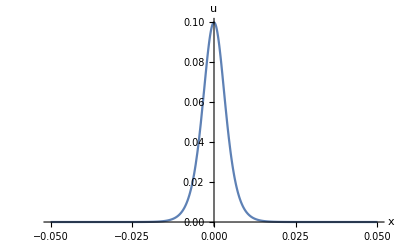

```mathematica
A=-0.1;
R=5*10^-3;
c=Sqrt[Ε/ρ];
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
d=β/(2ρ);
a=-((ν+1)R^2)/4;
b=(ν^2+ν+1)R^2/2;
u[x_,t_]=A Sech[(√(3/2) √(A d)c)/(√(b (9 c^4+6 A c^2 d)+2 a (9 c^4+6 A c^2 d+2 A^2 d^2)))(x-Sqrt[c^2+2/3 A d] t)]^2;
(*u0[x_,l_,m_,n_]=A Sech[Sqrt[(A d)/(6(a c^2+b+2/3 A d a))](x)]^2;*)
Plot[-u[x,0],{x,-0.05,0.05},PlotRange->All,AxesLabel->{x,u}]
```

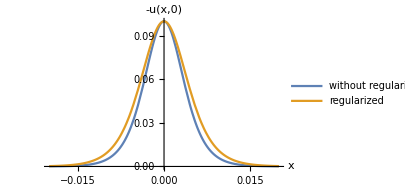

```mathematica
b=ν^2 R^2/2;
uReg[x_,t_]=A Sech[Sqrt[(A d)/(2b (3 c^2+2 A d))](x-Sqrt[c^2+2/3 A d] t)]^2;
fig=Plot[{-u[x,0],-uReg[x,0]},{x,-0.02,0.02},PlotRange->All,PlotLegends->Placed[{"without regularization", "regularized"},Bottom],PlotRange->All,AxesLabel->{x,"-u(x,0)"},ImageSize->300]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["reg_nonreg_compar.eps",fig];
```

### Dispersive relation [needs correction]

```mathematica
ClearAll[u,eq]
```

```mathematica
eq=D[u[x,t], t,t]-D[u[x,t], x,x]-1/2 δ^2(ν^2+ν+1)D[u[x,t], x,x,t,t]+1/4(1+ν)δ^2(D[u[x,t], t,t,t,t]+D[u[x,t], x,x,x,x]);
```

```mathematica
eq=D[u[x,t], t,t]-c^2 D[u[x,t], x,x]+R^2(b D[u[x,t], x,x,t,t]+a/c^2 D[u[x,t], t,t,t,t]+d c^2 D[u[x,t], x,x,x,x]);
```

```mathematica
u[x_,t_]=Exp[I(k/R x - ω c/R t)];
disp=eq/Exp[I(k/R x - ω c/R t)]//Simplify
```

(c^2 (k^2+d k^4-ω^2+b k^2 ω^2+a ω^4))/R^2

```mathematica
Solve[disp==0,ω]//Simplify
```

{{ω→-(√(-(-1+b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→(√(-(-1+b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→-(√((1-b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→(√((1-b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)}}

```mathematica
Series[(2+δ^2 (1+ν+ν^2) ω^2-√(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4))/(δ^2 (1+ν)),{δ,0,2}]
```

ω^2-1/2 (ν^2 ω^4) δ^2+O[δ]^3

```mathematica
(2+δ^2 (1+ν+ν^2) ω^2)^2-(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4)//Simplify
```

δ^2 (1+ν) ω^2 (4+δ^2 (1+ν) ω^2)

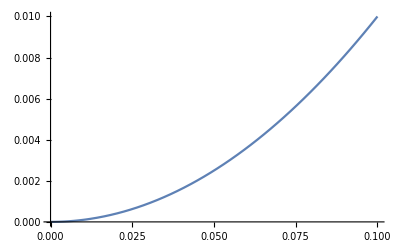

```mathematica
k2=(2+δ^2 (1+ν+ν^2) ω^2-√(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4))/(δ^2 (1+ν))/.{δ->0.5,ν->1/3};
Plot[k2,{ω,0,0.1}]
```

```mathematica
eqreg=D[u[x,t], t,t]-D[u[x,t], x,x]-1/2 δ^2 ν^2 D[u[x,t], x,x,t,t];
dispreg=eqreg/ⅇ^(k x-t ω)//Simplify
Solve[dispreg==0,k]//Simplify
```

ω^2-1/2 k^2 (2+δ^2 ν^2 ω^2)

{{k→-ω/(√(1+1/2 δ^2 ν^2 ω^2))},{k→ω/(√(1+1/2 δ^2 ν^2 ω^2))}}

### Plasticity

```mathematica
ndPred={
{ndPxxRed,ndPxrRed,0},
{ndPxrRed,ndPrrRed,0},
{0,0,0}
};
```

```mathematica
For[i=1,i<3,i++,
For[j=1,j<3,j++,
cl=CoefficientList[ndPred⟦i,j⟧,{ε,δ},{2,4}];
ndPred⟦i,j⟧=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
];
];
Clear[i,j];
```

```mathematica
InvScales={Derivative[i_,k_][U0][x_,t_]->(Derivative[i,k][U0][x,t])/(ε L)L^(i+k) s^-k,
U0[x,t]->U0[x,t]/(ε L),δ->R/L,γ->γ/ε};
```

```mathematica
ClearAll[U0,ν,l,m,n,Ε,ρ,R,A]
```

```mathematica
(* Compute only once *)
ndPred⟦1,2⟧=δ ndPred⟦1,2⟧;
ndPred⟦2,1⟧=δ ndPred⟦2,1⟧;
ndPred=ε ndPred;
```

```mathematica
Pred=ndPred/.InvScales//Simplify;
```

```mathematica
VonMises[x_,r_,t_]=-3Inv2[Pred-IdentityMatrix[3]*Tr[Pred]/3]//Simplify;
```

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));μ=Ε/(2(1+ν));
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
```

```mathematica
s=Sqrt[(Ε+γ β)/ρ];
B[a_,b_,d_]=Sqrt[(3A β s^2 ρ)/(-4 R^2 (a (A β+3 s^2 ρ)^2+3 s^2 ρ (A b β+3 s^2 (b+d) ρ)))];
v=Sqrt[s^2+(A β)/(3ρ)];
```

```mathematica
u0[x_,t_]=(A-3γ) (Cosh [B[(1+ν)/4,(-1-ν-ν^2)/2,(1+ν)/4](x-v t)])^-2;
```

```mathematica
U0[x_,t_]=Integrate[u0[x,t],x];
```

```mathematica
R=0.01;
```

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
(* PMMA *)
ρ=1180; Ε=4.9*10^9; ν=0.34;
l =-10.93*10^9; m= -7.73*10^9; n=-1.41*10^9;
```

```mathematica
VonMisesA[A_,γ_,x_,r_,t_]=VonMises[x,r,t];
```

```mathematica
Manipulate[{Sqrt[VonMisesA[A,γ,0,0,0]],A-3γ},{A,-0.1,0.3},{γ,-0.1,0.1}]
```

```mathematica
xarr=Array[#&,11,{-.2,.2}];
vmarr=Array[VonMises[xarr,#,0]&,5,{0,R}];
Max[vmarr]
```

2.51452×10^17

Soliton of extension is not elastic in PS rod.
PS yield stress: 86 MPa (extension),  114 MPa (compression).

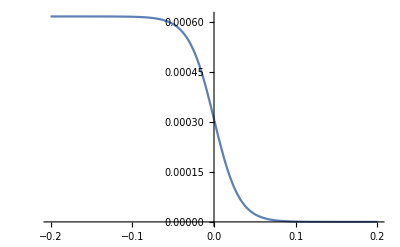

```mathematica
Plot[U0[x,0,0],{x,-.2,.2}]
```

```mathematica
(* Linear stress tensor *)
Displace0={U0[x,r,t],V01[x,r,t],0};
Deform0=RotateRight[Grad[RotateLeft[Displace0,1],{r,ϕ,x},"Cylindrical"],{1,1}];
SGr0=(Transpose[Deform0]+Deform0)/2;
P0=λ Inv1[SGr0]IdentityMatrix[3]+2μ SGr0//Simplify;
```

```mathematica
P0
```

{{-(3.7×10^7)/(1. Cosh[61425.3 t] Cosh[32.4757 x]-1. Sinh[61425.3 t] Sinh[32.4757 x])^2,-3.04883×10^8 r Sech[32.4757 (-1891.43 t+x)]^2 Tanh[32.4757 (-1891.43 t+x)],0.},{-3.04883×10^8 r Sech[32.4757 (-1891.43 t+x)]^2 Tanh[32.4757 (-1891.43 t+x)],0.,0.},{0.,0.,0.}}

```mathematica
(* Von Mises stress *)
VonMises[x_,r_,t_]=-3Inv2[P0-IdentityMatrix[3]*Tr[P0]/3]//Simplify
```

-(1.369×10^15)/(1. Cosh[61425.3 t] Cosh[32.4757 x]-1. Sinh[61425.3 t] Sinh[32.4757 x])^4-2.78862×10^17 r^2 Sech[32.4757 (-1891.43 t+x)]^4 Tanh[32.4757 (-1891.43 t+x)]^2

```mathematica
xarr=Array[#&,101,{-.2,.2}];
vmarr=Array[VonMises[xarr,#,0]&,11,{0,R}];
Max[vmarr]
```

### Test

```mathematica
Displace={U[x,r,ϕ],V[x,r,ϕ],W[x,r,ϕ]};
Deform=RotateRight[Grad[RotateLeft[Displace,1],{r,ϕ,x},"Cylindrical"],{1,1}];
Deform//MatrixForm
```

(U^(1,0,0)[x,r,ϕ] | U^(0,1,0)[x,r,ϕ] | (U^(0,0,1)[x,r,ϕ])/r
V^(1,0,0)[x,r,ϕ] | V^(0,1,0)[x,r,ϕ] | (-W[x,r,ϕ]+V^(0,0,1)[x,r,ϕ])/r
W^(1,0,0)[x,r,ϕ] | W^(0,1,0)[x,r,ϕ] | (V[x,r,ϕ]+W^(0,0,1)[x,r,ϕ])/r)

```mathematica
SGrD=DiagonalMatrix[{l1, l2, l3}];
I1 = Inv1[SGrD];
I2 = Inv2[SGrD];
I3 = Inv3[SGrD];
Pot[l1_,l2_,l3_]=(λ+2 μ)/2 I1^2-2 μ I2+(l+2 m)/3 I1^3-2 m I1 I2+n I3
```

-(l1+l2+l3) (-l1^2-l2^2-l3^2+(l1+l2+l3)^2) m+1/3 (l1+l2+l3)^3 (l+2 m)+l1 l2 l3 n-(-l1^2-l2^2-l3^2+(l1+l2+l3)^2) μ+1/2 (l1+l2+l3)^2 (λ+2 μ)

```mathematica
Pot[ε,γ,ε]//Simplify
```

n γ ε^2+2/3 m (γ-ε)^2 (γ+2 ε)+1/3 l (γ+2 ε)^3+(γ^2 λ)/2+2 γ ε λ+2 ε^2 λ+γ^2 μ+2 ε^2 μ

```mathematica
(1-(D[Pot[ε,γ,ε], γ,ε])^2/(D[Pot[ε,γ,ε], γ,γ]D[Pot[ε,γ,ε], ε,ε]))D[Pot[ε,γ,ε], γ,γ]/.{ε->-λ/(2(λ+μ)) γ(*,γ->0*)}//FullSimplify
```

(γ λ^2 (-(-6 m+n)^2 γ+6 n λ)+4 λ ((3 l n+4 m (-3 m+n)) γ^2+3 (m+n) γ λ+3 λ^2) μ+2 (4 m (-2 m+n) γ^2+5 (2 m+n) γ λ+16 λ^2+2 l γ (6 m γ+n γ+6 λ)) μ^2+4 ((6 l+2 m+n) γ+7 λ) μ^3+8 μ^4)/(2 (λ+μ) (4 l γ μ+n γ (λ+μ)+2 (λ+μ)^2-2 m γ (2 λ+μ)))

```mathematica
γ/(γ^2-ε^2) D[Pot[ε,γ,ε], γ]/.{ε->-λ/(2(λ+μ)) γ(*,γ->0*)}//Simplify
```

(n γ λ^2+4 μ (3 λ^2+l γ μ+5 λ μ+2 μ^2)+2 m γ (3 λ^2+8 λ μ+4 μ^2))/(3 λ^2+8 λ μ+4 μ^2)